## Studies

### Interpolation

#### Test run after changing ϵ and temperature in mantle

```mathematica
test10TeVinterpolationFe1=Table[InterpolatevχandωσdEReξ["mpD"/.mpDPointshigher[[1]],FeTotalparams[[i]],10,60,10^-6,4,True,True,2,ToString[StringForm["Fe ``",i]],True],{i,1}];
```

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

### Plot total energy loss for various masses

#### Combined Plots for Core

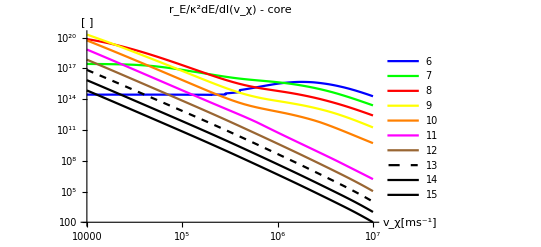

```mathematica
(*Legended@Show@*)
plotstyle= {Blue,Green,Red,Yellow,Orange,Magenta,Brown, Directive[Black, Dashed],Directive[Black, Thick],Directive[Black, Thin]};
Quiet@LogLogPlot[Evaluate@Table[eind = FirstPosition["mχ"/.ElectronicσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
Nucind = FirstPosition["mχ"/.NuclearσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
("rE"/.Constants`EarthRepl)("dEdlofr"/.GetTotalELFunction[ElectronicσDicts[[eind]],NuclearσDicts[[Nucind]]])[10^6,vχ]/((10^m ("JpereV")/("c")^2/.Constants`SIConstRepl)vχ^2/2)
,{m,6,15}],{vχ,10^4,10^7},AxesLabel->{"v_χ[ms^-1]","[ ]"},PlotLabel->"r_E/κ^2dE/dl(v_χ) - core",PlotStyle->plotstyle,PlotLegends->LineLegend[plotstyle,Table[ToString[m],{m,6,15}]]]
```

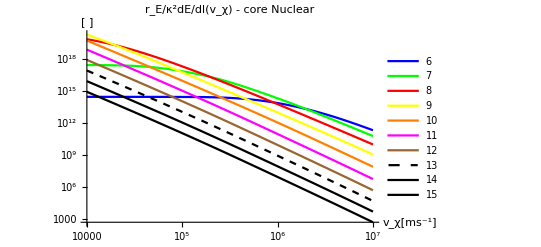

```mathematica
plotstyle= {Blue,Green,Red,Yellow,Orange,Magenta, Brown,Directive[Black, Dashed],Directive[Black, Thick],Directive[Black, Thin]};

Quiet@LogLogPlot[Evaluate[Table[Nucind = FirstPosition["mχ"/.NuclearσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
("rE"/.Constants`EarthRepl)("dEdlofr"/.GetNucELFunction[NuclearσDicts[[Nucind]]])[10^6,vχ]/((10^m ("JpereV")/("c")^2/.Constants`SIConstRepl)vχ^2/2)
,{m,6,15}]],{vχ,10^4,10^7},AxesLabel->{"v_χ[ms^-1]","[ ]"},PlotLabel->"r_E/κ^2dE/dl(v_χ) - core Nuclear",PlotStyle->plotstyle,  PlotLegends->LineLegend[plotstyle,Evaluate[Table[ToString[m],{m,6,15}]]]]
```

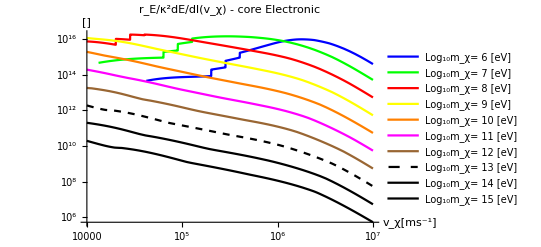

```mathematica
plotstyle= {Blue,Green,Red,Yellow,Orange,Magenta, Brown,Directive[Black, Dashed],Directive[Black, Thick],Directive[Black, Thin]};
Quiet@LogLogPlot[Evaluate[Table[eind = FirstPosition["mχ"/.ElectronicσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
("rE"/.Constants`EarthRepl)(("dEdlofr"/.GeteELFunction[ElectronicσDicts[[eind]]])[10^6,vχ]/((10^m ("JpereV")/("c")^2/.Constants`SIConstRepl)vχ^2/2))
,{m,6,15}]],{vχ,10^4,10^7},AxesLabel->{"v_χ[ms^-1]","[]"},PlotLabel->"r_E/κ^2dE/dl(v_χ) - core Electronic",PlotStyle->plotstyle,PlotLegends->LineLegend[plotstyle,Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,15}]]]
```

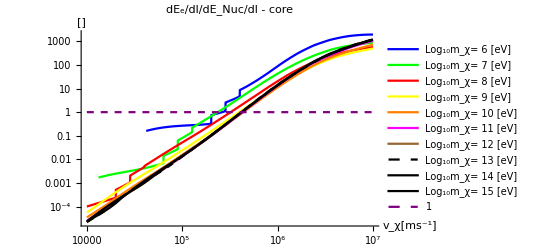

```mathematica
plotstyle= {Blue,Green,Red,Yellow,Orange,Magenta, Brown,Directive[Black, Dashed],Directive[Black, Thick],Directive[Black, Thin],Directive[Purple,Dashed]};
Quiet@LogLogPlot[Evaluate[Append[Table[eind = FirstPosition["mχ"/.ElectronicσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
Nucind = FirstPosition["mχ"/.NuclearσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
(("dEdlofr"/.GeteELFunction[ElectronicσDicts[[eind]]])[10^6,vχ])/(("dEdlofr"/.GetNucELFunction[NuclearσDicts[[Nucind]]])[10^6,vχ])
,{m,6,15}],1]],{vχ,10^4,10^7},AxesLabel->{"v_χ[ms^-1]","[]"},PlotLabel->"dE_e/dl/dE_Nuc/dl - core",PlotStyle->plotstyle,PlotLegends->LineLegend[plotstyle,Append[Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,15}],1]]]
```

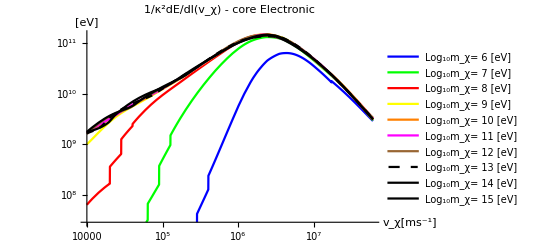

```mathematica
plotstyle= {Blue,Green,Red,Yellow,Orange,Magenta, Brown,Directive[Black, Dashed],Directive[Black, Thick],Directive[Black, Thin]};
Quiet@LogLogPlot[Evaluate[Table[eind = FirstPosition["mχ"/.ElectronicσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
((("JpereV")^-1/.SIConstRepl)("dEdlofr"/.GeteELFunction[ElectronicσDicts[[eind]]])[10^6,vχ])
,{m,6,15}]],{vχ,10^4,0.2 "c"/.SIConstRepl},AxesLabel->{"v_χ[ms^-1]","[eV]"},PlotLabel->"1/κ^2dE/dl(v_χ) - core Electronic",PlotStyle->plotstyle,PlotLegends->LineLegend[plotstyle,Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,15}]]]
```

#### Combined Plots for Mantle

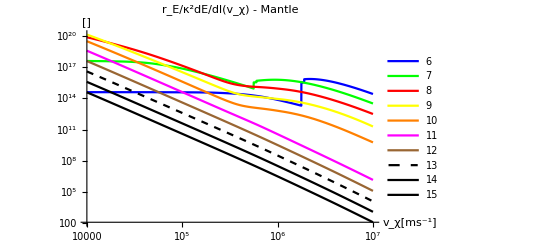

```mathematica
(*Legended@Show@*)
plotstyle= {Blue,Green,Red,Yellow,Orange,Magenta,Brown, Directive[Black, Dashed],Directive[Black, Thick],Directive[Black, Thin]};
Quiet@LogLogPlot[Evaluate@Table[eind = FirstPosition["mχ"/.ElectronicσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
Nucind = FirstPosition["mχ"/.NuclearσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
("rE"/.Constants`EarthRepl)("dEdlofr"/.GetTotalELFunction[ElectronicσDicts[[eind]],NuclearσDicts[[Nucind]]])[5 10^6,vχ]/((10^m ("JpereV")/("c")^2/.Constants`SIConstRepl)vχ^2/2)
,{m,6,15}],{vχ,10^4,10^7},AxesLabel->{"v_χ[ms^-1]","[]"},PlotLabel->"r_E/κ^2dE/dl(v_χ) - Mantle",PlotStyle->plotstyle,PlotLegends->LineLegend[plotstyle,Table[ToString[m],{m,6,15}]]]
```

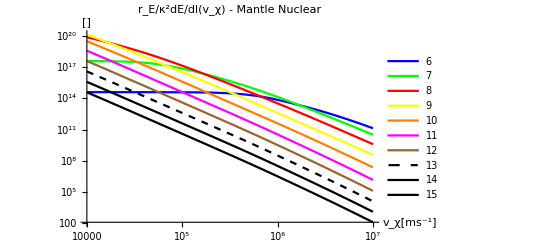

```mathematica
plotstyle= {Blue,Green,Red,Yellow,Orange,Magenta,Brown, Directive[Black, Dashed],Directive[Black, Thick],Directive[Black, Thin]};

LogLogPlot[Evaluate[Table[Nucind = FirstPosition["mχ"/.NuclearσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
("rE"/.Constants`EarthRepl)("dEdlofr"/.GetNucELFunction[NuclearσDicts[[Nucind]]])[5 10^6,vχ]/((10^m ("JpereV")/("c")^2/.Constants`SIConstRepl)vχ^2/2)
,{m,6,15}]],{vχ,10^4,10^7},AxesLabel->{"v_χ[ms^-1]","[]"},PlotLabel->"r_E/κ^2dE/dl(v_χ) - Mantle Nuclear",PlotStyle->plotstyle,  PlotLegends->LineLegend[plotstyle,Evaluate[Table[ToString[m],{m,6,15}]]]]
```

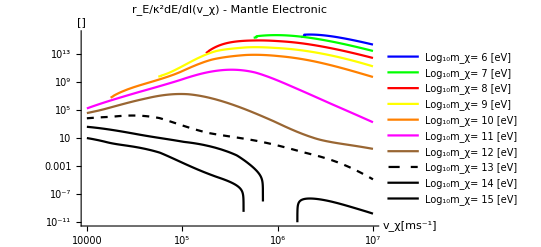

```mathematica
plotstyle= {Blue,Green,Red,Yellow,Orange,Magenta,Brown, Directive[Black, Dashed],Directive[Black, Thick],Directive[Black, Thin]};
Quiet@LogLogPlot[Evaluate[Table[eind = FirstPosition["mχ"/.ElectronicσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
("rE"/.Constants`EarthRepl)(("dEdlofr"/.GeteELFunction[ElectronicσDicts[[eind]]])[5 10^6,vχ]/((10^m ("JpereV")/("c")^2/.Constants`SIConstRepl)vχ^2/2))
,{m,6,15}]],{vχ,10^4,10^7},AxesLabel->{"v_χ[ms^-1]","[]"},PlotLabel->"r_E/κ^2dE/dl(v_χ) - Mantle Electronic",PlotStyle->plotstyle,PlotLegends->LineLegend[plotstyle,Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,15}]]]
```

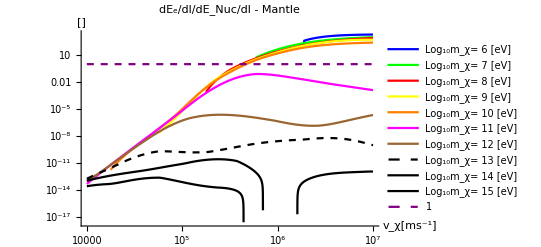

```mathematica
plotstyle= {Blue,Green,Red,Yellow,Orange,Magenta,Brown, Directive[Black, Dashed],Directive[Black, Thick],Directive[Black, Thin],Directive[Purple,Dashed]};
Quiet@LogLogPlot[Evaluate[Append[Table[eind = FirstPosition["mχ"/.ElectronicσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
Nucind = FirstPosition["mχ"/.NuclearσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
(("dEdlofr"/.GeteELFunction[ElectronicσDicts[[eind]]])[5 10^6,vχ])/(("dEdlofr"/.GetNucELFunction[NuclearσDicts[[Nucind]]])[5 10^6,vχ])
,{m,6,15}],1]],{vχ,10^4,10^7},AxesLabel->{"v_χ[ms^-1]","[]"},PlotLabel->"dE_e/dl/dE_Nuc/dl - Mantle",PlotStyle->plotstyle,PlotLegends->LineLegend[plotstyle,Append[Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,15}],1]]]
```

#### Speed of incoming DPs

```mathematica
"The mean velocity is approximately constant throughout the mass range for constant v0"
```

The mean velocity is approximately constant throughout the mass range for constant v0

```mathematica
"vpDmean"/.v0toβD[20 10^3,# 10^-4,#]&;
%[10^7 ("JpereV")/("c")^2/.Constants`SIConstRepl]
```

14142.8

```mathematica
10^6 ("JpereV")/("c")^2/.Constants`SIConstRepl
Subscript[v̄, Subscript[p, D],Disk]==(Round@(("vpDmean")/10^3)/.v0toβD[20 10^3,% 10^-4,%])"km s^-1"
Subscript[v̄, Subscript[p, D],Halo]==(Round@(("vpDmean")/10^3)/.v0toβD[220 10^3,%% 10^-4,%%])"km s^-1"
```

1.78×10^-30

(v̄)_(p_D,Disk)==14 km s^-1

(v̄)_(p_D,Halo)==156 km s^-1

### Capture Rate and interaction length

Conclusion: no visible change

#### Combined Plots for Mantle - post velocity range fix

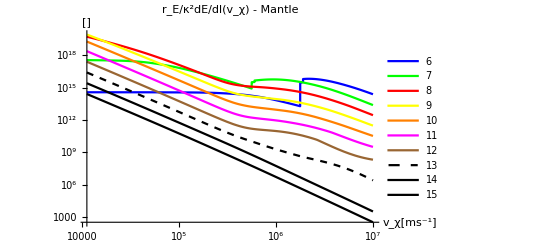

```mathematica
(*Legended@Show@*)
plotstyle= {Blue,Green,Red,Yellow,Orange,Magenta,Brown, Directive[Black, Dashed],Directive[Black, Thick],Directive[Black, Thin]};
Quiet@LogLogPlot[Evaluate@Table[eind = FirstPosition["mχ"/.ElectronicσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
Nucind = FirstPosition["mχ"/.NuclearσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
("rE"/.Constants`EarthRepl)("dEdlofr"/.GetTotalELFunction[ElectronicσDicts[[eind]],NuclearσDicts[[Nucind]]])[5 10^6,vχ]/((10^m ("JpereV")/("c")^2/.Constants`SIConstRepl)vχ^2/2)
,{m,6,15}],{vχ,"vesc"/.EarthRepl,10^7},AxesLabel->{"v_χ[ms^-1]","[]"},PlotLabel->"r_E/κ^2dE/dl(v_χ) - Mantle",PlotStyle->plotstyle,PlotLegends->LineLegend[plotstyle,Table[ToString[m],{m,6,15}]]]
```

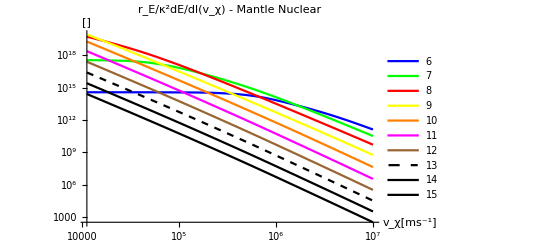

```mathematica
plotstyle= {Blue,Green,Red,Yellow,Orange,Magenta,Brown, Directive[Black, Dashed],Directive[Black, Thick],Directive[Black, Thin]};

Quiet@LogLogPlot[Evaluate[Table[Nucind = FirstPosition["mχ"/.NuclearσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
("rE"/.Constants`EarthRepl)("dEdlofr"/.GetNucELFunction[NuclearσDicts[[Nucind]]])[5 10^6,vχ]/((10^m ("JpereV")/("c")^2/.Constants`SIConstRepl)vχ^2/2)
,{m,6,15}]],{vχ,"vesc"/.EarthRepl,10^7},AxesLabel->{"v_χ[ms^-1]","[]"},PlotLabel->"r_E/κ^2dE/dl(v_χ) - Mantle Nuclear",PlotStyle->plotstyle,  PlotLegends->LineLegend[plotstyle,Evaluate[Table[ToString[m],{m,6,15}]]]]
```

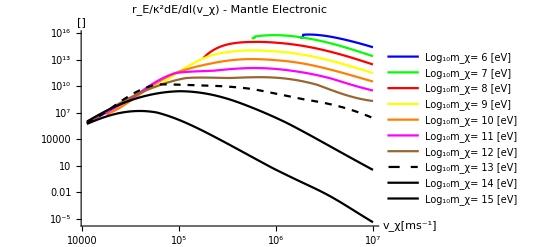

```mathematica
plotstyle= {Blue,Green,Red,Yellow,Orange,Magenta,Brown, Directive[Black, Dashed],Directive[Black, Thick],Directive[Black, Thin]};
Quiet@LogLogPlot[Evaluate[Table[eind = FirstPosition["mχ"/.ElectronicσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
("rE"/.Constants`EarthRepl)(("dEdlofr"/.GeteELFunction[ElectronicσDicts[[eind]]])[5 10^6,vχ]/((10^m ("JpereV")/("c")^2/.Constants`SIConstRepl)vχ^2/2))
,{m,6,15}]],{vχ,"vesc"/.EarthRepl,10^7},AxesLabel->{"v_χ[ms^-1]","[]"},PlotLabel->"r_E/κ^2dE/dl(v_χ) - Mantle Electronic",PlotStyle->plotstyle,PlotLegends->LineLegend[plotstyle,Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,15}]]]
```

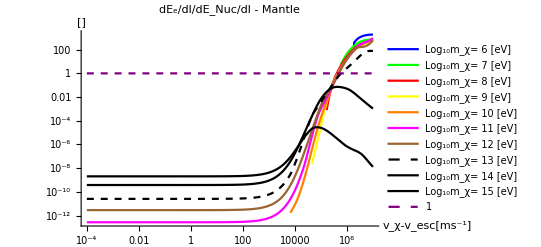

```mathematica
plotstyle= {Blue,Green,Red,Yellow,Orange,Magenta,Brown, Directive[Black, Dashed],Directive[Black, Thick],Directive[Black, Thin],Directive[Purple,Dashed]};
Quiet@LogLogPlot[Evaluate[Append[Table[eind = FirstPosition["mχ"/.ElectronicσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
Nucind = FirstPosition["mχ"/.NuclearσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
(("dEdlofr"/.GeteELFunction[ElectronicσDicts[[eind]]])[5 10^6,vχ+"vesc"/.EarthRepl])/(("dEdlofr"/.GetNucELFunction[NuclearσDicts[[Nucind]]])[5 10^6,vχ+"vesc"/.EarthRepl])
,{m,6,15}],1]],{vχ,10^-4,10^7-"vesc"/.EarthRepl},AxesLabel->{"v_χ-v_esc[ms^-1]","[]"},PlotLabel->"dE_e/dl/dE_Nuc/dl - Mantle",PlotStyle->plotstyle,PlotLegends->LineLegend[plotstyle,Append[Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,15}],1]]]
```

#### Combined Plots for Core - post velocity range fix

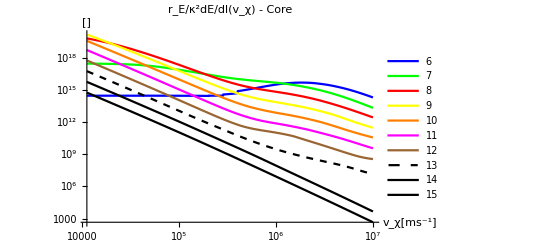

```mathematica
(*Legended@Show@*)
plotstyle= {Blue,Green,Red,Yellow,Orange,Magenta,Brown, Directive[Black, Dashed],Directive[Black, Thick],Directive[Black, Thin]};
Quiet@LogLogPlot[Evaluate@Table[eind = FirstPosition["mχ"/.ElectronicσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
Nucind = FirstPosition["mχ"/.NuclearσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
("rE"/.Constants`EarthRepl)("dEdlofr"/.GetTotalELFunction[ElectronicσDicts[[eind]],NuclearσDicts[[Nucind]]])[1 10^6,vχ]/((10^m ("JpereV")/("c")^2/.Constants`SIConstRepl)vχ^2/2)
,{m,6,15}],{vχ,"vesc"/.EarthRepl,10^7},AxesLabel->{"v_χ[ms^-1]","[]"},PlotLabel->"r_E/κ^2dE/dl(v_χ) - Core",PlotStyle->plotstyle,PlotLegends->LineLegend[plotstyle,Table[ToString[m],{m,6,15}]]]
```

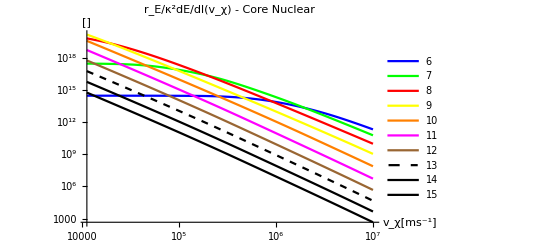

```mathematica
plotstyle= {Blue,Green,Red,Yellow,Orange,Magenta,Brown, Directive[Black, Dashed],Directive[Black, Thick],Directive[Black, Thin]};

Quiet@LogLogPlot[Evaluate[Table[Nucind = FirstPosition["mχ"/.NuclearσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
("rE"/.Constants`EarthRepl)("dEdlofr"/.GetNucELFunction[NuclearσDicts[[Nucind]]])[1 10^6,vχ]/((10^m ("JpereV")/("c")^2/.Constants`SIConstRepl)vχ^2/2)
,{m,6,15}]],{vχ,"vesc"/.EarthRepl,10^7},AxesLabel->{"v_χ[ms^-1]","[]"},PlotLabel->"r_E/κ^2dE/dl(v_χ) - Core Nuclear",PlotStyle->plotstyle,  PlotLegends->LineLegend[plotstyle,Evaluate[Table[ToString[m],{m,6,15}]]]]
```

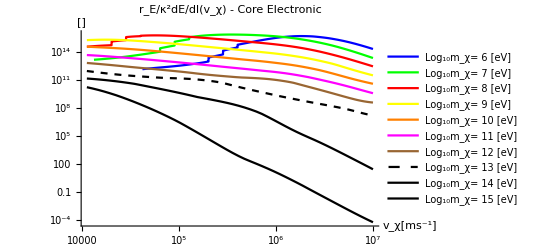

```mathematica
plotstyle= {Blue,Green,Red,Yellow,Orange,Magenta,Brown, Directive[Black, Dashed],Directive[Black, Thick],Directive[Black, Thin]};
Quiet@LogLogPlot[Evaluate[Table[eind = FirstPosition["mχ"/.ElectronicσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
("rE"/.Constants`EarthRepl)(("dEdlofr"/.GeteELFunction[ElectronicσDicts[[eind]]])[1 10^6,vχ]/((10^m ("JpereV")/("c")^2/.Constants`SIConstRepl)vχ^2/2))
,{m,6,15}]],{vχ,"vesc"/.EarthRepl,10^7},AxesLabel->{"v_χ[ms^-1]","[]"},PlotLabel->"r_E/κ^2dE/dl(v_χ) - Core Electronic",PlotStyle->plotstyle,PlotLegends->LineLegend[plotstyle,Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,15}]]]
```

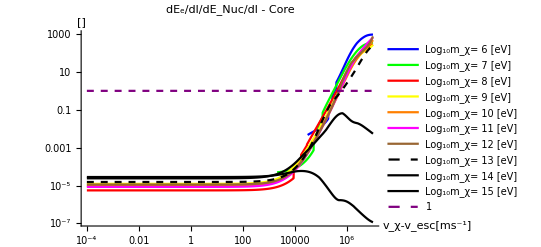

```mathematica
plotstyle= {Blue,Green,Red,Yellow,Orange,Magenta,Brown, Directive[Black, Dashed],Directive[Black, Thick],Directive[Black, Thin],Directive[Purple,Dashed]};
Quiet@LogLogPlot[Evaluate[Append[Table[eind = FirstPosition["mχ"/.ElectronicσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
Nucind = FirstPosition["mχ"/.NuclearσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
(("dEdlofr"/.GeteELFunction[ElectronicσDicts[[eind]]])[1 10^6,vχ+"vesc"/.Constants`EarthRepl])/(("dEdlofr"/.GetNucELFunction[NuclearσDicts[[Nucind]]])[1 10^6,vχ+"vesc"/.Constants`EarthRepl])
,{m,6,15}],1]],{vχ,10^-4,10^7-"vesc"/.Constants`EarthRepl},AxesLabel->{"v_χ-v_esc[ms^-1]","[]"},PlotLabel->"dE_e/dl/dE_Nuc/dl - Core",PlotStyle->plotstyle,PlotLegends->LineLegend[plotstyle,Append[Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,15}],1]],PlotRange->All]
```

#### Plot Capture Interaction Length Nuclear - post velocity range fix

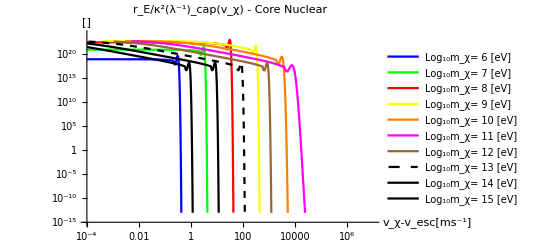

```mathematica
plotstyle= {Blue,Green,Red,Yellow,Orange,Magenta, Brown,Directive[Black, Dashed],Directive[Black, Thick],Directive[Black, Thin]};
LogLogPlot[Evaluate[Table[Nucind = FirstPosition["mχ"/.NuclearσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
("rE"/.Constants`EarthRepl)GetTotalNucWeakCaptureInteractionLength[Gather[NuclearσDicts[[Nucind]],#1["regionindex"]==#2["regionindex"]&][[1]]][vχ+"vesc"/.Constants`EarthRepl]
,{m,6,15}]],{vχ,10^-4,10^5-"vesc"/.Constants`EarthRepl},AxesLabel->{"v_χ-v_esc[ms^-1]","[]"},PlotLabel->"r_E/κ^2(λ^-1)_cap(v_χ) - Core Nuclear",PlotStyle->plotstyle,PlotLegends->LineLegend[plotstyle,Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,15}]],PlotRange->{{10^-4,10^7-"vesc"/.Constants`EarthRepl},{10^-15,10^24}}]
```

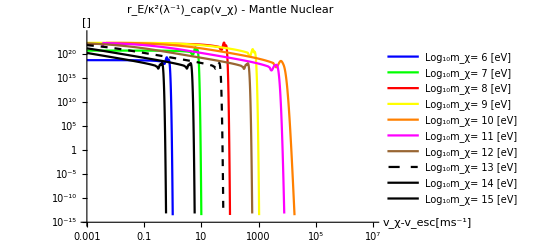

```mathematica
plotstyle= {Blue,Green,Red,Yellow,Orange,Magenta, Brown,Directive[Black, Dashed],Directive[Black, Thick],Directive[Black, Thin]};
LogLogPlot[Evaluate[Table[Nucind = FirstPosition["mχ"/.NuclearσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
("rE"/.Constants`EarthRepl)GetTotalNucWeakCaptureInteractionLength[Gather[NuclearσDicts[[Nucind]],#1["regionindex"]==#2["regionindex"]&][[2]]][vχ+"vesc"/.Constants`EarthRepl]
,{m,6,15}]],{vχ,10^-3,10^7-"vesc"/.Constants`EarthRepl},AxesLabel->{"v_χ-v_esc[ms^-1]","[]"},PlotLabel->"r_E/κ^2(λ^-1)_cap(v_χ) - Mantle Nuclear",PlotStyle->plotstyle,PlotLegends->LineLegend[plotstyle,Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,15}]],PlotRange->{{10^-3,10^7-"vesc"/.Constants`EarthRepl},{10^-15,10^24}}]
```

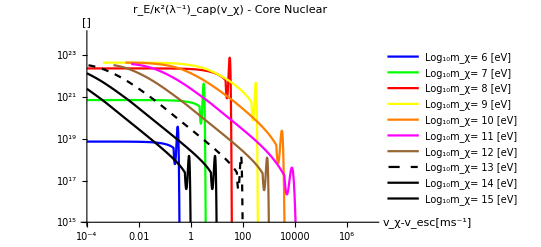

```mathematica
plotstyle= {Blue,Green,Red,Yellow,Orange,Magenta, Brown,Directive[Black, Dashed],Directive[Black, Thick],Directive[Black, Thin]};
LogLogPlot[Evaluate[Table[Nucind = FirstPosition["mχ"/.NuclearσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
("rE"/.Constants`EarthRepl)GetTotalNucWeakCaptureInteractionLength[Gather[NuclearσDicts[[Nucind]],#1["regionindex"]==#2["regionindex"]&][[1]]][vχ+"vesc"/.Constants`EarthRepl]
,{m,6,15}]],{vχ,10^-4,10^5-"vesc"/.Constants`EarthRepl},AxesLabel->{"v_χ-v_esc[ms^-1]","[]"},PlotLabel->"r_E/κ^2(λ^-1)_cap(v_χ) - Core Nuclear",PlotStyle->plotstyle,PlotLegends->LineLegend[plotstyle,Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,15}]],PlotRange->{{10^-4,10^7-"vesc"/.Constants`EarthRepl},{10^15,10^24}}]
```

#### Plot Capture Interaction Length Nuclear - post velocity range fix

```mathematica
plotstyle= {Blue,Green,Red,Yellow,Orange,Magenta, Brown,Directive[Black, Dashed],Directive[Black, Thick],Directive[Black, Thin]};
LogLogPlot[Evaluate[Table[Nucind = FirstPosition["mχ"/.NuclearσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
("rE"/.Constants`EarthRepl)GetTotalNucWeakCaptureInteractionLength[Gather[NuclearσDicts[[Nucind]],#1["regionindex"]==#2["regionindex"]&][[1]]][vχ+"vesc"/.Constants`EarthRepl]
,{m,6,15}]],{vχ,10^-4,10^5-"vesc"/.Constants`EarthRepl},AxesLabel->{"v_χ-v_esc[ms^-1]","[]"},PlotLabel->"r_E/κ^2(λ^-1)_cap(v_χ) - Core Nuclear",PlotStyle->plotstyle,PlotLegends->LineLegend[plotstyle,Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,15}]],PlotRange->{{10^-4,10^7-"vesc"/.Constants`EarthRepl},{10^-15,10^24}}]
```

-Graphics-

```mathematica
plotstyle= {Blue,Green,Red,Yellow,Orange,Magenta, Brown,Directive[Black, Dashed],Directive[Black, Thick],Directive[Black, Thin]};
LogLogPlot[Evaluate[Table[Nucind = FirstPosition["mχ"/.NuclearσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
("rE"/.Constants`EarthRepl)GetTotalNucWeakCaptureInteractionLength[Gather[NuclearσDicts[[Nucind]],#1["regionindex"]==#2["regionindex"]&][[2]]][vχ+"vesc"/.Constants`EarthRepl]
,{m,6,15}]],{vχ,10^-3,10^7-"vesc"/.Constants`EarthRepl},AxesLabel->{"v_χ-v_esc[ms^-1]","[]"},PlotLabel->"r_E/κ^2(λ^-1)_cap(v_χ) - Mantle Nuclear",PlotStyle->plotstyle,PlotLegends->LineLegend[plotstyle,Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,15}]],PlotRange->{{10^-3,10^7-"vesc"/.Constants`EarthRepl},{10^-15,10^24}}]
```

-Graphics-

```mathematica
plotstyle= {Blue,Green,Red,Yellow,Orange,Magenta, Brown,Directive[Black, Dashed],Directive[Black, Thick],Directive[Black, Thin]};
LogLogPlot[Evaluate[Table[Nucind = FirstPosition["mχ"/.NuclearσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
("rE"/.Constants`EarthRepl)GetTotalNucWeakCaptureInteractionLength[Gather[NuclearσDicts[[Nucind]],#1["regionindex"]==#2["regionindex"]&][[1]]][vχ+"vesc"/.Constants`EarthRepl]
,{m,6,15}]],{vχ,10^-4,10^5-"vesc"/.Constants`EarthRepl},AxesLabel->{"v_χ-v_esc[ms^-1]","[]"},PlotLabel->"r_E/κ^2(λ^-1)_cap(v_χ) - Core Nuclear",PlotStyle->plotstyle,PlotLegends->LineLegend[plotstyle,Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,15}]],PlotRange->{{10^-4,10^7-"vesc"/.Constants`EarthRepl},{10^15,10^24}}]
```

-Graphics-

#### Plot Capture Interaction Length Electronic - post velocity range fix

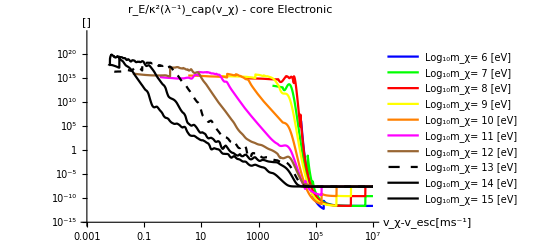

```mathematica
plotstyle= {Blue,Green,Red,Yellow,Orange,Magenta, Brown,Directive[Black, Dashed],Directive[Black, Thick],Directive[Black, Thin]};
LogLogPlot[Evaluate[Table[eind = FirstPosition["mχ"/.ElectronicσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
("rE"/.Constants`EarthRepl)GetTotaleWeakCaptureInteractionLength[Gather[ElectronicσDicts[[eind]],#1["regionindex"]==#2["regionindex"]&][[1]]][vχ+"vesc"/.Constants`EarthRepl]
,{m,6,15}]],{vχ,10^-4,(10^7)-"vesc"/.Constants`EarthRepl},AxesLabel->{"v_χ-v_esc[ms^-1]","[]"},PlotLabel->"r_E/κ^2(λ^-1)_cap(v_χ) - core Electronic",PlotStyle->plotstyle,PlotLegends->LineLegend[plotstyle,Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,15}]],PlotRange->{{10^-3,10^7-"vesc"/.Constants`EarthRepl},{10^-15,10^24}}]
```

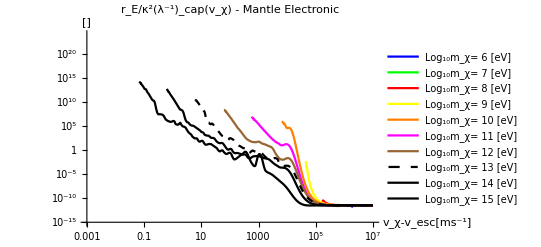

```mathematica
plotstyle= {Blue,Green,Red,Yellow,Orange,Magenta, Brown,Directive[Black, Dashed],Directive[Black, Thick],Directive[Black, Thin]};
LogLogPlot[Evaluate[Table[eind = FirstPosition["mχ"/.ElectronicσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
("rE"/.Constants`EarthRepl)GetTotaleWeakCaptureInteractionLength[Gather[ElectronicσDicts[[eind]],#1["regionindex"]==#2["regionindex"]&][[2]]][vχ+"vesc"/.Constants`EarthRepl]
,{m,6,15}]],{vχ,10^-4,(10^7)-"vesc"/.Constants`EarthRepl},AxesLabel->{"v_χ-v_esc[ms^-1]","[]"},PlotLabel->"r_E/κ^2(λ^-1)_cap(v_χ) - Mantle Electronic",PlotStyle->plotstyle,PlotLegends->LineLegend[plotstyle,Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,15}]],PlotRange->{{10^-3,10^7-"vesc"/.Constants`EarthRepl},{10^-15,10^24}}]
```

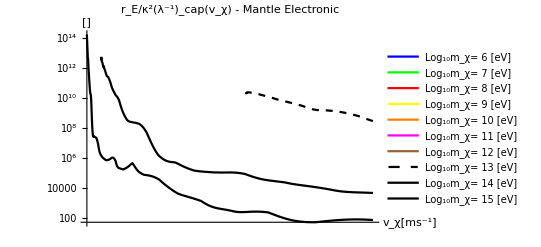

```mathematica
plotstyle= {Blue,Green,Red,Yellow,Orange,Magenta, Brown,Directive[Black, Dashed],Directive[Black, Thick],Directive[Black, Thin]};
LogLogPlot[Evaluate[Table[eind = FirstPosition["mχ"/.ElectronicσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
("rE"/.Constants`EarthRepl)GetTotaleWeakCaptureInteractionLength[Gather[ElectronicσDicts[[eind]],#1["regionindex"]==#2["regionindex"]&][[2]]][vχ]
,{m,6,15}]],{vχ,"vesc"/.Constants`EarthRepl,1.001 "vesc"/.Constants`EarthRepl},AxesLabel->{"v_χ[ms^-1]","[]"},PlotLabel->"r_E/κ^2(λ^-1)_cap(v_χ) - Mantle Electronic",PlotStyle->plotstyle,PlotLegends->LineLegend[plotstyle,Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,15}]],PlotRange->All]
```

#### Plot Capture Interaction Length Electronic - at 10^6 eV to explain drop off in capture rate

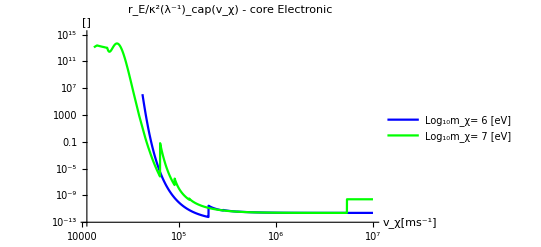

```mathematica
plotstyle= {Blue,Green,Red,Yellow,Orange,Magenta, Brown,Directive[Black, Dashed],Directive[Black, Thick],Directive[Black, Thin]};
LogLogPlot[Evaluate[Table[eind = FirstPosition["mχ"/.ElectronicσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
("rE"/.Constants`EarthRepl)GetTotaleWeakCaptureInteractionLength[Gather[ElectronicσDicts[[eind]],#1["regionindex"]==#2["regionindex"]&][[1]]][vχ]
,{m,6,7}]],{vχ,"vesc"/.Constants`EarthRepl,10^7},AxesLabel->{"v_χ[ms^-1]","[]"},PlotLabel->"r_E/κ^2(λ^-1)_cap(v_χ) - core Electronic",PlotStyle->plotstyle,PlotLegends->LineLegend[plotstyle,Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,7}]],PlotRange->{{"vesc"/.Constants`EarthRepl,10^7},{10^-13,10^15}}]
```

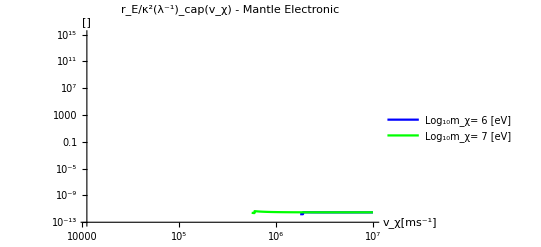

```mathematica
plotstyle= {Blue,Green,Red,Yellow,Orange,Magenta, Brown,Directive[Black, Dashed],Directive[Black, Thick],Directive[Black, Thin]};
LogLogPlot[Evaluate[Table[eind = FirstPosition["mχ"/.ElectronicσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
("rE"/.Constants`EarthRepl)GetTotaleWeakCaptureInteractionLength[Gather[ElectronicσDicts[[eind]],#1["regionindex"]==#2["regionindex"]&][[2]]][vχ]
,{m,6,7}]],{vχ,"vesc"/.Constants`EarthRepl,10^7},AxesLabel->{"v_χ[ms^-1]","[]"},PlotLabel->"r_E/κ^2(λ^-1)_cap(v_χ) - Mantle Electronic",PlotStyle->plotstyle,PlotLegends->LineLegend[plotstyle,Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,7}]],PlotRange->{{"vesc"/.Constants`EarthRepl,10^7},{10^-13,10^15}}]
```

### Capture and interaction length for dark electrons

#### Plot Capture Interaction Length Nuclear - post velocity range fix

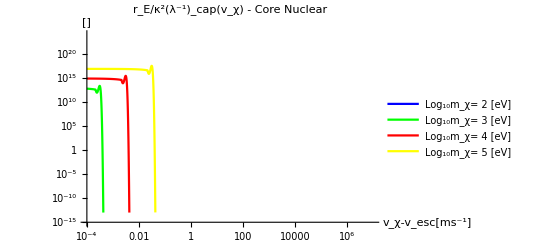

```mathematica
plotstyle= {Blue,Green,Red,Yellow,Orange,Magenta, Brown,Directive[Black, Dashed],Directive[Black, Thick],Directive[Black, Thin]};
LogLogPlot[Evaluate[Table[Nucind = FirstPosition["mχ"/.NuclearσDictseD,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
("rE"/.Constants`EarthRepl)GetTotalNucWeakCaptureInteractionLength[Gather[NuclearσDictseD[[Nucind]],#1["regionindex"]==#2["regionindex"]&][[1]]][vχ+"vesc"/.Constants`EarthRepl]
,{m,2,5}]],{vχ,10^-4,10^5-"vesc"/.Constants`EarthRepl},AxesLabel->{"v_χ-v_esc[ms^-1]","[]"},PlotLabel->"r_E/κ^2(λ^-1)_cap(v_χ) - Core Nuclear",PlotStyle->plotstyle,PlotLegends->LineLegend[plotstyle,Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,2,5}]],PlotRange->{{10^-4,10^7-"vesc"/.Constants`EarthRepl},{10^-15,10^24}}]
```

```mathematica
plotstyle= {Blue,Green,Red,Yellow,Orange,Magenta, Brown,Directive[Black, Dashed],Directive[Black, Thick],Directive[Black, Thin]};
LogLogPlot[Evaluate[Table[Nucind = FirstPosition["mχ"/.NuclearσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
("rE"/.Constants`EarthRepl)GetTotalNucWeakCaptureInteractionLength[Gather[NuclearσDicts[[Nucind]],#1["regionindex"]==#2["regionindex"]&][[2]]][vχ+"vesc"/.Constants`EarthRepl]
,{m,6,15}]],{vχ,10^-3,10^7-"vesc"/.Constants`EarthRepl},AxesLabel->{"v_χ-v_esc[ms^-1]","[]"},PlotLabel->"r_E/κ^2(λ^-1)_cap(v_χ) - Mantle Nuclear",PlotStyle->plotstyle,PlotLegends->LineLegend[plotstyle,Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,15}]],PlotRange->{{10^-3,10^7-"vesc"/.Constants`EarthRepl},{10^-15,10^24}}]
```

-Graphics-

```mathematica
plotstyle= {Blue,Green,Red,Yellow,Orange,Magenta, Brown,Directive[Black, Dashed],Directive[Black, Thick],Directive[Black, Thin]};
LogLogPlot[Evaluate[Table[Nucind = FirstPosition["mχ"/.NuclearσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
("rE"/.Constants`EarthRepl)GetTotalNucWeakCaptureInteractionLength[Gather[NuclearσDicts[[Nucind]],#1["regionindex"]==#2["regionindex"]&][[1]]][vχ+"vesc"/.Constants`EarthRepl]
,{m,6,15}]],{vχ,10^-4,10^5-"vesc"/.Constants`EarthRepl},AxesLabel->{"v_χ-v_esc[ms^-1]","[]"},PlotLabel->"r_E/κ^2(λ^-1)_cap(v_χ) - Core Nuclear",PlotStyle->plotstyle,PlotLegends->LineLegend[plotstyle,Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,15}]],PlotRange->{{10^-4,10^7-"vesc"/.Constants`EarthRepl},{10^15,10^24}}]
```

-Graphics-

#### Plot Capture Interaction Length Electronic - post velocity range fix

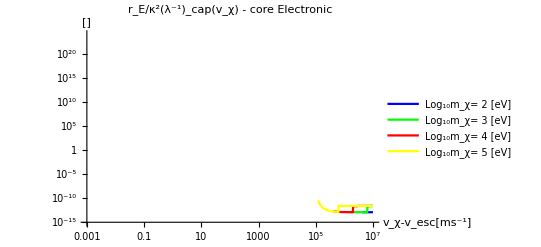

```mathematica
plotstyle= {Blue,Green,Red,Yellow,Orange,Magenta, Brown,Directive[Black, Dashed],Directive[Black, Thick],Directive[Black, Thin]};
LogLogPlot[Evaluate[Table[eind = FirstPosition["mχ"/.ElectronicσDictseD,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
("rE"/.Constants`EarthRepl)GetTotaleWeakCaptureInteractionLength[Gather[ElectronicσDictseD[[eind]],#1["regionindex"]==#2["regionindex"]&][[1]]][vχ+"vesc"/.Constants`EarthRepl]
,{m,2,5}]],{vχ,10^-4,(10^7)-"vesc"/.Constants`EarthRepl},AxesLabel->{"v_χ-v_esc[ms^-1]","[]"},PlotLabel->"r_E/κ^2(λ^-1)_cap(v_χ) - core Electronic",PlotStyle->plotstyle,PlotLegends->LineLegend[plotstyle,Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,2,5}]],PlotRange->{{10^-3,10^7-"vesc"/.Constants`EarthRepl},{10^-15,10^24}}]
```

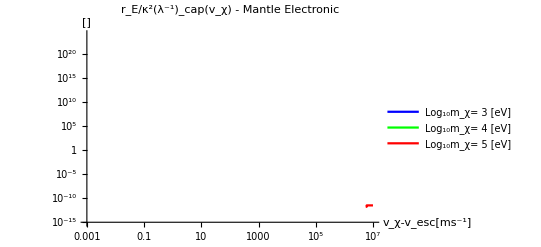

```mathematica
plotstyle= {Blue,Green,Red,Yellow,Orange,Magenta, Brown,Directive[Black, Dashed],Directive[Black, Thick],Directive[Black, Thin]};
LogLogPlot[Evaluate[Table[eind = FirstPosition["mχ"/.ElectronicσDictseD,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
("rE"/.Constants`EarthRepl)GetTotaleWeakCaptureInteractionLength[Gather[ElectronicσDictseD[[eind]],#1["regionindex"]==#2["regionindex"]&][[2]]][vχ+"vesc"/.Constants`EarthRepl]
,{m,3,5}]],{vχ,10^-4,(10^7)-"vesc"/.Constants`EarthRepl},AxesLabel->{"v_χ-v_esc[ms^-1]","[]"},PlotLabel->"r_E/κ^2(λ^-1)_cap(v_χ) - Mantle Electronic",PlotStyle->plotstyle,PlotLegends->LineLegend[plotstyle,Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,3,5}]],PlotRange->{{10^-3,10^7-"vesc"/.Constants`EarthRepl},{10^-15,10^24}}]
```

### Evaporation

#### Evaporation Length

```mathematica
Nucind = FirstPosition["mχ"/.NuclearσDicst10MeVto1PeV,10^7 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]
```

```mathematica
GetEvaporationRate[NuclearσDicst10MeVto1PeV[[Nucind,2]]]
```

11199.1

11200

{{0.049218,7.77815},{-4.,-0.0000434316}}

1.62064×10^8

0.

testing bounds

-0.0000434316

-4.

-4.

1.37417×10^9

```mathematica
N[Log[11199]/Log[10]]
```

4.04918

### Soft vs hard and nuclear vs electronic domination

#### Run Soft Hard E Nuc PDict analysis

```mathematica
Clear[PDictScansComparison]
PDictScansComparison= {};
Block[{NuclearσDictsList,pdicts,PDictind,Nucind,currentPDicts,Scandicts,analysiskeys,NcMaxdict,Ncdict,ScandictsKE},
NuclearσDictsList=NuclearσDicts;
(*pdicts={PDicts1MeVScan,PDicts10MeVScan,PDictsp1GeVScan,PDicts1GeVScan,PDicts10GeVScan,PDicts100GeVScan,PDicts1TeVScan,PDicts10TeVScan,PDicts100TeVScan,PDicts1PeVScan};*)
pdicts = PDictScans;

Monitor[
Do[
Print[p];
(*currentPDicts = pdicts[[p-5]];*)
PDictind=FirstPosition["mpD"/.pdicts,10^p ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
currentPDicts = pdicts[[PDictind]];
Nucind = FirstPosition["mχ"/.NuclearσDictsList,10^p ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
Scandicts={};
Do[
analysiskeys={{"PfE"},{"PfNuc"},{"intλinvE"},{"intλinvNuc"},{"intλinvE","intλinvNuc"}};

Ncdict = currentPDicts[[d]];
Do[
NcMaxdict =GetNcMax[Ncdict,analysiskeys[[k]]];
Ncdict=GetNc[NcMaxdict,NuclearσDictsList[[Nucind]],analysiskeys[[k]]];
,{k,Length[analysiskeys]}];

AppendTo[Scandicts,Ncdict];
,{d,Length[currentPDicts]}];

ScandictsKE=IterateKEchange[Flatten@Scandicts,{0.05},"α"/.Constants`SIConstRepl];

AppendTo[PDictScansComparison,ScandictsKE]

,{p,6,15}]
,p]
]

(*SaveIt[NotebookDirectory[]<>filenames[[p-5]],Scandicts]*)
```

6

ReplaceAll::reps: {InterpolatingFunction[{{4.04922,4.84769},{1.80421,6.75845}},{5,7,0,{40,10},{2,2},0,0,0,0,Automatic,«3»},{{4.04922,4.04922,4.04922,4.04922,4.04922,4.04922,4.04922,4.04922,4.04922,4.04922,«30»},{1.80421,5.80425,6.10525,6.28134,6.40627,6.50318,6.58236,6.64931,6.7073,6.75845}},{Developer`PackedArrayForm,{0,1,2,3,4,5,6,7,8,9,«391»},{-9.10629,-9.10685,-9.02622,-9.09563,-8.94908,-8.9639,-9.01779,-9.08282,-9.11915,-9.19634,«390»}},{Automatic,Automatic}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

The interpolation functions corresponding to these keys have inequivalent domains, so will not be integrated over.

Keys::invrl: The argument … is not a valid Association or a list of rules.

One of these keys is not a valid association for the interpolation dictionary

Keys::invrl: The argument … is not a valid Association or a list of rules.

One of these keys is not a valid association for the interpolation dictionary

Keys::invrl: The argument … is not a valid Association or a list of rules.

General::stop: Further output of Keys::invrl will be suppressed during this calculation.

One of these keys is not a valid association for the interpolation dictionary

One of these keys is not a valid association for the interpolation dictionary

ReplaceAll::reps: {InterpolatingFunction[{{4.04922,4.84769},{1.80421,6.75845}},{5,7,0,{40,10},{2,2},0,0,0,0,Automatic,«3»},{{4.04922,4.04922,4.04922,4.04922,4.04922,4.04922,4.04922,4.04922,4.04922,4.04922,«30»},{1.80421,5.80425,6.10525,6.28134,6.40627,6.50318,6.58236,6.64931,6.7073,6.75845}},{Developer`PackedArrayForm,{0,1,2,3,4,5,6,7,8,9,«391»},{-7.10629,-7.10685,-7.02622,-7.09563,-6.94908,-6.9639,-7.01779,-7.08282,-7.11915,-7.19634,«390»}},{Automatic,Automatic}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

The interpolation functions corresponding to these keys have inequivalent domains, so will not be integrated over.

One of these keys is not a valid association for the interpolation dictionary

One of these keys is not a valid association for the interpolation dictionary

One of these keys is not a valid association for the interpolation dictionary

«1 more identical outputs»

The interpolation functions corresponding to these keys have inequivalent domains, so will not be integrated over.

One of these keys is not a valid association for the interpolation dictionary

One of these keys is not a valid association for the interpolation dictionary

One of these keys is not a valid association for the interpolation dictionary

«1 more identical outputs»

The interpolation functions corresponding to these keys have inequivalent domains, so will not be integrated over.

One of these keys is not a valid association for the interpolation dictionary

One of these keys is not a valid association for the interpolation dictionary

One of these keys is not a valid association for the interpolation dictionary

«1 more identical outputs»

The interpolation functions corresponding to these keys have inequivalent domains, so will not be integrated over.

One of these keys is not a valid association for the interpolation dictionary

One of these keys is not a valid association for the interpolation dictionary

One of these keys is not a valid association for the interpolation dictionary

«1 more identical outputs»

The interpolation functions corresponding to these keys have inequivalent domains, so will not be integrated over.

One of these keys is not a valid association for the interpolation dictionary

One of these keys is not a valid association for the interpolation dictionary

One of these keys is not a valid association for the interpolation dictionary

«1 more identical outputs»

The interpolation functions corresponding to these keys have inequivalent domains, so will not be integrated over.

One of these keys is not a valid association for the interpolation dictionary

One of these keys is not a valid association for the interpolation dictionary

One of these keys is not a valid association for the interpolation dictionary

«1 more identical outputs»

The interpolation functions corresponding to these keys have inequivalent domains, so will not be integrated over.

One of these keys is not a valid association for the interpolation dictionary

One of these keys is not a valid association for the interpolation dictionary

One of these keys is not a valid association for the interpolation dictionary

«1 more identical outputs»

The interpolation functions corresponding to these keys have inequivalent domains, so will not be integrated over.

One of these keys is not a valid association for the interpolation dictionary

One of these keys is not a valid association for the interpolation dictionary

One of these keys is not a valid association for the interpolation dictionary

«1 more identical outputs»

The interpolation functions corresponding to these keys have inequivalent domains, so will not be integrated over.

One of these keys is not a valid association for the interpolation dictionary

One of these keys is not a valid association for the interpolation dictionary

One of these keys is not a valid association for the interpolation dictionary

«1 more identical outputs»

The interpolation functions corresponding to these keys have inequivalent domains, so will not be integrated over.

One of these keys is not a valid association for the interpolation dictionary

One of these keys is not a valid association for the interpolation dictionary

One of these keys is not a valid association for the interpolation dictionary

«1 more identical outputs»

The interpolation functions corresponding to these keys have inequivalent domains, so will not be integrated over.

One of these keys is not a valid association for the interpolation dictionary

One of these keys is not a valid association for the interpolation dictionary

One of these keys is not a valid association for the interpolation dictionary

«1 more identical outputs»

The interpolation functions corresponding to these keys have inequivalent domains, so will not be integrated over.

One of these keys is not a valid association for the interpolation dictionary

One of these keys is not a valid association for the interpolation dictionary

One of these keys is not a valid association for the interpolation dictionary

«1 more identical outputs»

The interpolation functions corresponding to these keys have inequivalent domains, so will not be integrated over.

One of these keys is not a valid association for the interpolation dictionary

One of these keys is not a valid association for the interpolation dictionary

One of these keys is not a valid association for the interpolation dictionary

«1 more identical outputs»

The interpolation functions corresponding to these keys have inequivalent domains, so will not be integrated over.

One of these keys is not a valid association for the interpolation dictionary

One of these keys is not a valid association for the interpolation dictionary

One of these keys is not a valid association for the interpolation dictionary

«1 more identical outputs»

The interpolation functions corresponding to these keys have inequivalent domains, so will not be integrated over.

One of these keys is not a valid association for the interpolation dictionary

One of these keys is not a valid association for the interpolation dictionary

One of these keys is not a valid association for the interpolation dictionary

«1 more identical outputs»

The interpolation functions corresponding to these keys have inequivalent domains, so will not be integrated over.

One of these keys is not a valid association for the interpolation dictionary

One of these keys is not a valid association for the interpolation dictionary

One of these keys is not a valid association for the interpolation dictionary

«1 more identical outputs»

The interpolation functions corresponding to these keys have inequivalent domains, so will not be integrated over.

One of these keys is not a valid association for the interpolation dictionary

One of these keys is not a valid association for the interpolation dictionary

One of these keys is not a valid association for the interpolation dictionary

«1 more identical outputs»

The interpolation functions corresponding to these keys have inequivalent domains, so will not be integrated over.

One of these keys is not a valid association for the interpolation dictionary

One of these keys is not a valid association for the interpolation dictionary

One of these keys is not a valid association for the interpolation dictionary

«1 more identical outputs»

The interpolation functions corresponding to these keys have inequivalent domains, so will not be integrated over.

One of these keys is not a valid association for the interpolation dictionary

One of these keys is not a valid association for the interpolation dictionary

One of these keys is not a valid association for the interpolation dictionary

«1 more identical outputs»

The interpolation functions corresponding to these keys have inequivalent domains, so will not be integrated over.

One of these keys is not a valid association for the interpolation dictionary

One of these keys is not a valid association for the interpolation dictionary

One of these keys is not a valid association for the interpolation dictionary

«1 more identical outputs»

The interpolation functions corresponding to these keys have inequivalent domains, so will not be integrated over.

One of these keys is not a valid association for the interpolation dictionary

One of these keys is not a valid association for the interpolation dictionary

One of these keys is not a valid association for the interpolation dictionary

«1 more identical outputs»

The interpolation functions corresponding to these keys have inequivalent domains, so will not be integrated over.

One of these keys is not a valid association for the interpolation dictionary

One of these keys is not a valid association for the interpolation dictionary

One of these keys is not a valid association for the interpolation dictionary

«1 more identical outputs»

The interpolation functions corresponding to these keys have inequivalent domains, so will not be integrated over.

One of these keys is not a valid association for the interpolation dictionary

One of these keys is not a valid association for the interpolation dictionary

One of these keys is not a valid association for the interpolation dictionary

«1 more identical outputs»

The interpolation functions corresponding to these keys have inequivalent domains, so will not be integrated over.

One of these keys is not a valid association for the interpolation dictionary

One of these keys is not a valid association for the interpolation dictionary

One of these keys is not a valid association for the interpolation dictionary

«1 more identical outputs»

The interpolation functions corresponding to these keys have inequivalent domains, so will not be integrated over.

One of these keys is not a valid association for the interpolation dictionary

One of these keys is not a valid association for the interpolation dictionary

One of these keys is not a valid association for the interpolation dictionary

«1 more identical outputs»

The interpolation functions corresponding to these keys have inequivalent domains, so will not be integrated over.

One of these keys is not a valid association for the interpolation dictionary

One of these keys is not a valid association for the interpolation dictionary

One of these keys is not a valid association for the interpolation dictionary

«1 more identical outputs»

The interpolation functions corresponding to these keys have inequivalent domains, so will not be integrated over.

One of these keys is not a valid association for the interpolation dictionary

One of these keys is not a valid association for the interpolation dictionary

One of these keys is not a valid association for the interpolation dictionary

«1 more identical outputs»

The interpolation functions corresponding to these keys have inequivalent domains, so will not be integrated over.

One of these keys is not a valid association for the interpolation dictionary

One of these keys is not a valid association for the interpolation dictionary

One of these keys is not a valid association for the interpolation dictionary

«1 more identical outputs»

The interpolation functions corresponding to these keys have inequivalent domains, so will not be integrated over.

One of these keys is not a valid association for the interpolation dictionary

One of these keys is not a valid association for the interpolation dictionary

One of these keys is not a valid association for the interpolation dictionary

«1 more identical outputs»

The interpolation functions corresponding to these keys have inequivalent domains, so will not be integrated over.

One of these keys is not a valid association for the interpolation dictionary

One of these keys is not a valid association for the interpolation dictionary

One of these keys is not a valid association for the interpolation dictionary

«1 more identical outputs»

The interpolation functions corresponding to these keys have inequivalent domains, so will not be integrated over.

One of these keys is not a valid association for the interpolation dictionary

One of these keys is not a valid association for the interpolation dictionary

One of these keys is not a valid association for the interpolation dictionary

«1 more identical outputs»

Set::shape: Lists {mpD$37880,meD$37880} and … are not the same shape.

$Aborted

### Comparing to appendix

#### Compare rough scaling of our capture rate to theirs:

```mathematica
("mpD" "βD")^(3/2)ⅇ^(-1/2 "mpD" (vχ^2-("vesc")^2)"βD")/.PDicts10GeVKE[[1]]/.EarthRepl//Simplify;
Integrate[% vχ^3,vχ]
(Limit[%,vχ->∞])-(%/.vχ->0)
```

4.7056×10^-12 ⅇ^(-7.49925×10^-9 vχ^2) (-8.89067×10^15-6.66733×10^7 vχ^2)

41835.9

```mathematica
("mpD" "βD")^(3/2)ⅇ^(-1/2 "mpD" (-("vesc")^2)"βD")/.EarthRepl
```

```mathematica
Integrate[  bE^2/(√(1 + bE^2/("rE")^2)),bE]
(%/.bE->"rE"//FullSimplify)-(%/.bE->0)/.EarthRepl
```

1/2 rE^2 (bE √(1+bE^2/rE^2)-rE ArcSinh[bE/rE])

6.88953×10^19

Discrepancy with appendix is that for us dNc/dt~<v_χ> (r^2)_E n_F whereas for them dNc/dt~<v_χ>1/r_E

So I think it is a discrepancy of definition, the rates to compare to them is R n_F ~ <v_χ>n_F/r_E  which is the rate per unit volume in Earth, so for us the comparison is R n_F ~ <v_χ>n_F/r_E ~ 1/V_E dNc/dt

```mathematica
4/3 π("rE")^3/.EarthRepl
```

1.08321×10^21

#### Compare evaporation rate to appendix

```mathematica
Series[((vT+vχ)^3-((vT-vχ)^2)^(3/2))/(3 vT vχ)/.vT->ϵ vχ,{ϵ,0,2}]//Simplify//Normal//PowerExpand
```

2 vχ+(2 vχ ϵ^2)/3

```mathematica
Integrate[√(vT^2-2vχ vT u  + vχ^2) ,{u,-1,1}]
```

ConditionalExpression[(-((vT-vχ)^2)^(3/2)+((vT+vχ)^2)^(3/2))/(3 vT vχ), ]

1

100000

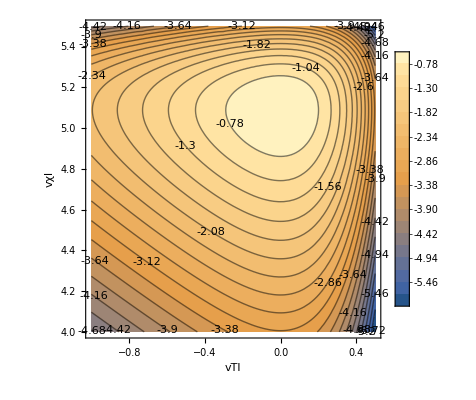

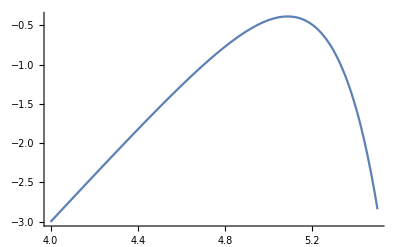

```mathematica
vTbar = 1
vχbar = 100000
ContourPlot[Log10[1/(vχbar^3 vTbar^3)((vT+vχ)^3-((vT-vχ)^2)^(3/2))/(3 vT vχ)vT^2 E^(-  (vT/vTbar)^2)vχ^2 E^(-(vχ/vχbar)^2)/.vχ->10^vχl/.vT->10^vTl],{vTl,Log10[vTbar]-1,0.5 + Log10[vTbar]},{vχl,Log10[vχbar]-1,0.5 + Log10[vχbar]},PlotLegends->Automatic,PlotRange->All,ContourLabels->True,FrameLabel->Automatic,Contours->20]
Plot[Log10[1/vχbar^3 vχ^3 E^(-(vχ/vχbar)^2)/.vχ->10^vχl],{vχl,Log10[vχbar]-1,0.5 + Log10[vχbar]},PlotLegends->Automatic,PlotRange->All,FrameLabel->Automatic]
```

```mathematica
Solve[D[((vT+vχ)^3-((vT-vχ)^2)^(3/2))/(3 vT vχ)vT^2 E^(-  (vT/vTb)^2)vχ^2 E^(-(vχ/vχb)^2),vχ]==0,vχ]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{vχ→0},{vχ→-(√(-3 vT^2+2 vχb^2-√(9 vT^4+4 vχb^4)))/(√2)},{vχ→(√(-3 vT^2+2 vχb^2-√(9 vT^4+4 vχb^4)))/(√2)},{vχ→-√(-(3 vT^2)/2+vχb^2+1/2 √(9 vT^4+4 vχb^4))},{vχ→√(-(3 vT^2)/2+vχb^2+1/2 √(9 vT^4+4 vχb^4))},{vχ→-(√(-2 vT^2+9 vχb^2-√(4 vT^4-12 vT^2 vχb^2+81 vχb^4)))/(2 √3)},{vχ→(√(-2 vT^2+9 vχb^2-√(4 vT^4-12 vT^2 vχb^2+81 vχb^4)))/(2 √3)},{vχ→-(√(-2 vT^2+9 vχb^2+√(4 vT^4-12 vT^2 vχb^2+81 vχb^4)))/(2 √3)},{vχ→(√(-2 vT^2+9 vχb^2+√(4 vT^4-12 vT^2 vχb^2+81 vχb^4)))/(2 √3)}}

#### Get MFP and rough evaporation rate - just average velocity

Look at the rough evaporation rate in the absence of form factors

```mathematica
((mχ βE)/(2 π))^(3/2) 4 π Assuming[{βE,mχ}>0, Integrate[vχ^3 E^(-βE 1/2 mχ vχ^2),{vχ,0,∞}]]//PowerExpand//PowerExpand
```

(2 √(2/π))/(√mχ √βE)

```mathematica
"mχ"/.FeσDictNuc[[1]]
```

1.78×10^-30

```mathematica
κ^2 EvapRate[FeσDictNuc[[7]]][10^4]/.κ->10^-9
```

0.106434

```mathematica
Nucind = FirstPosition["mχ"/.NuclearσDicstnoFF,10^8 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
TotalEvapRateRough[Gather[NuclearσDicstnoFF[[Nucind]],#1["regionindex"]==#2["regionindex"]&][[1]]][10^4]
```

2.63196×10^24

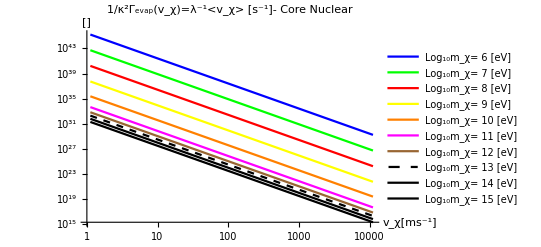

```mathematica
plotstyle= {Blue,Green,Red,Yellow,Orange,Magenta, Brown,Directive[Black, Dashed],Directive[Black, Thick],Directive[Black, Thin]};
LogLogPlot[Evaluate[Table[Nucind = FirstPosition["mχ"/.NuclearσDicstnoFF,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
TotalEvapRateRough[Gather[NuclearσDicstnoFF[[Nucind]],#1["regionindex"]==#2["regionindex"]&][[1]]][vχ]
,{m,6,15}]],{vχ,10^-4"vesc"/.Constants`EarthRepl,"vesc"/.Constants`EarthRepl},AxesLabel->{"v_χ[ms^-1]","[]"},PlotLabel->"1/κ^2Γ_evap(v_χ)=λ^-1<v_χ> [s^-1]- Core Nuclear",PlotStyle->plotstyle,PlotLegends->LineLegend[plotstyle,Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,15}]],PlotRange->Automatic(*{0,10^40}*)]
```

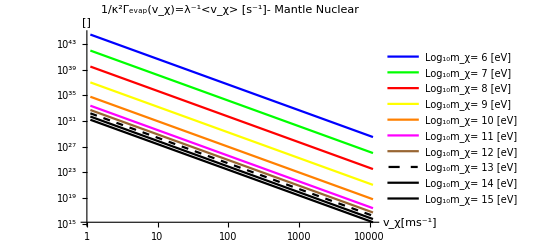

```mathematica
plotstyle= {Blue,Green,Red,Yellow,Orange,Magenta, Brown,Directive[Black, Dashed],Directive[Black, Thick],Directive[Black, Thin]};
LogLogPlot[Evaluate[Table[Nucind = FirstPosition["mχ"/.NuclearσDicstnoFF,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
TotalEvapRateRough[Gather[NuclearσDicstnoFF[[Nucind]],#1["regionindex"]==#2["regionindex"]&][[2]]][vχ]
,{m,6,15}]],{vχ,10^-4"vesc"/.Constants`EarthRepl,"vesc"/.Constants`EarthRepl},AxesLabel->{"v_χ[ms^-1]","[]"},PlotLabel->"1/κ^2Γ_evap(v_χ)=λ^-1<v_χ> [s^-1]- Mantle Nuclear",PlotStyle->plotstyle,PlotLegends->LineLegend[plotstyle,Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,15}]],PlotRange->Automatic(*{0,10^40}*)]
```

Upshot: this is a bad way to compute the evaporation rate, it is much to high. We should make sure we match on to the appendix. We should also compute these plots with our more sophisticated treatment.

#### Get MFP and rough evaporation rate - via appendix eqn A.56

Find Pejection

```mathematica
4 π ((mχ βE)/(2 π))^(3/2) vχ^2 E^(-βE mχ/2 vχ^2)(*fmb*);
Integrate[%,{vχ,0,∞}]//Normal//Simplify
```

1

```mathematica
4 π ((mχ βE)/(2 π))^(3/2) vχ^2 E^(-βE mχ/2 vχ^2)(*fmb*);
Integrate[%,vχ];
Limit[%,vχ->∞]-(%/.vχ->vesc);
Pejection = %//Normal
```

1-√(2/π) (mχ βE)^(3/2) (-(ⅇ^(-1/2 mχ vesc^2 βE) vesc)/(mχ βE)+(√(π/2) Erf[(√mχ vesc √βE)/(√2)])/(mχ^(3/2) βE^(3/2)))

```mathematica
(1-√(2/π) (mχ βE)^(3/2) (-(ⅇ^(-1/2 mχ vesc^2 βE) vesc)/(mχ βE)+(√(π/2) Erf[(√mχ vesc √βE)/(√2)])/(mχ^(3/2) βE^(3/2))))
```

```mathematica
Pejection//Simplify//PowerExpand
```

1+ⅇ^(-1/2 mχ vesc^2 βE) √mχ √(2/π) vesc √βE-Erf[(√mχ vesc √βE)/(√2)]

```mathematica
Log10@(Pejection//Simplify//PowerExpand)/.βE->("βcore"/.EarthRepl)/.vesc->("vesc"/.EarthRepl)/.mχ->10^-29
```

-0.000246006

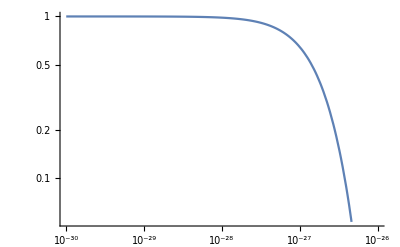

```mathematica
LogLogPlot[(Pejection//Simplify//PowerExpand)/.βE->("βcore"/.EarthRepl)/.vesc->("vesc"/.EarthRepl),{mχ,10^-30,10^-26}]
```

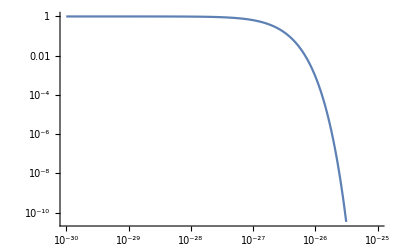

```mathematica
LogLogPlot[(Pejection//Simplify//PowerExpand)/.βE->("βcore"/.EarthRepl)/.vesc->("vesc"/.EarthRepl),{mχ,10^-30,10^-25}]
```

```mathematica
GetTotalAppendixEvaporationRate[Gather[NuclearσDicstnoFF[[3]],#1["regionindex"]==#2["regionindex"]&][[1]]][10^1]
```

8.00624×10^19

0.960858

1.26022×10^31

General::munfl: Exp[-1477.9] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-14779.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-147790.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

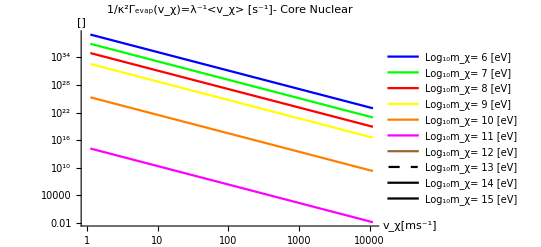

```mathematica
plotstyle= {Blue,Green,Red,Yellow,Orange,Magenta, Brown,Directive[Black, Dashed],Directive[Black, Thick],Directive[Black, Thin]};
LogLogPlot[Evaluate[Table[Nucind = FirstPosition["mχ"/.NuclearσDicstnoFF,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
GetTotalAppendixEvaporationRate[Gather[NuclearσDicstnoFF[[Nucind]],#1["regionindex"]==#2["regionindex"]&][[1]]][vχ]
,{m,6,15}]],{vχ,10^-4"vesc"/.Constants`EarthRepl,"vesc"/.Constants`EarthRepl},AxesLabel->{"v_χ[ms^-1]","[]"},PlotLabel->"1/κ^2Γ_evap(v_χ)=λ^-1<v_χ> [s^-1]- Core Nuclear",PlotStyle->plotstyle,PlotLegends->LineLegend[plotstyle,Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,15}]],PlotRange->Automatic(*{0,10^40}*)]
```

```mathematica
Nucind = FirstPosition["mχ"/.NuclearσDicstnoFF,10^10 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
GetTotalAppendixEvaporationRate[Gather[NuclearσDicstnoFF[[Nucind]],#1["regionindex"]==#2["regionindex"]&][[1]]]
```

3.09621×10^16

```mathematica
"Why are we getting negative evaporation rates for a PeV? Pejection is going negative"
(Pejection//Simplify//PowerExpand)/.βE->("βcore"/.EarthRepl)/.vesc->("vesc"/.EarthRepl)/.mχ->(10^10 ("JpereV")/("c")^2/.Constants`SIConstRepl)
```

Why are we getting negative evaporation rates for a PeV? Pejection is going negative

1.70943×10^-6

```mathematica
GetPejection[Gather[NuclearσDicstnoFF[[Nucind]],#1["regionindex"]==#2["regionindex"]&][[1]][[1]]]
```

0.

```mathematica
(10^-10)^2 GetinvMFT[Gather[NuclearσDicstnoFF[[Nucind]],#1["regionindex"]==#2["regionindex"]&][[1]][[1]]]
```

1105.66

```mathematica
Table[Nucind = FirstPosition["mχ"/.NuclearσDicstnoFF,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
{m,+20+ -Log10@GetTotalinvMFT[Gather[NuclearσDicstnoFF[[Nucind]],#1["regionindex"]==#2["regionindex"]&][[2]]]}
,{m,6,15}]
"This was run with MFT -> MFP. This is λ^-1 for κ=10^-10 The cross-section they use is below. They include screening for the cross-section. We should do the same if we are going to compare directly"
-Graphics-
"Especially since for 10 we should be getting about 10^4 instead of 10^-4"
-Graphics-
```

{{6,-5.08469},{7,-4.585},{8,-4.08811},{9,-3.61859},{10,-3.37609},{11,-3.98113},{12,-5.30867},{13,-6.789},{14,-8.28576},{15,-9.78149}}

This was run with MFT -> MFP. This is λ^-1 for κ=10^-10 The cross-section they use is below. They include screening for the cross-section. We should do the same if we are going to compare directly

-Graphics-

Especially since for 10 we should be getting about 10^4 instead of 10^-4

-Graphics-

```mathematica
Table[Nucind = FirstPosition["mχ"/.NuclearσDicstnoFF,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
{m,+20+ -Log10@GetTotalinvMFT[Gather[NuclearσDicstnoFF[[Nucind]],#1["regionindex"]==#2["regionindex"]&][[2]]]}
,{m,6,15}]
"Putting in the form factor for screening as above, we get the right order of magnitude for κ 10^-10"
```

{{6,1.11865},{7,1.6244},{8,2.18048},{9,3.11631},{10,4.60726},{11,5.46684},{12,5.63539},{13,5.65428},{14,5.65619},{15,5.65638}}

Putting in the form factor for screening as above, we get the right order of magnitude for κ 10^-10

{{{6,-14,-9.8187},{7,-14,-10.322},{8,-14,-10.866},{9,-14,-11.9904},{10,-14,-18.7732},{11,-14,Indeterminate}},{{6,-13,-7.8187},{7,-13,-8.32202},{8,-13,-8.86604},{9,-13,-9.99044},{10,-13,-16.7732},{11,-13,Indeterminate}},{{6,-12,-5.8187},{7,-12,-6.32202},{8,-12,-6.86604},{9,-12,-7.99044},{10,-12,-14.7732},{11,-12,Indeterminate}},{{6,-11,-3.8187},{7,-11,-4.32202},{8,-11,-4.86604},{9,-11,-5.99044},{10,-11,-12.7732},{11,-11,Indeterminate}},{{6,-10,-1.8187},{7,-10,-2.32202},{8,-10,-2.86604},{9,-10,-3.99044},{10,-10,-10.7732},{11,-10,Indeterminate}},{{6,-9,0.181303},{7,-9,-0.322019},{8,-9,-0.866041},{9,-9,-1.99044},{10,-9,-8.77321},{11,-9,Indeterminate}},{{6,-8,2.1813},{7,-8,1.67798},{8,-8,1.13396},{9,-8,0.00956202},{10,-8,-6.77321},{11,-8,Indeterminate}},{{6,-7,4.1813},{7,-7,3.67798},{8,-7,3.13396},{9,-7,2.00956},{10,-7,-4.77321},{11,-7,Indeterminate}}}

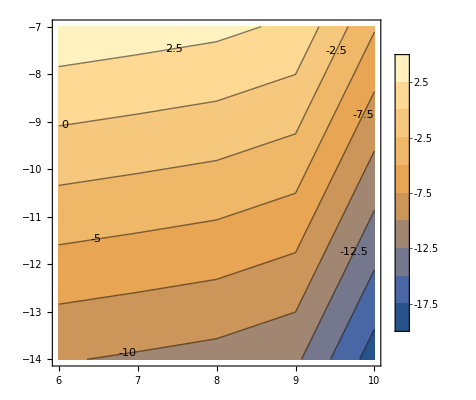

```mathematica
Table[Table[Nucind = FirstPosition["mχ"/.NuclearσDicstnoFF,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
{m,κ, 2 κ +Log10@GetTotalAppendixEvaporationRate[Gather[NuclearσDicstnoFF[[Nucind]],#1["regionindex"]==#2["regionindex"]&][[1]]]}
,{m,6,11}],{κ,-14,-7}]
ListContourPlot[Flatten[%,1],PlotLegends->Automatic,ContourLabels->True,FrameLabel->Automatic]
```

No FFs

{{{6,-14,-9.8187},{7,-14,-10.322},{8,-14,-10.866},{9,-14,-11.9904},{10,-14,-18.7732},{11,-14,Indeterminate}},{{6,-13,-7.8187},{7,-13,-8.32202},{8,-13,-8.86604},{9,-13,-9.99044},{10,-13,-16.7732},{11,-13,Indeterminate}},{{6,-12,-5.8187},{7,-12,-6.32202},{8,-12,-6.86604},{9,-12,-7.99044},{10,-12,-14.7732},{11,-12,Indeterminate}},{{6,-11,-3.8187},{7,-11,-4.32202},{8,-11,-4.86604},{9,-11,-5.99044},{10,-11,-12.7732},{11,-11,Indeterminate}},{{6,-10,-1.8187},{7,-10,-2.32202},{8,-10,-2.86604},{9,-10,-3.99044},{10,-10,-10.7732},{11,-10,Indeterminate}},{{6,-9,0.181303},{7,-9,-0.322019},{8,-9,-0.866041},{9,-9,-1.99044},{10,-9,-8.77321},{11,-9,Indeterminate}},{{6,-8,2.1813},{7,-8,1.67798},{8,-8,1.13396},{9,-8,0.00956202},{10,-8,-6.77321},{11,-8,Indeterminate}},{{6,-7,4.1813},{7,-7,3.67798},{8,-7,3.13396},{9,-7,2.00956},{10,-7,-4.77321},{11,-7,Indeterminate}}}

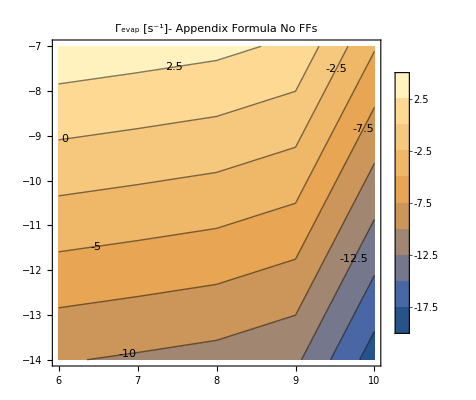

```mathematica
"No FFs"
Table[Table[Nucind = FirstPosition["mχ"/.NuclearσDicstnoFF,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
{m,κ, 2 κ +Log10@GetTotalAppendixEvaporationRate[Gather[NuclearσDicstnoFF[[Nucind]],#1["regionindex"]==#2["regionindex"]&][[1]]]}
,{m,6,11}],{κ,-14,-7}]
ListContourPlot[Flatten[%,1],PlotLegends->Automatic,ContourLabels->True,FrameLabel->Automatic,FrameLabel->{"Log_10m_pD [eV]","Log_10κ [ ]"},PlotLabel->"Γ_evap [s^-1]- Appendix Formula No FFs"]
```

W FFs

{{{6,-14,-21.9441},{7,-14,-18.4559},{8,-14,-15.4065},{9,-14,-14.2751},{10,-14,-19.8792},{11,-14,Indeterminate}},{{6,-13,-19.9441},{7,-13,-16.4559},{8,-13,-13.4065},{9,-13,-12.2751},{10,-13,-17.8792},{11,-13,Indeterminate}},{{6,-12,-17.9441},{7,-12,-14.4559},{8,-12,-11.4065},{9,-12,-10.2751},{10,-12,-15.8792},{11,-12,Indeterminate}},{{6,-11,-15.9441},{7,-11,-12.4559},{8,-11,-9.40654},{9,-11,-8.27512},{10,-11,-13.8792},{11,-11,Indeterminate}},{{6,-10,-13.9441},{7,-10,-10.4559},{8,-10,-7.40654},{9,-10,-6.27512},{10,-10,-11.8792},{11,-10,Indeterminate}},{{6,-9,-11.9441},{7,-9,-8.45586},{8,-9,-5.40654},{9,-9,-4.27512},{10,-9,-9.87923},{11,-9,Indeterminate}},{{6,-8,-9.94414},{7,-8,-6.45586},{8,-8,-3.40654},{9,-8,-2.27512},{10,-8,-7.87923},{11,-8,Indeterminate}},{{6,-7,-7.94414},{7,-7,-4.45586},{8,-7,-1.40654},{9,-7,-0.27512},{10,-7,-5.87923},{11,-7,Indeterminate}}}

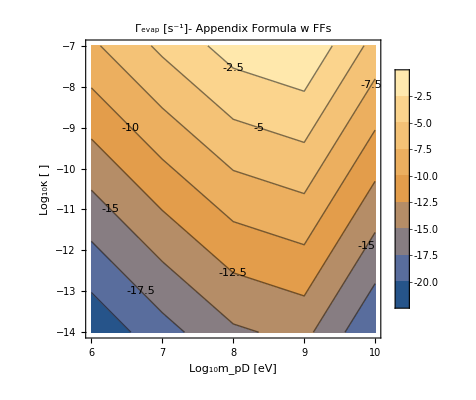

```mathematica
"W FFs"
Table[Table[Nucind = FirstPosition["mχ"/.NuclearσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
{m,κ, 2 κ +Log10@GetTotalAppendixEvaporationRate[Gather[NuclearσDicts[[Nucind]],#1["regionindex"]==#2["regionindex"]&][[1]]]}
,{m,6,11}],{κ,-14,-7}]
ListContourPlot[Flatten[%,1],PlotLegends->Automatic,ContourLabels->True,FrameLabel->{"Log_10m_pD [eV]","Log_10κ [ ]"},PlotLabel->"Γ_evap [s^-1]- Appendix Formula w FFs"]
```

#### Debug - Reproduce Figure 7 - E and Nuc vs Total

{{1/100000000000000,1.00011},{1/10000000000000,1.00011},{1/1000000000000,1.00011},{1/100000000000,1.00012},{1/10000000000,1.00012},{1/1000000000,2.76174×10^16},{1/100000000,3.41161×10^62},{1/10000000,4.9894×10^99}}

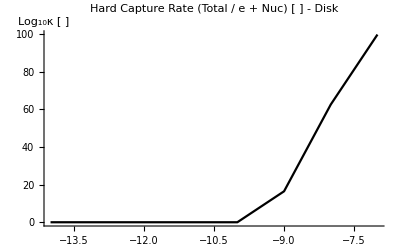

```mathematica
(4π)/3("rE")^3/.Constants`EarthRepl;
Gather[Table[{N@"κ","v0",("meD")/("mpD"),("dNcMaxdt"/.PDictScansComparison[[Nucind10GeV]][[i]])/("dNcMaxdt_intλinvNuc"+"dNcMaxdt_intλinvE"/.PDictScansComparison[[Nucind10GeV]][[i]])}/.PDictScansComparison[[Nucind10GeV]][[i]],{i,Length[PDictScansComparison[[Nucind10GeV]]]}],#1[[3]]==#2[[3]]&&#1[[2]]==#2[[2]]&];
Table[{%[[1]][[i,1]],%[[1]][[i,4]]},{i,Length[%[[1]]]}]
ListLinePlot[Log10@%,PlotLabel->"Hard Capture Rate (Total / e + Nuc) [ ] - Disk",AxesLabel->"Log_10κ [ ]",PlotStyle->Black]
```

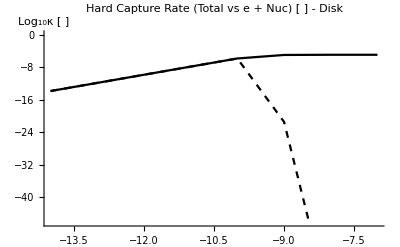

```mathematica
(4π)/3("rE")^3/.Constants`EarthRepl;
Gather[Table[{N@"κ","v0",("meD")/("mpD"),10^-6/%("dNcMaxdt"/.PDictScansComparison[[Nucind10GeV]][[i]])}/.PDictScansComparison[[Nucind10GeV]][[i]],{i,Length[PDictScansComparison[[Nucind10GeV]]]}],#1[[3]]==#2[[3]]&&#1[[2]]==#2[[2]]&];
Gather[Table[{N@"κ","v0",("meD")/("mpD"),10^-6/(%%)("dNcMaxdt_intλinvNuc"+"dNcMaxdt_intλinvE"/.PDictScansComparison[[Nucind10GeV]][[i]])}/.PDictScansComparison[[Nucind10GeV]][[i]],{i,Length[PDictScansComparison[[Nucind10GeV]]]}],#1[[3]]==#2[[3]]&&#1[[2]]==#2[[2]]&];
{Table[{%%[[1]][[i,1]],%%[[1]][[i,4]]},{i,Length[%%[[1]]]}],Table[{%[[1]][[i,1]],%[[1]][[i,4]]},{i,Length[%[[1]]]}]};
ListLinePlot[Log10@%,PlotLabel->"Hard Capture Rate (Total vs e + Nuc) [ ] - Disk ",AxesLabel->"Log_10κ [ ]",PlotStyle->{Black,Directive[Dashed,Black]}]
```

{{1/100000000000000,1.52974×10^6},{1/10000000000000,1.52976×10^6},{1/1000000000000,1.52982×10^6},{1/100000000000,1.52987×10^6},{1/10000000000,1.52991×10^6},{1/1000000000,1.3536×10^15},{1/100000000,1.66012×10^25},{1/10000000,6.14982×10^26}}

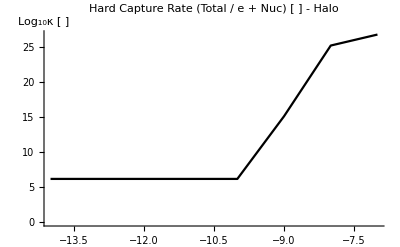

```mathematica
(4π)/3("rE")^3/.Constants`EarthRepl;
Gather[Table[{N@"κ","v0",("meD")/("mpD"),("dNcMaxdt"/.PDictScansComparison[[Nucind10GeV]][[i]])/("dNcMaxdt_intλinvNuc"+"dNcMaxdt_intλinvE"/.PDictScansComparison[[Nucind10GeV]][[i]])}/.PDictScansComparison[[Nucind10GeV]][[i]],{i,Length[PDictScansComparison[[Nucind10GeV]]]}],#1[[3]]==#2[[3]]&&#1[[2]]==#2[[2]]&];
Table[{%[[2]][[i,1]],%[[2]][[i,4]]},{i,Length[%[[2]]]}]
ListLinePlot[Log10@%,PlotLabel->"Hard Capture Rate (Total / e + Nuc) [ ] - Halo",AxesLabel->"Log_10κ [ ]",PlotStyle->Black]
```

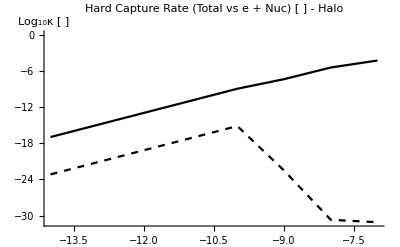

```mathematica
(4π)/3("rE")^3/.Constants`EarthRepl;
Gather[Table[{N@"κ","v0",("meD")/("mpD"),10^-6/%("dNcMaxdt"/.PDictScansComparison[[Nucind10GeV]][[i]])}/.PDictScansComparison[[Nucind10GeV]][[i]],{i,Length[PDictScansComparison[[Nucind10GeV]]]}],#1[[3]]==#2[[3]]&&#1[[2]]==#2[[2]]&];
Gather[Table[{N@"κ","v0",("meD")/("mpD"),10^-6/(%%)("dNcMaxdt_intλinvNuc"+"dNcMaxdt_intλinvE"/.PDictScansComparison[[Nucind10GeV]][[i]])}/.PDictScansComparison[[Nucind10GeV]][[i]],{i,Length[PDictScansComparison[[Nucind10GeV]]]}],#1[[3]]==#2[[3]]&&#1[[2]]==#2[[2]]&];
{Table[{%%[[2]][[i,1]],%%[[2]][[i,4]]},{i,Length[%%[[2]]]}],Table[{%[[2]][[i,1]],%[[2]][[i,4]]},{i,Length[%[[2]]]}]};
ListLinePlot[Log10@%,PlotLabel->"Hard Capture Rate (Total vs e + Nuc) [ ] - Halo",AxesLabel->"Log_10κ [ ]",PlotStyle->{Black,Directive[Dashed,Black]}]
```

{{1/100000000000000,1.52974×10^6},{1/10000000000000,1.52976×10^6},{1/1000000000000,1.52982×10^6},{1/100000000000,1.52987×10^6},{1/10000000000,1.52991×10^6},{1/1000000000,0.505988},{1/100000000,0.50498},{1/10000000,0.50271}}

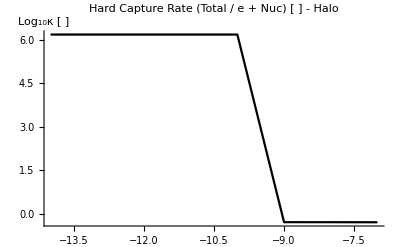

```mathematica
(4π)/3("rE")^3/.Constants`EarthRepl;
Gather[Table[{N@"κ","v0",("meD")/("mpD"),("dNcMaxdt"/.PDictScansComparison[[Nucind10GeV]][[i]])/("dNcMaxdt_PfE"+"dNcMaxdt_PfNuc"/.PDictScansComparison[[Nucind10GeV]][[i]])}/.PDictScansComparison[[Nucind10GeV]][[i]],{i,Length[PDictScansComparison[[Nucind10GeV]]]}],#1[[3]]==#2[[3]]&&#1[[2]]==#2[[2]]&];
Table[{%[[2]][[i,1]],%[[2]][[i,4]]},{i,Length[%[[2]]]}]
ListLinePlot[Log10@%,PlotLabel->"Hard Capture Rate (Total / e + Nuc) [ ] - Halo",AxesLabel->"Log_10κ [ ]",PlotStyle->Black]
```

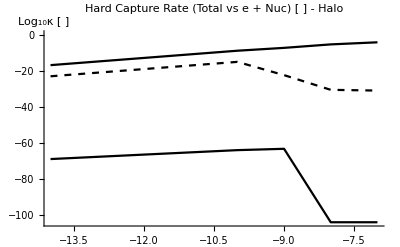

```mathematica
(4π)/3("rE")^3/.Constants`EarthRepl;
Gather[Table[{N@"κ","v0",("meD")/("mpD"),10^-6/%("dNcMaxdt"/.PDictScansComparison[[Nucind10GeV]][[i]])}/.PDictScansComparison[[Nucind10GeV]][[i]],{i,Length[PDictScansComparison[[Nucind10GeV]]]}],#1[[3]]==#2[[3]]&&#1[[2]]==#2[[2]]&];
Gather[Table[{N@"κ","v0",("meD")/("mpD"),10^-6/(%%)("dNcMaxdt_intλinvE"/.PDictScansComparison[[Nucind10GeV]][[i]])}/.PDictScansComparison[[Nucind10GeV]][[i]],{i,Length[PDictScansComparison[[Nucind10GeV]]]}],#1[[3]]==#2[[3]]&&#1[[2]]==#2[[2]]&];
Gather[Table[{N@"κ","v0",("meD")/("mpD"),10^-6/(%%%)("dNcMaxdt_intλinvNuc"/.PDictScansComparison[[Nucind10GeV]][[i]])}/.PDictScansComparison[[Nucind10GeV]][[i]],{i,Length[PDictScansComparison[[Nucind10GeV]]]}],#1[[3]]==#2[[3]]&&#1[[2]]==#2[[2]]&];
{Table[{%%%[[2]][[i,1]],%%%[[2]][[i,4]]},{i,Length[%%%[[2]]]}],Table[{%%[[2]][[i,1]],%%[[2]][[i,4]]},{i,Length[%%[[2]]]}],Table[{%[[2]][[i,1]],%[[2]][[i,4]]},{i,Length[%[[2]]]}]};
ListLinePlot[Log10@%,PlotLabel->"Hard Capture Rate (Total vs e + Nuc) [ ] - Halo",AxesLabel->"Log_10κ [ ]",PlotStyle->{Black,Directive[Dashed,Black]},PlotRange->All]
```

```mathematica
({"v0",("meD")/("mpD"),N@Log10@"κ","dNcMaxdt_intλinvE"}/.PDictScansComparison[[Nucind10GeV]])
({"v0",("meD")/("mpD"),N@Log10@"κ","dNcMaxdt"}/.PDictScansComparison[[Nucind10GeV]])
({"v0",("meD")/("mpD"),N@Log10@"κ","dNcMaxdt_intλinvNuc"}/.PDictScansComparison[[Nucind10GeV]])
```

{{20000,0.0001,-14.,6482.68 nD},{20000,0.0001,-13.,648249. nD},{20000,0.0001,-12.,6.48227×10^7 nD},{20000,0.0001,-11.,6.48206×10^9 nD},{20000,0.0001,-10.,6.48186×10^11 nD},{20000,0.0001,-9.,253.607 nD},{20000,0.0001,-8.,2.27952×10^-44 nD},{20000,0.0001,-7.,7.79332×10^-82 nD},{220000,0.0001,-14.,4.98307 nD},{220000,0.0001,-13.,498.302 nD},{220000,0.0001,-12.,49828.3 nD},{220000,0.0001,-11.,4.98267×10^6 nD},{220000,0.0001,-10.,4.98251×10^8 nD},{220000,0.0001,-9.,21.7258 nD},{220000,0.0001,-8.,1.50242×10^-7 nD},{220000,0.0001,-7.,5.8434×10^-8 nD},{20000,0.01,-14.,6387.3 nD},{20000,0.01,-13.,638717. nD},{20000,0.01,-12.,6.38696×10^7 nD},{20000,0.01,-11.,6.38675×10^9 nD},{20000,0.01,-10.,6.38655×10^11 nD},{20000,0.01,-9.,244.635 nD},{20000,0.01,-8.,2.24407×10^-44 nD},{20000,0.01,-7.,7.79934×10^-82 nD},{220000,0.01,-14.,4.91565 nD},{220000,0.01,-13.,491.564 nD},{220000,0.01,-12.,49154.7 nD},{220000,0.01,-11.,4.91531×10^6 nD},{220000,0.01,-10.,4.91516×10^8 nD},{220000,0.01,-9.,20.3296 nD},{220000,0.01,-8.,1.48698×10^-7 nD},{220000,0.01,-7.,5.86065×10^-8 nD}}

{{20000,0.0001,-14.,9.54706×10^9 nD},{20000,0.0001,-13.,9.54705×10^11 nD},{20000,0.0001,-12.,9.54703×10^13 nD},{20000,0.0001,-11.,9.54702×10^15 nD},{20000,0.0001,-10.,9.54701×10^17 nD},{20000,0.0001,-9.,7.00397×10^18 nD},{20000,0.0001,-8.,7.77681×10^18 nD},{20000,0.0001,-7.,7.77681×10^18 nD},{220000,0.0001,-14.,7.62281×10^6 nD},{220000,0.0001,-13.,7.62281×10^8 nD},{220000,0.0001,-12.,7.62281×10^10 nD},{220000,0.0001,-11.,7.62281×10^12 nD},{220000,0.0001,-10.,7.62281×10^14 nD},{220000,0.0001,-9.,2.9408×10^16 nD},{220000,0.0001,-8.,2.49419×10^18 nD},{220000,0.0001,-7.,3.59359×10^19 nD},{20000,0.01,-14.,9.41133×10^9 nD},{20000,0.01,-13.,9.41132×10^11 nD},{20000,0.01,-12.,9.4113×10^13 nD},{20000,0.01,-11.,9.41129×10^15 nD},{20000,0.01,-10.,9.41128×10^17 nD},{20000,0.01,-9.,6.9975×10^18 nD},{20000,0.01,-8.,7.77807×10^18 nD},{20000,0.01,-7.,7.77807×10^18 nD},{220000,0.01,-14.,7.51877×10^6 nD},{220000,0.01,-13.,7.51877×10^8 nD},{220000,0.01,-12.,7.51877×10^10 nD},{220000,0.01,-11.,7.51877×10^12 nD},{220000,0.01,-10.,7.51877×10^14 nD},{220000,0.01,-9.,2.93012×10^16 nD},{220000,0.01,-8.,2.50059×10^18 nD},{220000,0.01,-7.,3.61029×10^19 nD}}

{{20000,0.0001,-14.,9.54605×10^9 nD},{20000,0.0001,-13.,9.546×10^11 nD},{20000,0.0001,-12.,9.54595×10^13 nD},{20000,0.0001,-11.,9.54591×10^15 nD},{20000,0.0001,-10.,9.54586×10^17 nD},{20000,0.0001,-9.,7.79332×10^-82 nD},{20000,0.0001,-8.,7.79332×10^-82 nD},{20000,0.0001,-7.,7.79332×10^-82 nD},{220000,0.0001,-14.,5.70908×10^-46 nD},{220000,0.0001,-13.,9.88982×10^-45 nD},{220000,0.0001,-12.,1.71321×10^-43 nD},{220000,0.0001,-11.,2.96778×10^-42 nD},{220000,0.0001,-10.,5.14108×10^-41 nD},{220000,0.0001,-9.,2.81116×10^-40 nD},{220000,0.0001,-8.,4.89092×10^-81 nD},{220000,0.0001,-7.,4.89092×10^-81 nD},{20000,0.01,-14.,9.41035×10^9 nD},{20000,0.01,-13.,9.4103×10^11 nD},{20000,0.01,-12.,9.41023×10^13 nD},{20000,0.01,-11.,9.41019×10^15 nD},{20000,0.01,-10.,9.41015×10^17 nD},{20000,0.01,-9.,7.79934×10^-82 nD},{20000,0.01,-8.,7.79934×10^-82 nD},{20000,0.01,-7.,7.79934×10^-82 nD},{220000,0.01,-14.,3.17201×10^-46 nD},{220000,0.01,-13.,5.4937×10^-45 nD},{220000,0.01,-12.,9.51469×10^-44 nD},{220000,0.01,-11.,1.64788×10^-42 nD},{220000,0.01,-10.,2.854×10^-41 nD},{220000,0.01,-9.,1.56027×10^-40 nD},{220000,0.01,-8.,4.91432×10^-81 nD},{220000,0.01,-7.,4.91432×10^-81 nD}}

#### Debug - Reproduce Figure 7 - rerun comparison analysis

```mathematica
Clear[PDictComparisonTemp]
PDictComparisonTemp ={};

Block[{NuclearσDictsList,pdicts,PDictind,Nucind,currentPDicts,Scandicts,analysiskeys,NcMaxdict,Ncdict,ScandictsKE,p=10},

NuclearσDictsList=NuclearσDicts;
pdicts = PDictScans;

PDictind=FirstPosition["mpD"/.PDictScans,10^p ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
currentPDicts = pdicts[[PDictind]];
Nucind = FirstPosition["mχ"/.NuclearσDictsList,10^p ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
Scandicts={};
Do[
analysiskeys={{"Pf"},{"PfE"},{"PfNuc"},{"intλinvE"},{"intλinvNuc"}};

Ncdict = currentPDicts[[d]];
Print["v0"/.Ncdict];
Do[
Print[analysiskeys[[k]]];

NcMaxdict =GetNcMax[Ncdict,analysiskeys[[k]]];
Ncdict=GetNc[NcMaxdict,NuclearσDictsList[[Nucind]],analysiskeys[[k]]];
,{k,Length[analysiskeys]}];

AppendTo[Scandicts,Ncdict];
,{d,Length[currentPDicts]}];

ScandictsKE=IterateKEchange[Flatten@Scandicts,{0.05},"α"/.Constants`SIConstRepl];

AppendTo[PDictComparisonTemp,ScandictsKE]

];
```

{20000,20000,20000,20000,20000,20000,20000,20000}

{Pf}

{PfE}

{PfNuc}

{intλinvE}

{intλinvNuc}

{220000,220000,220000,220000,220000,220000,220000,220000}

{Pf}

7.62007×10^10 nD

{PfE}

60601.6 nD

{PfNuc}

7.6199×10^10 nD

{intλinvE}

60601.6 nD

{intλinvNuc}

7.6199×10^10 nD

{20000,20000,20000,20000,20000,20000,20000,20000}

{Pf}

{PfE}

{PfNuc}

{intλinvE}

{intλinvNuc}

{220000,220000,220000,220000,220000,220000,220000,220000}

{Pf}

7.51656×10^10 nD

{PfE}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

49141.1 nD

{PfNuc}

7.51639×10^10 nD

{intλinvE}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

49141.1 nD

{intλinvNuc}

7.51639×10^10 nD

#### Reproduce Figure 7 - Final

```mathematica
Nucind10GeV = FirstPosition["mpD"/.PDictScans,10^10 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]
```

5

{{{1/1000000000,3.89679×10^-8},{1/100000000,3.35488×10^-6},{1/10000000,0.0000504782}},{{1/100000000000000,1.16788×10^-17},{1/10000000000000,1.16788×10^-15},{1/1000000000000,1.16788×10^-13},{1/100000000000,1.16788×10^-11},{1/10000000000,1.16788×10^-9}}}

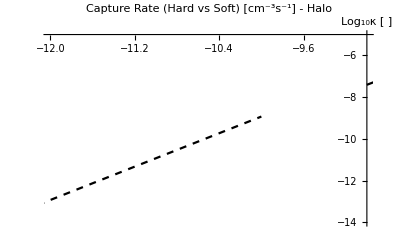

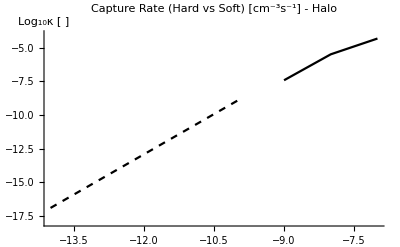

```mathematica
(4π)/3("rE")^3/.Constants`EarthRepl;
Gather[Table[{N@"κ","v0",("meD")/("mpD"),1/(% 10^6)("dNcMaxdt"-"dNcMaxdt_intλinvE"-"dNcMaxdt_intλinvNuc"/.PDictScans[[Nucind10GeV]][[i]])}/.PDictScans[[Nucind10GeV]][[i]],{i,Length[PDictScans[[Nucind10GeV]]]}],#1[[3]]==#2[[3]]&&#1[[2]]==#2[[2]]&];
Gather[Table[{N@"κ","v0",("meD")/("mpD"),1/(%% 10^6)("dNcMaxdt_intλinvE"+"dNcMaxdt_intλinvNuc"/.PDictScans[[Nucind10GeV]][[i]])}/.PDictScans[[Nucind10GeV]][[i]],{i,Length[PDictScans[[Nucind10GeV]]]}],#1[[3]]==#2[[3]]&&#1[[2]]==#2[[2]]&];
{Table[{%%[[2]][[i,1]],%%[[2]][[i,4]]},{i,Length[%%[[1]]]}][[6;;]],Table[{%[[2]][[i,1]],%[[2]][[i,4]]},{i,Length[%[[2]]]}][[;;5]]}
ListLinePlot[Log10@%,PlotRange->{{-12,-9},{-5,-14}},PlotLabel->"Capture Rate (Hard vs Soft) [cm^-3s^-1] - Halo ",AxesLabel->"Log_10κ [ ]",PlotStyle->{Black,Directive[Dashed,Black]}]
ListLinePlot[Log10@%%,PlotRange->{-4,-18},PlotLabel->"Capture Rate (Hard vs Soft) [cm^-3s^-1] - Halo ",AxesLabel->"Log_10κ [ ]",PlotStyle->{Black,Directive[Dashed,Black]}]
```

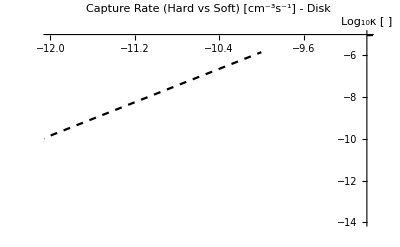

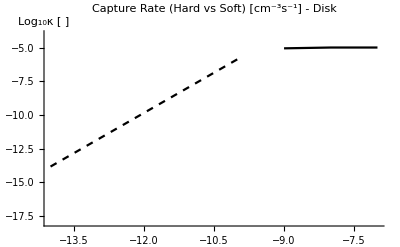

```mathematica
(4π)/3("rE")^3/.Constants`EarthRepl;
Gather[Table[{N@"κ","v0",("meD")/("mpD"),10^-6/%("dNcMaxdt"-"dNcMaxdt_intλinvE"-"dNcMaxdt_intλinvNuc"/.PDictScans[[Nucind10GeV]][[i]])}/.PDictScans[[Nucind10GeV]][[i]],{i,Length[PDictScans[[Nucind10GeV]]]}],#1[[3]]==#2[[3]]&&#1[[2]]==#2[[2]]&];
Gather[Table[{N@"κ","v0",("meD")/("mpD"),10^-6/(%%)("dNcMaxdt_intλinvE"+"dNcMaxdt_intλinvNuc"/.PDictScans[[Nucind10GeV]][[i]])}/.PDictScans[[Nucind10GeV]][[i]],{i,Length[PDictScans[[Nucind10GeV]]]}],#1[[3]]==#2[[3]]&&#1[[2]]==#2[[2]]&];
{Table[{%%[[1]][[i,1]],%%[[1]][[i,4]]},{i,Length[%%[[1]]]}][[6;;]],Table[{%[[1]][[i,1]],%[[1]][[i,4]]},{i,Length[%[[1]]]}][[;;5]]};
ListLinePlot[Log10@%,PlotRange->{{-12,-9},{-5,-14}},PlotLabel->"Capture Rate (Hard vs Soft) [cm^-3s^-1] - Disk ",AxesLabel->"Log_10κ [ ]",PlotStyle->{Black,Directive[Dashed,Black]}]
ListLinePlot[Log10@%%,PlotRange->{-4,-18},PlotLabel->"Capture Rate (Hard vs Soft) [cm^-3s^-1] - Disk ",AxesLabel->"Log_10κ [ ]",PlotStyle->{Black,Directive[Dashed,Black]}]
```

#### Diagnose difference in slopes

```mathematica
Nucind10GeV = FirstPosition["mpD"/.PDictScans,10^10 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]
```

5

20000

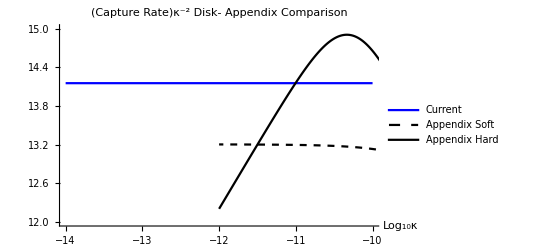

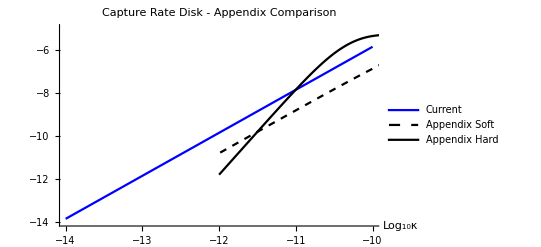

```mathematica
(4π)/3("rE")^3/.Constants`EarthRepl;
Gather[Table[{N@"κ","v0",("meD")/("mpD"),10^-6/%("dNcMaxdt"-"dNcMaxdt_intλinvE"-"dNcMaxdt_intλinvNuc"/.PDictScans[[Nucind10GeV]][[i]])}/.PDictScans[[Nucind10GeV]][[i]],{i,Length[PDictScans[[Nucind10GeV]]]}],#1[[3]]==#2[[3]]&&#1[[2]]==#2[[2]]&];
Gather[Table[{N@"κ","v0",("meD")/("mpD"),10^-6/(%%)("dNcMaxdt_intλinvE"+"dNcMaxdt_intλinvNuc"/.PDictScans[[Nucind10GeV]][[i]])}/.PDictScans[[Nucind10GeV]][[i]],{i,Length[PDictScans[[Nucind10GeV]]]}],#1[[3]]==#2[[3]]&&#1[[2]]==#2[[2]]&];
{Table[{%[[1]][[i,1]],%[[1]][[i,4]]},{i,Length[%[[1]]]}][[;;5]]};
Print[%%[[1,1,2]]];
Flatten[%%,1];
Table[{Log10@%[[i,1]],Log10@((%[[i,2]])/(%[[i,1]])^2)},{i,Length[%]}];
Show[{ListLinePlot[%,PlotLabel->"(Capture Rate)κ^-2 Disk- Appendix Comparison",AxesLabel->{"Log_10κ"},PlotRange->{12,15},PlotStyle->Blue,PlotLegends->LineLegend[{Blue,Directive[Black,Dashed],Black},{"Current","Appendix Soft","Appendix Hard"}]],
ListPlot[Table[{RlistDisk[[2]][[i,1]],Log10@((RlistDisk[[2]][[i,2]])/10^(2 RlistDisk[[2]][[i,1]]))},{i,Length[RlistDisk[[2]]]}],PlotStyle->Directive[Black,Dashed],Joined->True],
ListPlot[Table[{RlistDisk[[1]][[i,1]],Log10@((RlistDisk[[1]][[i,2]])/10^(2 RlistDisk[[1]][[i,1]]))},{i,Length[RlistDisk[[1]]]}],PlotStyle->Black,Joined->True]}]
Table[{Log10@%%%[[i,1]],Log10@%%%[[i,2]]},{i,Length[%%%]}];
Show[{ListLinePlot[%,PlotLabel->"Capture Rate Disk - Appendix Comparison",AxesLabel->{"Log_10κ"},PlotRange->{-5,-14},PlotStyle->Blue,PlotLegends->LineLegend[{Blue,Directive[Black,Dashed],Black},{"Current","Appendix Soft","Appendix Hard"}]],
ListPlot[Table[{RlistDisk[[2]][[i,1]],Log10@RlistDisk[[2]][[i,2]]},{i,Length[RlistDisk[[2]]]}],PlotStyle->Directive[Black,Dashed],Joined->True],ListPlot[Table[{RlistDisk[[1]][[i,1]],Log10@RlistDisk[[1]][[i,2]]},{i,Length[RlistDisk[[1]]]}],PlotStyle->Black,Joined->True]}]
```

This shows that in the hard capture regime, we scale with κ^2 exactly. And for the disk case so does the appendix

220000

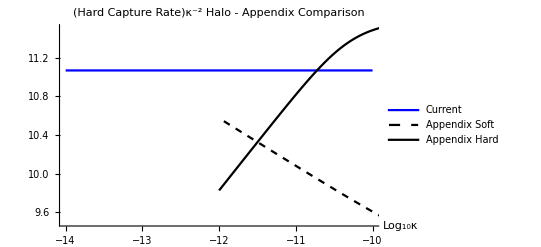

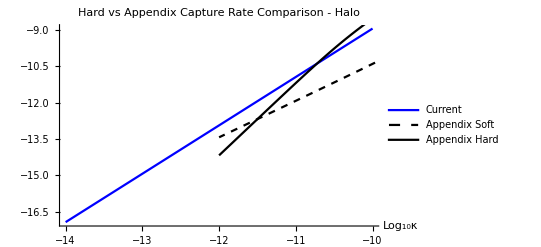

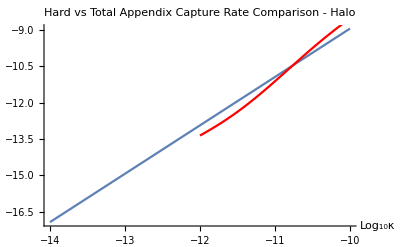

```mathematica
(4π)/3("rE")^3/.Constants`EarthRepl;
Gather[Table[{N@"κ","v0",("meD")/("mpD"),10^-6/%("dNcMaxdt"-"dNcMaxdt_intλinvE"-"dNcMaxdt_intλinvNuc"/.PDictScans[[Nucind10GeV]][[i]])}/.PDictScans[[Nucind10GeV]][[i]],{i,Length[PDictScans[[Nucind10GeV]]]}],#1[[3]]==#2[[3]]&&#1[[2]]==#2[[2]]&];
Gather[Table[{N@"κ","v0",("meD")/("mpD"),10^-6/(%%)("dNcMaxdt_intλinvE"+"dNcMaxdt_intλinvNuc"/.PDictScans[[Nucind10GeV]][[i]])}/.PDictScans[[Nucind10GeV]][[i]],{i,Length[PDictScans[[Nucind10GeV]]]}],#1[[3]]==#2[[3]]&&#1[[2]]==#2[[2]]&];
{Table[{%[[2]][[i,1]],%[[2]][[i,4]]},{i,Length[%[[2]]]}][[;;5]]};
Print[%%[[2,1,2]]]
Flatten[%%,1];
Table[{Log10@%[[i,1]],Log10@((%[[i,2]])/(%[[i,1]])^2)},{i,Length[%]}];
(*ListLinePlot[%,PlotLabel->"(Hard Capture Rate)κ^-2-Halo",AxesLabel->{"Log_10κ"}]*)
Show[{ListLinePlot[%,PlotLabel->"(Hard Capture Rate)κ^-2 Halo - Appendix Comparison",AxesLabel->{"Log_10κ"},PlotRange->{9.5,11.5},PlotStyle->Blue,PlotLegends->LineLegend[{Blue,Directive[Black,Dashed],Black},{"Current","Appendix Soft","Appendix Hard"}]],
ListPlot[Table[{RlistHalo[[2]][[i,1]], Log10@((RlistHalo[[2]][[i,2]])/10^(2 RlistHalo[[2]][[i,1]]))},{i,Length[RlistHalo[[2]]]}],PlotStyle->Directive[Black,Dashed],Joined->True],
ListPlot[Table[{RlistHalo[[1]][[i,1]], Log10@((RlistHalo[[1]][[i,2]])/10^(2 RlistHalo[[1]][[i,1]]))},{i,Length[RlistHalo[[1]]]}],PlotStyle->Black,Joined->True]}]
Table[{Log10@%%%[[i,1]],Log10@%%%[[i,2]]},{i,Length[%%%]}];
Show[{ListLinePlot[%,PlotLabel->"Hard vs Appendix Capture Rate Comparison - Halo",AxesLabel->{"Log_10κ"},PlotStyle->Blue,PlotLegends->LineLegend[{Blue,Directive[Black,Dashed],Black},{"Current","Appendix Soft","Appendix Hard"}]],
ListPlot[Table[{RlistHalo[[2]][[i,1]], Log10@RlistHalo[[2]][[i,2]]},{i,Length[RlistHalo[[2]]]}],PlotStyle->Directive[Black,Dashed],Joined->True],
ListPlot[Table[{RlistHalo[[1]][[i,1]], Log10@RlistHalo[[1]][[i,2]]},{i,Length[RlistHalo[[1]]]}],PlotStyle->Black,Joined->True]}]
Show[{ListLinePlot[%%,PlotLabel->"Hard vs Total Appendix Capture Rate Comparison - Halo",AxesLabel->{"Log_10κ"}],
ListPlot[Table[{RlistHalo[[2]][[i,1]], Log10@(RlistHalo[[2]][[i,2]]+ RlistHalo[[1]][[i,2]])},{i,Length[RlistHalo[[2]]]}],PlotStyle->Red,Joined->True]}]
```

This shows the appendix does not scale with κ^2 but instead scales with a smaller power. We need to understand the scaling from their formulae. 

I think it is because for hard scattering, they assume capture for any velocity such that the MFP is greater than the radius of the Earth (smaller is considered soft scatter captured). So there is some dependence on κ in the velocity interval. 
	We need to understand why our capture rate is higher even though they make this very conservative assumption. 
		For Hard Scatters they also only include the part of phase space not included by soft scatters - so w MFP > r_E. Ours does not include this, and allows arbitrarily slow aDM to be captured by hard scatters. THIS I THINK IS THE MAIN DIFFERENCE
		Another could be related to the fact that we have more targets (they only consider oxygen)
		We also integrate over impact parameter, this is also not likely the main cause since we know that the rough scaling is comparable
		Another competing effect is the form factors
		Obviously bugs are always a possibility

### Evaporation w no FFs

#### Interpolate over Nuclear - all masses - no FFs

```mathematica
FeσDictNucnoFF=Table[InterpolatevχandωσdERNucξ[10^m ("JpereV")/("c")^2/.Constants`SIConstRepl,FeNucCoeffs,2,"Fe Nuc"],{m,6,15}];
SaveIt[NotebookDirectory[]<>"FeσDictNuc_no_FF",FeσDictNucnoFF]
```

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\FeσDictNuc_no_FF.dat

```mathematica
SiσDictNucnoFF=Table[InterpolatevχandωσdERNucξ[10^m ("JpereV")/("c")^2/.Constants`SIConstRepl,SiNucCoeffs,1,"Si Nuc"],{m,6,15}];
SaveIt[NotebookDirectory[]<>"SiσDictNuc_no_FF",SiσDictNucnoFF]
```

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\SiσDictNuc_no_FF.dat

```mathematica
MgσDictNucnoFF=Table[InterpolatevχandωσdERNucξ[10^m ("JpereV")/("c")^2/.Constants`SIConstRepl,MgNucCoeffs,1,"Mg Nuc"],{m,6,15}];
SaveIt[NotebookDirectory[]<>"MgσDictNuc_no_FF",MgσDictNucnoFF]
```

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\MgσDictNuc_no_FF.dat

```mathematica
OσDictNucnoFF=Table[InterpolatevχandωσdERNucξ[10^m ("JpereV")/("c")^2/.Constants`SIConstRepl,SiNucCoeffs,1,"O Nuc"],{m,6,15}];
SaveIt[NotebookDirectory[]<>"OσDictNuc_no_FF",OσDictNucnoFF]
```

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\OσDictNuc_no_FF.dat

```mathematica
FeσDictNucnoFF=ReadIt[NotebookDirectory[]<>"FeσDictNuc_no_FF"];
SiσDictNucnoFF=ReadIt[NotebookDirectory[]<>"SiσDictNuc_no_FF"];
MgσDictNucnoFF=ReadIt[NotebookDirectory[]<>"MgσDictNuc_no_FF"];
OσDictNucnoFF=ReadIt[NotebookDirectory[]<>"OσDictNuc_no_FF"];
```

```mathematica
NuclearσDicstnoFF=Gather[Flatten@Join[{FeσDictNucnoFF},{SiσDictNucnoFF},{MgσDictNucnoFF},{OσDictNucnoFF}],#1["mχ"]==#2["mχ"]&];
```

#### Scan over all masses - no FFs

```mathematica
filenames = {"PDicts1MeVScan","PDicts10MeVScan","PDictsp1GeVScan","PDicts1GeVScan","PDicts10GeVScan","PDicts100GeVScan","PDicts1TeVScan","PDicts10TeVScan","PDicts100TeVScan","PDicts1PeVScan"};
Do[eind = FirstPosition["mχ"/.ElectronicσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
Nucind = FirstPosition["mχ"/.NuclearσDicstnoFF,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
PDictScannoFF=ScanGetCaptureRateandGetNc[meDPoints,κpoints,v0Points,ElectronicσDicts[[eind]],NuclearσDicstnoFF[[Nucind]]];
SaveIt[NotebookDirectory[]<>filenames[[m-5]]<>"_no_FF",PDictScannoFF];
Clear[eind,Nucind,PDictScannoFF];
,{m,6,15}]
```

mpD: 1.×10^6

meD/mpD: 1/10000

v0: 20000

βD: 8.42612×10^21

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 10 recursive bisections in vχ near {vχ,vT} = {11199.999957239255112858796782637771372037605033256113529205322266,1671.1}. NIntegrate obtained 8.59634×10^12 and 3.44881×10^11 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 10 recursive bisections in vχ near {vχ,vT} = {11199.999914486696489256803747035229346096230074181221425533294678,1671.1}. NIntegrate obtained 4.70414×10^12 and 2.13669×10^11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 10 recursive bisections in vχ near {vχ,vT} = {11199.999900237662382339895537214369269918279314879328012466430664,1671.1}. NIntegrate obtained 5.24198×10^12 and 3.13597×10^11 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

meD/mpD: 1/10000

v0: 220000

βD: 6.96374×10^19

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

meD/mpD: 1/100

v0: 20000

βD: 8.34353×10^21

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

meD/mpD: 1/100

v0: 220000

βD: 6.89548×10^19

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^7

meD/mpD: 1/10000

v0: 20000

βD: 8.42612×10^20

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

meD/mpD: 1/10000

v0: 220000

βD: 6.96374×10^18

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

meD/mpD: 1/100

v0: 20000

βD: 8.34353×10^20

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

meD/mpD: 1/100

v0: 220000

βD: 6.89548×10^18

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^8

meD/mpD: 1/10000

v0: 20000

βD: 8.42612×10^19

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

meD/mpD: 1/10000

v0: 220000

βD: 6.96374×10^17

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

meD/mpD: 1/100

v0: 20000

βD: 8.34353×10^19

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

meD/mpD: 1/100

v0: 220000

βD: 6.89548×10^17

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^9

meD/mpD: 1/10000

v0: 20000

βD: 8.42612×10^18

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

meD/mpD: 1/10000

v0: 220000

βD: 6.96374×10^16

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

meD/mpD: 1/100

v0: 20000

βD: 8.34353×10^18

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

meD/mpD: 1/100

v0: 220000

βD: 6.89548×10^16

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^10

meD/mpD: 1/10000

v0: 20000

βD: 8.42612×10^17

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

meD/mpD: 1/10000

v0: 220000

βD: 6.96374×10^15

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

meD/mpD: 1/100

v0: 20000

βD: 8.34353×10^17

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

meD/mpD: 1/100

v0: 220000

βD: 6.89548×10^15

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^11

meD/mpD: 1/10000

v0: 20000

βD: 8.42612×10^16

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

meD/mpD: 1/10000

v0: 220000

βD: 6.96374×10^14

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

meD/mpD: 1/100

v0: 20000

βD: 8.34353×10^16

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

meD/mpD: 1/100

v0: 220000

βD: 6.89548×10^14

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^12

meD/mpD: 1/10000

v0: 20000

βD: 8.42612×10^15

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

meD/mpD: 1/10000

v0: 220000

βD: 6.96374×10^13

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

meD/mpD: 1/100

v0: 20000

βD: 8.34353×10^15

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

meD/mpD: 1/100

v0: 220000

βD: 6.89548×10^13

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^13

meD/mpD: 1/10000

v0: 20000

βD: 8.42612×10^14

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

meD/mpD: 1/10000

v0: 220000

βD: 6.96374×10^12

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

meD/mpD: 1/100

v0: 20000

βD: 8.34353×10^14

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

meD/mpD: 1/100

v0: 220000

βD: 6.89548×10^12

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^14

meD/mpD: 1/10000

v0: 20000

βD: 8.42612×10^13

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

meD/mpD: 1/10000

v0: 220000

βD: 6.96374×10^11

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

meD/mpD: 1/100

v0: 20000

βD: 8.34353×10^13

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

meD/mpD: 1/100

v0: 220000

βD: 6.89548×10^11

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^15

meD/mpD: 1/10000

v0: 20000

βD: 8.42612×10^12

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

meD/mpD: 1/10000

v0: 220000

βD: 6.96374×10^10

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

meD/mpD: 1/100

v0: 20000

βD: 8.34353×10^12

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

meD/mpD: 1/100

v0: 220000

βD: 6.89548×10^10

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

```mathematica
KEDictListnoFF={};
Do[
PDictScannoFF = ReadIt[NotebookDirectory[]<>filenames[[m-5]]<>"_no_FF"];
PDictScanKEnoFF = IterateKEchange[Flatten@PDictScannoFF,{0.05},"α"/.Constants`SIConstRepl];
AppendTo[KEDictListnoFF,PDictScanKEnoFF];
Clear[PDictScannoFF,PDictScanKEnoFF];
,{m,6,15}]
```

```mathematica
?FormFactors`Zeff
```

```mathematica
Dimensions[KEDictListnoFF]
```

{10,32}

#### Get Plots - no FFS

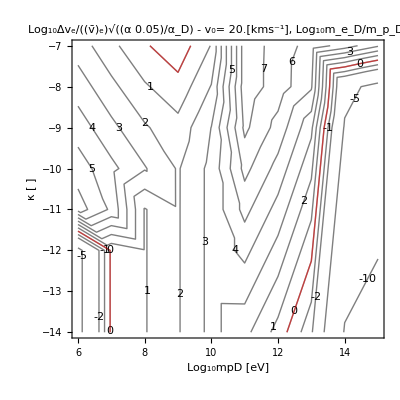

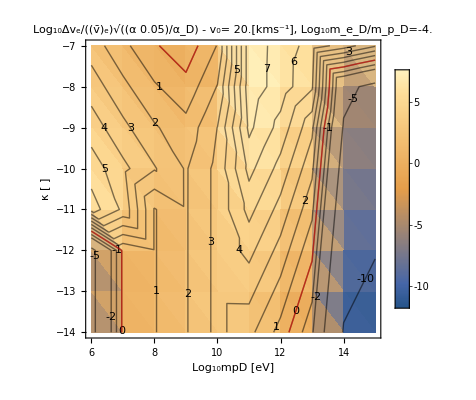

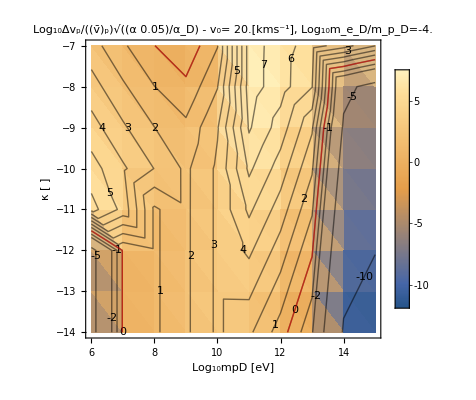

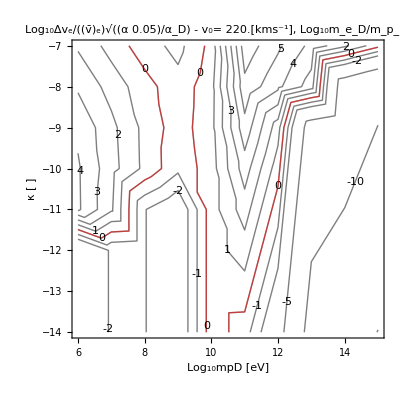

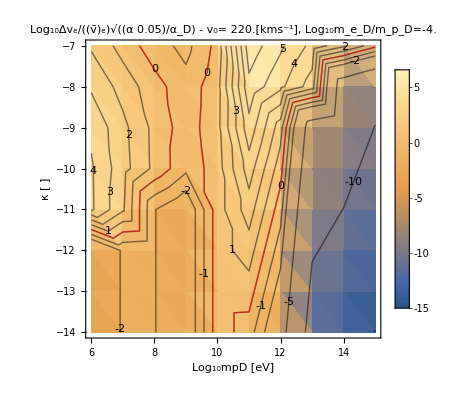

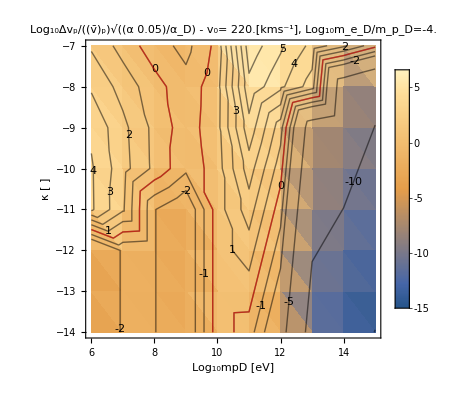

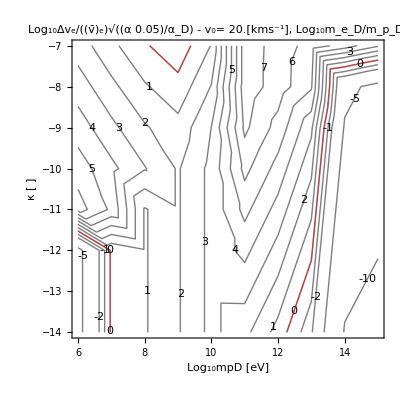

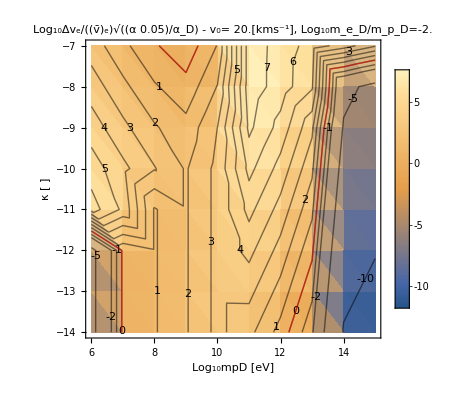

```mathematica
PlotKEchangeκContour[KEDictListnoFF]
```

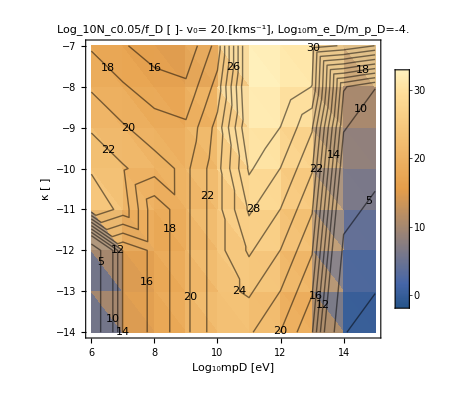

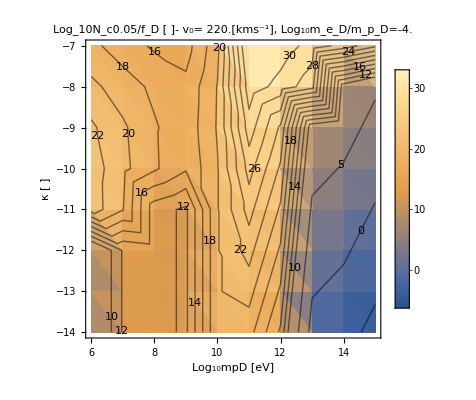

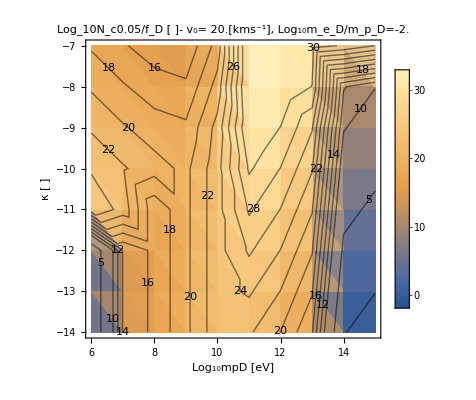

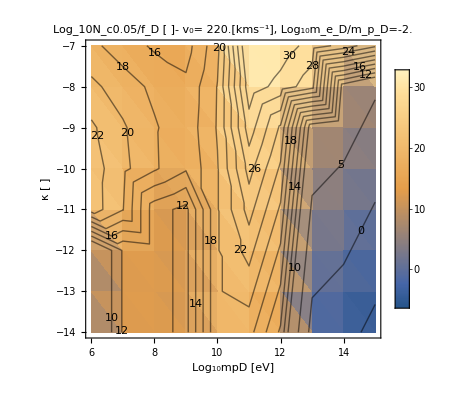

```mathematica
PlotNcκContour[KEDictListnoFF]
```

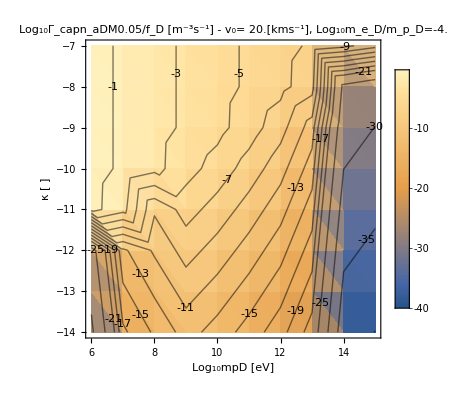

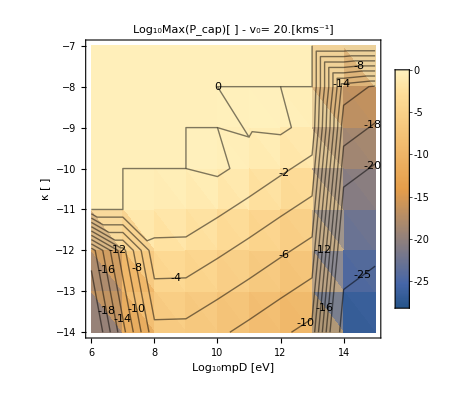

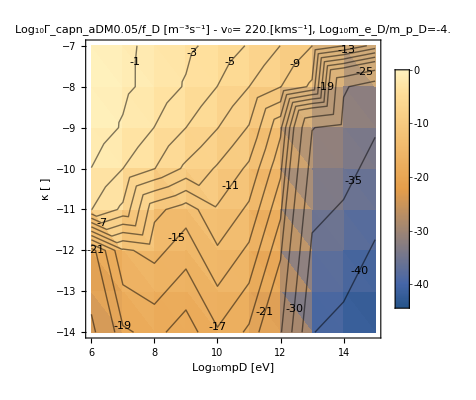

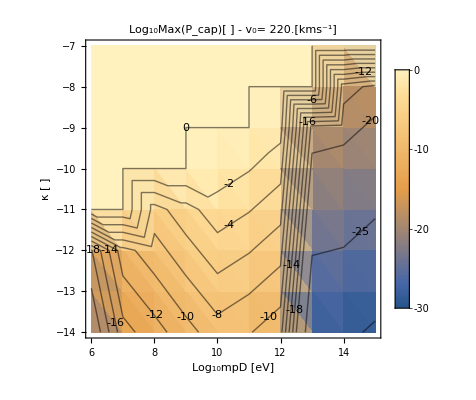

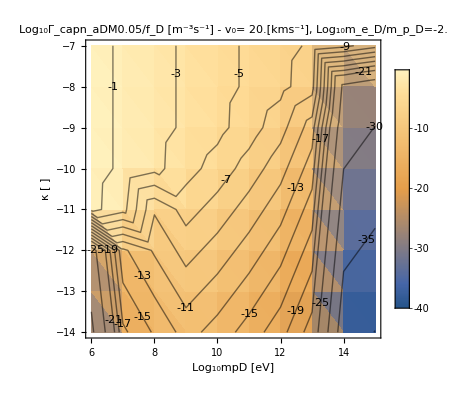

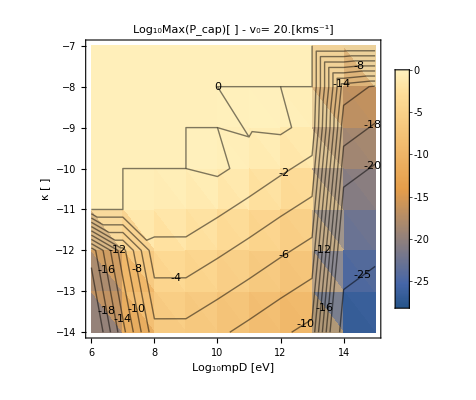

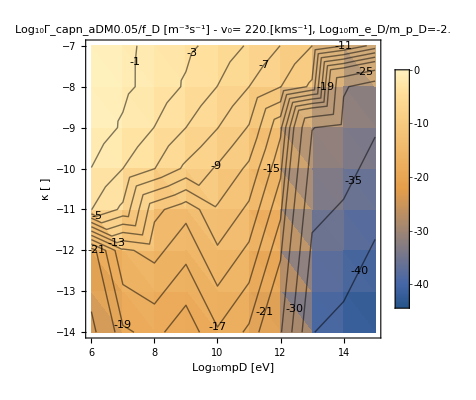

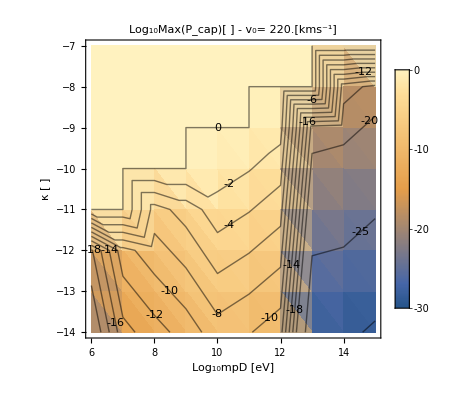

```mathematica
PlotCaptureRateκContour[KEDictListnoFF]
```

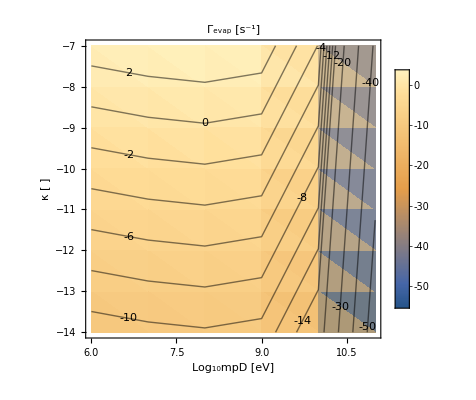

-Graphics-

-Graphics-

-Graphics-

```mathematica
PlotEvaporationRateκContour[KEDictListnoFF]
```

#### compute directly from nuclear interpolations and compare

```mathematica
Table[Nucind = FirstPosition["mχ"/.NuclearσDicstnoFF,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];"ΓTotal"/.IterateGetEvaporationRate[NuclearσDicstnoFF[[Nucind]]],{m,6,15}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 10 recursive bisections in vχ near {vχ,vT} = {11199.999957239255112858796782637771372037605033256113529205322266,1671.1}. NIntegrate obtained 8.59634×10^12 and 3.44881×10^11 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 10 recursive bisections in vχ near {vχ,vT} = {11199.999914486696489256803747035229346096230074181221425533294678,1671.1}. NIntegrate obtained 4.70414×10^12 and 2.13669×10^11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 10 recursive bisections in vχ near {vχ,vT} = {11199.999900237662382339895537214369269918279314879328012466430664,1671.1}. NIntegrate obtained 5.24198×10^12 and 3.13597×10^11 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{9.66189×10^16,3.12976×10^17,6.13862×10^17,2.13919×10^17,8.28114×10^11,3.32111×10^-28,0.,0.,0.,0.}

```mathematica
Table[Nucind = FirstPosition["mχ"/.NuclearσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];"ΓTotal"/.IterateGetEvaporationRate[NuclearσDicts[[Nucind]]],{m,6,15}]
```

{1.49315×10^8,4.65651×10^12,1.53176×10^16,6.12288×10^16,1.21423×10^12,7.01966×10^-28,0.,0.,0.,0.}

### Normalize truncated velocity distribution for Evap rate to 1

#### Analytic Expression

When we include this in the Evaporation rate, we will need to factor out the normalization for the MB distribution on the full range and replace it with the below for the restricted / truncated velocity range

```mathematica
fMBnorm = Assuming[βE mχ/2 vχ^2>0,Integrate[vχ^2 E^(-βE mχ/2 vχ^2),{vχ,0,∞}]]
```

(√(π/2))/(mχ βE)^(3/2)

```mathematica
Assuming[βE mχ/2 vχ^2>0,Integrate[vχ^2 E^(-βE mχ/2 vχ^2),vχ]]
truncedfMBnorm=(%/.vχ->vesc)-(%/.vχ->0)//Simplify
```

-(ⅇ^(-1/2 mχ vχ^2 βE) vχ)/(mχ βE)+(√(π/2) Erf[(√mχ vχ √βE)/(√2)])/(mχ^(3/2) βE^(3/2))

-(ⅇ^(-1/2 mχ vesc^2 βE) vesc)/(mχ βE)+(√(π/2) Erf[(√mχ vesc √βE)/(√2)])/(mχ^(3/2) βE^(3/2))

```mathematica
Clear[x]
EvapRescale =fMBnorm/truncedfMBnorm//FullSimplify//PowerExpand//FullSimplify
("N_(MB, truncated)")/("N_MB")==%/.vesc->x/(√(mχ βE))//FullSimplify//PowerExpand//FullSimplify
x== Subscript[v, esc] √(Subscript[m, χ] Subscript[β, E])
```

1/(-ⅇ^(-1/2 mχ vesc^2 βE) √mχ √(2/π) vesc √βE+Erf[(√mχ vesc √βE)/(√2)])

(N_(MB, truncated))/N_MB==1/(-ⅇ^(-x^2/2) √(2/π) x+Erf[x/(√2)])

x==v_esc √(m_χ β_ⅇ)

1/(-0.0000433788 ⅇ^(-1.4779×10^-9 mχ) √mχ+Erf[0.0000384435 √mχ])

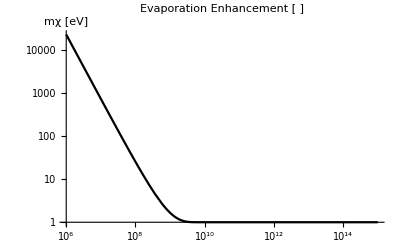

```mathematica
EvapRescale/.vesc->"vesc"/.βE->"βcore"/.EarthRepl/.mχ->mχ("JpereV")/("c")^2/.SIConstRepl//Simplify//PowerExpand
LogLogPlot[%,{mχ,10^6,10^15},PlotLabel->"Evaporation Enhancement [ ]",AxesLabel->"mχ [eV]",PlotStyle->Black]
```

#### Plots

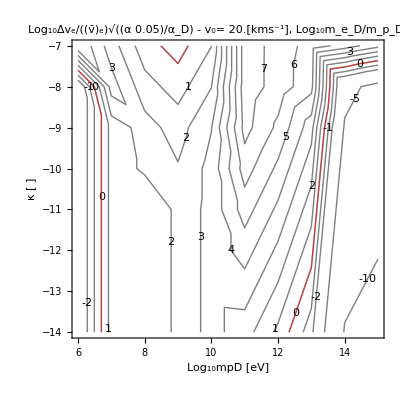

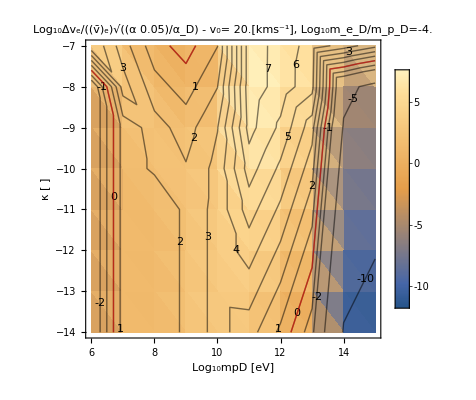

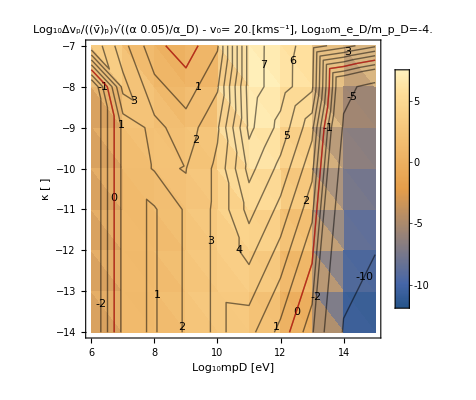

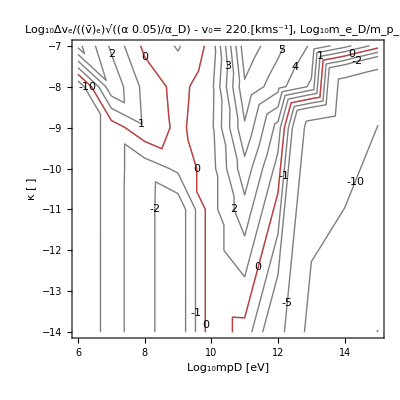

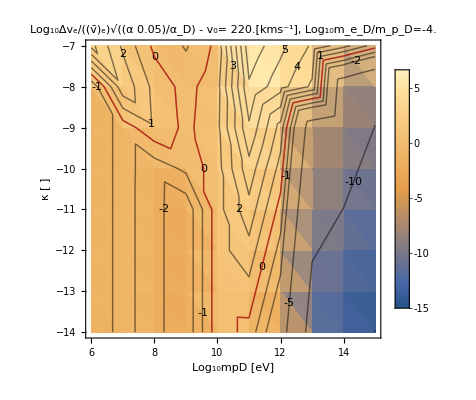

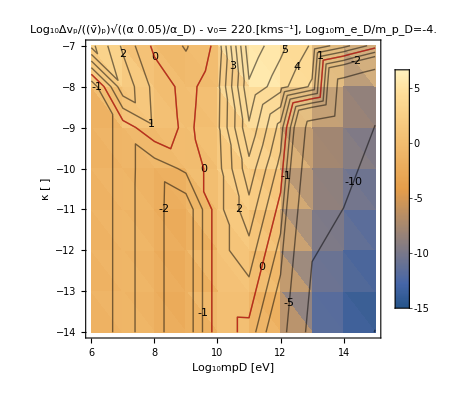

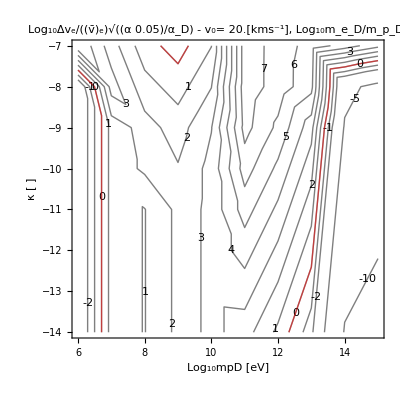

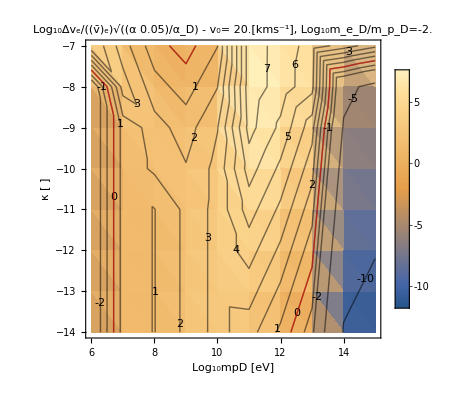

```mathematica
PlotKEchangeκContour[KEDictList]
```

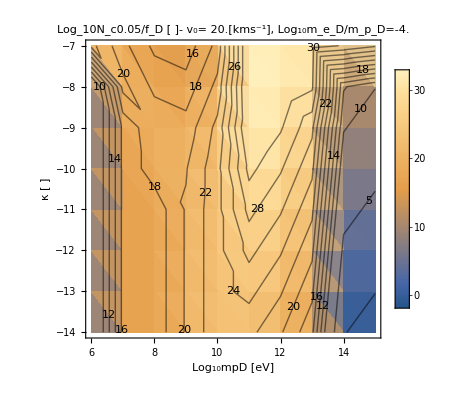

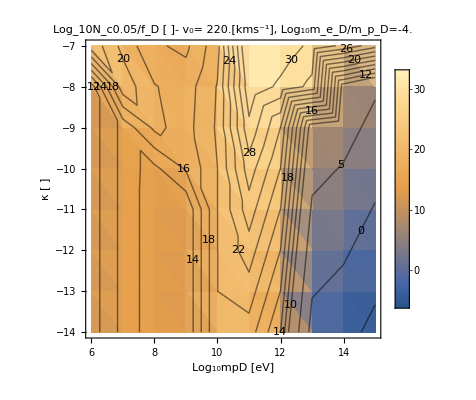

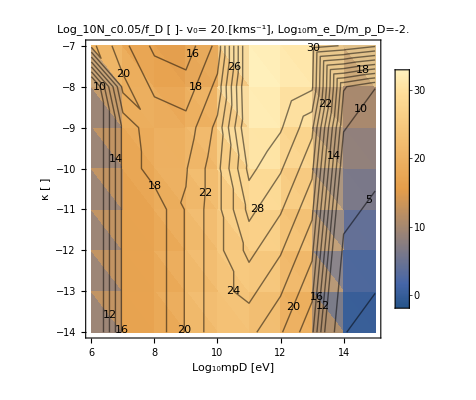

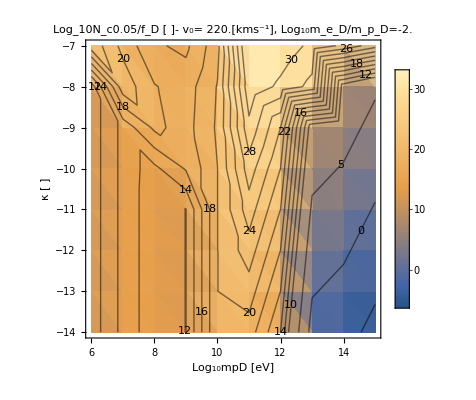

```mathematica
PlotNcκContour[KEDictList]
```

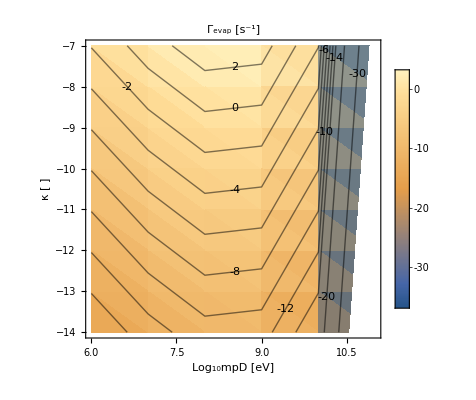

-Graphics-

-Graphics-

-Graphics-

```mathematica
PlotEvaporationRateκContour[KEDictList]
```

### Investigate Electronic domination above a TeV

#### KE of heavy mpD

for disk case and 10 TeV, the KE and capture energy is

```mathematica
1/2 10^13 (10^-4)^2 eV/c^2 c^2
%-1/2 10^13 (("vesc")/("c"))^2 eV/c^2 c^2/.Constants`EarthRepl/.SIConstRepl//N
```

50000 eV

43031.1 eV

#### Increase velocity range and look at nuclear capture at high masses

```mathematica
Block[{eind,Nucind,PDictScan,m=15},
eind = FirstPosition["mχ"/.ElectronicσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
Nucind = FirstPosition["mχ"/.NuclearσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
PDictScan=ScanGetCaptureRateandGetNc[meDPoints,κpoints,v0Points,ElectronicσDicts[[eind]],NuclearσDicts[[Nucind]]];
SaveIt[NotebookDirectory[]<>filenames[[m-5]]<>"_larger_vχ_range",PDictScan];
]
```

mpD: 1.×10^15

meD/mpD: 1/10000

v0: 20000

βD: 8.42612×10^12

κ is: 1.×10^-14

General::munfl: Exp[-3.96069×10^109] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3.89398×10^109] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3.68662×10^109] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

meD/mpD: 1/10000

v0: 220000

βD: 6.96374×10^10

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

meD/mpD: 1/100

v0: 20000

βD: 8.34353×10^12

κ is: 1.×10^-14

$Aborted

```mathematica
Log10@"vesc"/.EarthRepl//N
```

4.04922

#### What is it that lets the electrons go so far off shell

```mathematica
Solve[u-z==a/.{u->ω/(k vF),z->(ℏ k)/(2 m vF)},ω]//Simplify
%[[1]]/.a->1
%%[[1]]/.a->-1
```

{{ω→a k vF+(k^2 ℏ)/(2 m)}}

{ω→k vF+(k^2 ℏ)/(2 m)}

{ω→-k vF+(k^2 ℏ)/(2 m)}

The on shell region is defined by on shell for electrons moving at v_e=vF

```mathematica
ω==-(1/ℏ(1/2 m vF^2-(1m)/2(vF-(ℏ k)/m)^2)//Simplify//Expand//Simplify)
```

ω==-k vF+(k^2 ℏ)/(2 m)

### Quick check on Nuclear SF dispersion relation

We assumed nuclei are initially at rest when considering nuclear interactions. Under what conditions can we neglect the velocity of nuclei compared to incoming adm?

Ie. what is thermal velocity of nuclei in the Earth?

```mathematica
("βcore"/.EarthRepl)^-1(*Subscript[T, Core]*)
10^10("JpereV")/("c")^2/.Constants`SIConstRepl(*Nuclear masses*)
"The rough thermal velocity of nuclei in the core is:"
√((%%%)/(%%))
"The ratio of this to the escape velocity is:"
(%%)/("vesc")/.EarthRepl
"So even for the disk case we can roughly do this. "
```

7.55407×10^-20

1.78×10^-26

2060.06

0.183934

### q_max(m_pD) understanding the peak at 10^8 eV

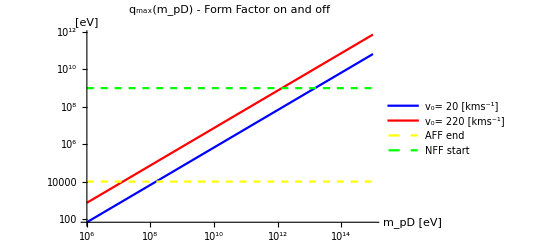

```mathematica
plotstyle={Blue,Red,Directive[Dashed,Yellow],Directive[Dashed,Green]};
LogLogPlot[Evaluate[Join[mpD v0Points/("c")/.SIConstRepl,{10^4,10^9}]],{mpD,10^6,10^15},PlotStyle->plotstyle,PlotLegends->LineLegend[plotstyle,Join[Table["v_0= "<>ToString[v0Points[[v]]/1000]<>" [kms^-1]",{v,2}],{"AFF end","NFF start"}]],PlotLabel->"q_max(m_pD) - Form Factor on and off",AxesLabel->{"m_pD [eV]","[eV]"}]
```

### Plot Dielectric

```mathematica
stucinterp = Table[Print[i];InterpolateStruc[{FeTotalparams[[i]]}],{i,Length[FeTotalparams]}]
```

1

2

3

4

5

6

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

```mathematica
Re[stucinterp[[2]][10,15]]
```

-33.7825

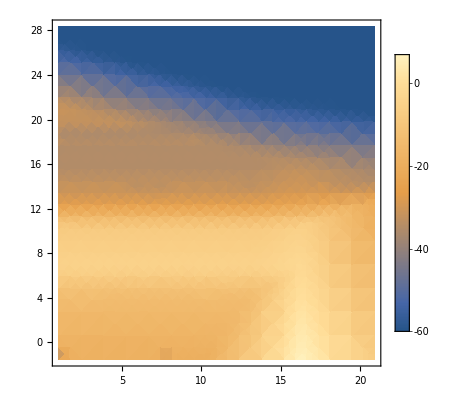

```mathematica
Block[{Strucflist = stucinterp,o=3,strucf,params=FeTotalparams,dom},

strucf = Strucflist[[o]];
dom = strucf["Domain"];

Print@DensityPlot[Re[strucf[k,ω]](*HeavisideTheta[10^ω-"ωedgei"/.FeTotalparams[[o]]]*),{k,dom[[1,1]],dom[[1,2]]},{ω,dom[[2,1]],dom[[2,2]]},PlotLegends->Automatic,PlotRange->All]
]
```

```mathematica
2 10^16("ℏ")/("JpereV")/.SIConstRepl
```

13.171

```mathematica
"β""ℏ""ωedgei"/.FeTotalparams
```

{15.9247,0.173564,7.98125,4.0001,28724.7,289487.}

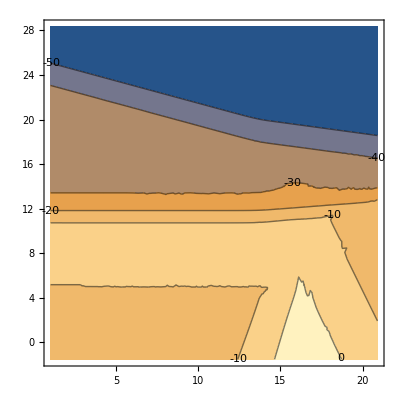

```mathematica
Block[{Strucflist = stucinterp,strucf,params=FeTotalparams,dom},

strucf = Strucflist[[1]];
dom = strucf["Domain"];

(*Print@DensityPlot[Log10@Sum[10^Re[Strucflist[[o]][k,ω]]HeavisideTheta[10^ω-"ωedgei"/.FeTotalparams[[o]]],{o,Length[Strucflist]}],{k,dom[[1,1]],dom[[1,2]]},{ω,dom[[2,1]],dom[[2,2]]},PlotLegends->Automatic,PlotRange->All]*)
Print@ContourPlot[Log10@Sum[10^Re[Strucflist[[o]][k,ω]](*HeavisideTheta[10^ω-"ωedgei"/.FeTotalparams[[o]]]*),{o,Length[Strucflist]}],{k,dom[[1,1]],dom[[1,2]]},{ω,dom[[2,1]],dom[[2,2]]},ContourLabels->True,PlotRange->All]
]
```

### Compute Electronic evaporation rate

#### Interpolate cross-section

```mathematica
(*FeσDictend=Monitor[Table[Table[InterpolatevχandωσdEReξnd[10^m ("JpereV")/("c")^2/.Constants`SIConstRepl,FeTotalparams[[i]],10,60,10^-6,4,True,True,2,ToString[StringForm["Fe ``",i]],False],{i,Length[FeTotalparams]}],{m,6,15}],m];*)
(*FeσDictend=Monitor[Table[Table[InterpolatevχandωσdEReξnd[10^m ("JpereV")/("c")^2/.Constants`SIConstRepl,FeTotalparams[[i]],10,60,10^-8,4,True,True,2,ToString[StringForm["Fe ``",i]],False],{i,Length[FeTotalparams]}],{m,6,15}
(*{m,6,6}*)],m];
SaveIt[NotebookDirectory[]<>"FeσDictend",FeσDictend]*)
FeσDictend=Monitor[Table[{InterpolatevχandωσdEReξnd[10^m ("JpereV")/("c")^2/.Constants`SIConstRepl,FeTotalparams[[2]],10,60,10^-8,4,True,True,2,ToString[StringForm["Fe ``",2]],False]},{m,6,15}
(*{m,6,6}*)],m];
SaveIt[NotebookDirectory[]<>"FeσDictend",FeσDictend]
```

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\FeσDictend.dat

```mathematica
SiO2σDictend=Table[Table[InterpolatevχandωσdEReξnd[10^m ("JpereV")/("c")^2/.Constants`SIConstRepl,SiO2Totalparams[[i]],10,60,10^-6,4,True,True,1,ToString[StringForm["SiO2 ``",i]],False],{i,Length[SiO2Totalparams]}],{m,6,15}];
SaveIt[NotebookDirectory[]<>"SiO2σDictend",SiO2σDictend]
```

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\SiO2σDictend.dat

```mathematica
MgOσDictend=Table[Table[InterpolatevχandωσdEReξnd[10^m ("JpereV")/("c")^2/.Constants`SIConstRepl,MgOTotalparams[[i]],10,60,10^-6,4,True,True,1,ToString[StringForm["MgO ``",i]],False],{i,Length[MgOTotalparams]}],{m,6,15}];
SaveIt[NotebookDirectory[]<>"MgOσDictend",MgOσDictend]
```

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\MgOσDictend.dat

```mathematica
FeσDictend[[2,1]]["σf"]["Methods"]
FeσDictend[[2,1]]["σf"]["Grid"]
FeσDictend[[2,1]]["σf"]["ValuesOnGrid"]
```

{Coordinates,DerivativeOrder,Domain,ElementMesh,Evaluate,GetPolynomial,Grid,IndexedElementEvaluate,InterpolationMethod,InterpolationOrder,MethodInformation,Methods,OutputDimensions,ParameterAddress,Periodicity,PlottableQ,Properties,QuantityUnits,Unpack,ValuesOnGrid,VectorEvaluate}

{{6.8263},{6.92149},{7.01667},{7.11186},{7.20704},{7.30223},{7.39741},{7.4926},{7.58778},{7.68297},{7.77815}}

{-118.247,-23.5574,-22.9774,-22.6573,-22.4441,-22.2917,-22.1811,-22.1042,-22.0581,-22.0434,-22.0624}

```mathematica
FeσDictend[[1,1]]["σfofξ"]["ValuesOnGrid"]
```

Missing[KeyAbsent,σfofξ][ValuesOnGrid]

#### Plot Interpolated x-secs

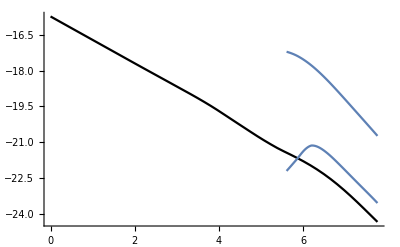

```mathematica
Show[{Plot[FeσDictend[[1,2]]["σf"][ω],{ω,0,7.77},PlotRange->All,PlotStyle->Black],Plot[FeσDictNuc[[1]]["σf"][ω],{ω,5.61,7.77},PlotRange->All],
Plot[FeσDicte[[1,2]]["σf"][ω],{ω,5.61,7.77},PlotRange->All]}]
```

```mathematica
FeσDictend[[1,2]]["σf"]
```

InterpolatingFunction[…]

```mathematica
Plot[FeσDictend[[1,1]]["dσf"][ω],{ω,3.77,7.77},PlotRange->All]
```

-Graphics-

```mathematica
FeσDictend[[1,1]]["dσf"]
```

InterpolatingFunction[…]

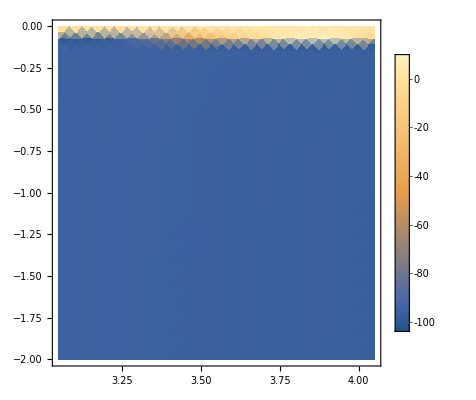

```mathematica
DensityPlot[FeσDictend[[1,1]]["dσf"][vχ,ξ],{vχ,3.05,4.05},{ξ,-2,-0.00437},PlotRange->All,PlotLegends->Automatic]
```

```mathematica
(*FeσDictend[[1,1]]["dσf"]["Grid"]*)
(*FeσDictend[[1,1]]["dσf"]["ValuesOnGrid"]*)

FeσDictend[[1,2]]["σofξf"]["ValuesOnGrid"]
```

{{-15.7172,-15.7172,-15.7172,-15.7172,-15.7172,-15.7172,-15.7172,-15.7172,-15.7172,-15.7172,-15.7172,-15.7172,-15.7172,-15.7172,-15.7172,-15.7172,-15.7172,-15.7173,-15.7173,-15.7173,-15.7173,-15.7173,-15.7173,-15.7173,-15.7174,-15.7174,-15.7174,-15.7175,-15.7176,-15.7177,-15.7178,-15.7179,-15.7181,-15.7183,-15.7186,-15.7189,-15.7194,-15.72,-15.7207,-15.7215,-15.7227,-15.7241,-15.7258,-15.7281,-15.7309,-15.7344,-15.7388,-15.7439,-15.7513,-15.7601,-15.7712,-15.7854,-15.8034,-15.8266,-15.8579,-15.8994,-15.9584,-16.0456,-16.1881,-17.3641,-100.},{-16.1164,-16.1164,-16.1164,-16.1164,-16.1164,-16.1164,-16.1164,-16.1164,-16.1164,-16.1164,-16.1164,-16.1164,-16.1164,-16.1164,-16.1164,-16.1164,-16.1164,-16.1164,-16.1164,-16.1165,-16.1165,-16.1165,-16.1165,-16.1165,-16.1165,-16.1166,-16.1166,-16.1167,-16.1167,-16.1168,-16.1169,-16.1171,-16.1173,-16.1175,-16.1178,-16.1181,-16.1186,-16.1191,-16.1198,-16.1207,-16.1218,-16.1232,-16.1249,-16.1271,-16.1299,-16.1333,-16.1377,-16.1427,-16.15,-16.1587,-16.1697,-16.1836,-16.2014,-16.2242,-16.2549,-16.2957,-16.3533,-16.4384,-16.5763,-17.7888,-100.},{-16.5153,-16.5153,-16.5153,-16.5153,-16.5153,-16.5153,-16.5153,-16.5153,-16.5153,-16.5153,-16.5153,-16.5153,-16.5153,-16.5153,-16.5153,-16.5153,-16.5153,-16.5153,-16.5153,-16.5154,-16.5154,-16.5154,-16.5154,-16.5154,-16.5154,-16.5155,-16.5155,-16.5156,-16.5156,-16.5157,-16.5158,-16.516,-16.5161,-16.5164,-16.5166,-16.517,-16.5174,-16.518,-16.5186,-16.5195,-16.5206,-16.522,-16.5237,-16.5258,-16.5286,-16.532,-16.5363,-16.5412,-16.5485,-16.557,-16.5678,-16.5815,-16.599,-16.6214,-16.6516,-16.6915,-16.748,-16.8308,-16.9641,-18.2126,-100.},{-16.9139,-16.9139,-16.9139,-16.9139,-16.9139,-16.9139,-16.9139,-16.9139,-16.9139,-16.9139,-16.9139,-16.9139,-16.9139,-16.9139,-16.9139,-16.9139,-16.9139,-16.9139,-16.9139,-16.9139,-16.9139,-16.914,-16.914,-16.914,-16.914,-16.914,-16.9141,-16.9141,-16.9142,-16.9143,-16.9144,-16.9145,-16.9147,-16.9149,-16.9152,-16.9155,-16.916,-16.9165,-16.9172,-16.918,-16.9191,-16.9204,-16.9221,-16.9243,-16.927,-16.9303,-16.9345,-16.9394,-16.9465,-16.9549,-16.9656,-16.979,-16.9962,-17.0182,-17.0479,-17.087,-17.1422,-17.2229,-17.3516,-18.6355,-100.},{-17.3121,-17.3121,-17.3121,-17.3121,-17.3121,-17.3121,-17.3121,-17.3121,-17.3121,-17.3121,-17.3121,-17.3121,-17.3121,-17.3121,-17.3121,-17.3121,-17.3121,-17.3121,-17.3121,-17.3121,-17.3121,-17.3121,-17.3122,-17.3122,-17.3122,-17.3122,-17.3123,-17.3123,-17.3124,-17.3125,-17.3126,-17.3127,-17.3129,-17.3131,-17.3134,-17.3137,-17.3141,-17.3146,-17.3153,-17.3161,-17.3172,-17.3185,-17.3202,-17.3223,-17.325,-17.3283,-17.3324,-17.3372,-17.3442,-17.3525,-17.3629,-17.3762,-17.3931,-17.4147,-17.4438,-17.482,-17.5359,-17.6145,-17.7388,-19.0577,-100.},{-17.7097,-17.7097,-17.7097,-17.7097,-17.7097,-17.7097,-17.7097,-17.7097,-17.7097,-17.7097,-17.7097,-17.7097,-17.7097,-17.7097,-17.7097,-17.7097,-17.7097,-17.7097,-17.7097,-17.7097,-17.7097,-17.7098,-17.7098,-17.7098,-17.7098,-17.7099,-17.7099,-17.7099,-17.71,-17.7101,-17.7102,-17.7103,-17.7105,-17.7107,-17.711,-17.7113,-17.7117,-17.7122,-17.7129,-17.7137,-17.7148,-17.7161,-17.7177,-17.7198,-17.7224,-17.7256,-17.7297,-17.7344,-17.7414,-17.7495,-17.7597,-17.7728,-17.7894,-17.8106,-17.8391,-17.8765,-17.9292,-18.0056,-18.1257,-19.4793,-100.},{-18.1064,-18.1064,-18.1064,-18.1064,-18.1064,-18.1064,-18.1064,-18.1064,-18.1064,-18.1064,-18.1064,-18.1064,-18.1064,-18.1064,-18.1064,-18.1064,-18.1064,-18.1064,-18.1064,-18.1064,-18.1064,-18.1064,-18.1064,-18.1065,-18.1065,-18.1065,-18.1065,-18.1066,-18.1067,-18.1067,-18.1068,-18.107,-18.1071,-18.1073,-18.1076,-18.1079,-18.1083,-18.1089,-18.1095,-18.1103,-18.1113,-18.1126,-18.1142,-18.1163,-18.1189,-18.122,-18.1261,-18.1306,-18.1375,-18.1455,-18.1556,-18.1684,-18.1847,-18.2055,-18.2335,-18.2702,-18.3217,-18.3961,-18.5123,-19.9007,-100.},{-18.5012,-18.5012,-18.5012,-18.5012,-18.5012,-18.5012,-18.5012,-18.5012,-18.5012,-18.5012,-18.5012,-18.5012,-18.5012,-18.5012,-18.5012,-18.5012,-18.5012,-18.5012,-18.5012,-18.5012,-18.5012,-18.5013,-18.5013,-18.5013,-18.5013,-18.5014,-18.5014,-18.5014,-18.5015,-18.5016,-18.5017,-18.5018,-18.502,-18.5022,-18.5024,-18.5028,-18.5032,-18.5037,-18.5043,-18.5051,-18.5061,-18.5074,-18.509,-18.511,-18.5136,-18.5167,-18.5207,-18.5257,-18.532,-18.5398,-18.5498,-18.5624,-18.5785,-18.599,-18.6265,-18.6625,-18.7131,-18.7858,-18.8989,-20.3232,-100.},{-18.8935,-18.8935,-18.8935,-18.8935,-18.8935,-18.8935,-18.8935,-18.8935,-18.8935,-18.8935,-18.8935,-18.8935,-18.8935,-18.8935,-18.8935,-18.8935,-18.8935,-18.8935,-18.8935,-18.8936,-18.8936,-18.8936,-18.8936,-18.8936,-18.8936,-18.8937,-18.8937,-18.8938,-18.8938,-18.8939,-18.894,-18.8941,-18.8943,-18.8945,-18.8947,-18.8951,-18.8955,-18.896,-18.8966,-18.8974,-18.8984,-18.8997,-18.9013,-18.9033,-18.9058,-18.909,-18.913,-18.9179,-18.9242,-18.9321,-18.942,-18.9546,-18.9706,-18.9909,-19.0184,-19.0543,-19.1047,-19.1773,-19.2897,-20.7553,-100.},{-19.3,-19.3,-19.3,-19.3,-19.3,-19.3,-19.3,-19.3,-19.3,-19.3,-19.3,-19.3,-19.3,-19.3,-19.3,-19.3,-19.3001,-19.3001,-19.3001,-19.3001,-19.3001,-19.3001,-19.3001,-19.3001,-19.3002,-19.3002,-19.3002,-19.3003,-19.3004,-19.3004,-19.3005,-19.3007,-19.3009,-19.3011,-19.3013,-19.3017,-19.3021,-19.3027,-19.3034,-19.3042,-19.3053,-19.3067,-19.3084,-19.3105,-19.3133,-19.3166,-19.3209,-19.3262,-19.333,-19.3414,-19.3521,-19.3656,-19.383,-19.4051,-19.435,-19.4747,-19.531,-19.6134,-19.7443,-21.2986,-100.},{-19.7411,-19.7411,-19.7411,-19.7411,-19.7411,-19.7411,-19.7411,-19.7411,-19.7411,-19.7411,-19.7411,-19.7411,-19.7411,-19.7411,-19.7411,-19.7411,-19.7411,-19.7411,-19.7411,-19.7412,-19.7412,-19.7412,-19.7412,-19.7412,-19.7413,-19.7413,-19.7414,-19.7414,-19.7415,-19.7416,-19.7418,-19.7419,-19.7422,-19.7424,-19.7428,-19.7432,-19.7437,-19.7444,-19.7453,-19.7464,-19.7478,-19.7495,-19.7516,-19.7543,-19.7578,-19.7621,-19.7675,-19.7738,-19.7829,-19.7937,-19.8075,-19.8252,-19.8481,-19.878,-19.919,-19.9757,-20.0593,-20.187,-20.3684,-21.9962,-100.}}

```mathematica
FeσDictend[[1,2]]["σofξf"]
FeσDictend[[2,2]]["σofξf"]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

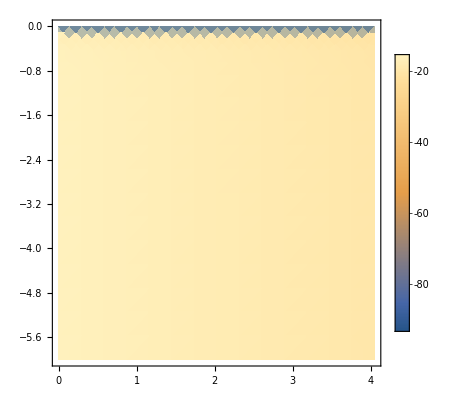

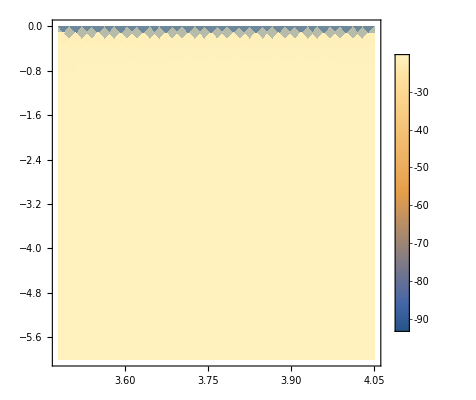

```mathematica
DensityPlot[FeσDictend[[1,2]]["σofξf"][vχ,ξ],{vχ,0,4.05},{ξ,-6,-0.00437},PlotRange->All,PlotLegends->Automatic]
DensityPlot[FeσDictend[[2,2]]["σofξf"][vχ,ξ],{vχ,3.48,4.05},{ξ,-6,-0.00437},PlotRange->All,PlotLegends->Automatic]
```

```mathematica
FeσDictend[[1,2]]["σofξf"]
FeσDictend[[2,2]]["σofξf"]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

InterpolatingFunction::dmval: Input value {3.47004,-5.99957} lies outside the range of data in the interpolating function. Extrapolation will be used.

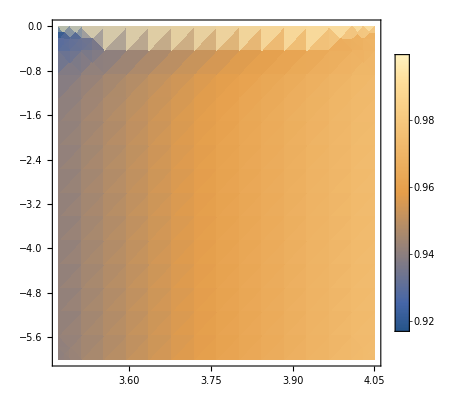

```mathematica
DensityPlot[(FeσDictend[[1,2]]["σofξf"][vχ,ξ])/(FeσDictend[[2,2]]["σofξf"][vχ,ξ]),{vχ,3.47,4.05},{ξ,-6,-0.00437},PlotRange->All,PlotLegends->Automatic]
```

```mathematica
FeσDicte[[1,1]]["σofξf"]
```

InterpolatingFunction[…]

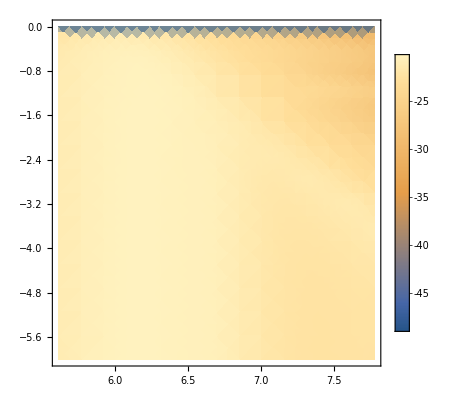

```mathematica
DensityPlot[FeσDicte[[1,1]]["σofξf"][vχ,ξ],{vχ,5.61,7.78},{ξ,-6,-10^-6},PlotRange->All,PlotLegends->Automatic]
```

#### Get Evaporation Rate for Electronic

```mathematica
"vF"/.FeTotalparams[[2]]
```

2.06517×10^6

```mathematica
"1 MeV is 0 because ξ(ω_capture) is negative (so < ξmin). 
These shouldn't be 0 for ω_capture < ωmin, there are still ω > ω_capturefor which you can still have evaporation. "
```

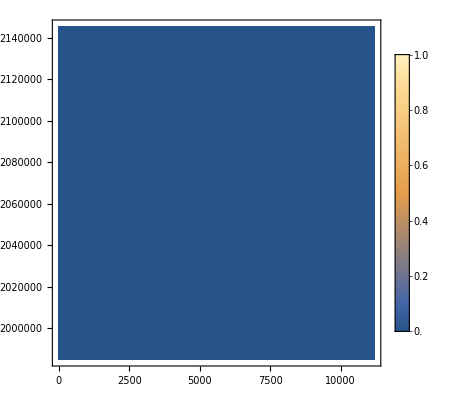

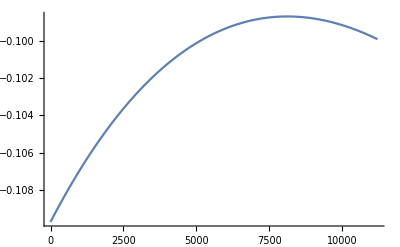

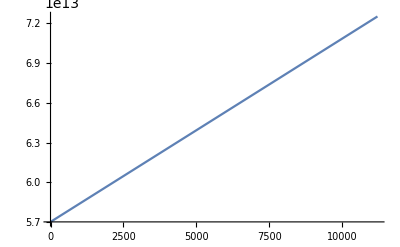

6.5887×10^12

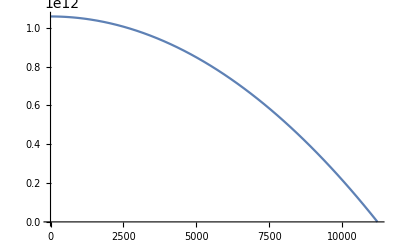

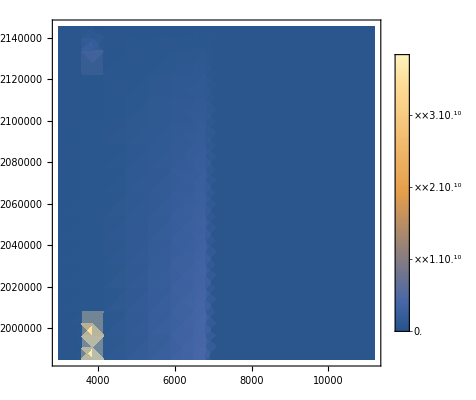

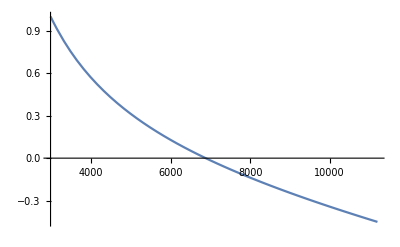

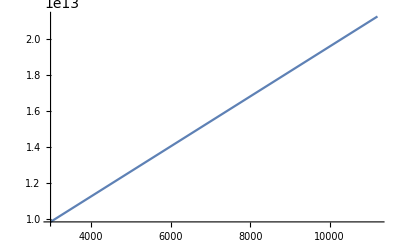

6.5887×10^12

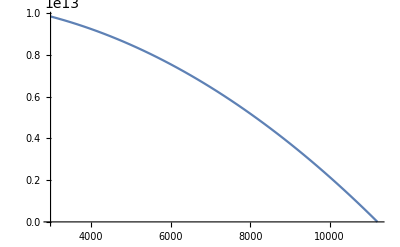

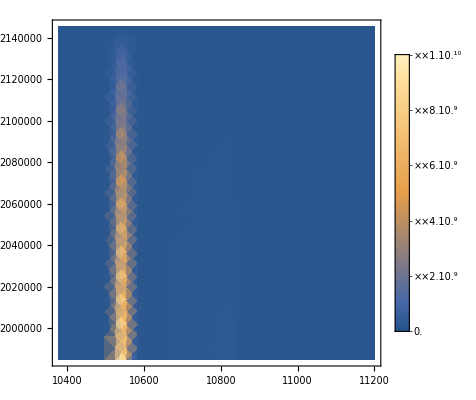

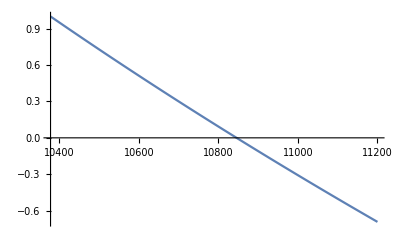

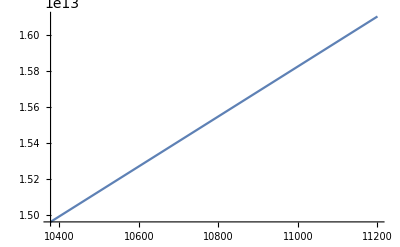

6.5887×10^12

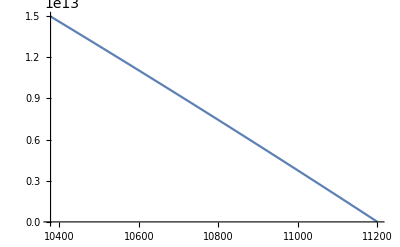

-Graphics-

-Graphics-

-Graphics-

6.5887×10^12

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

6.5887×10^12

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

6.5887×10^12

-Graphics-

General::munfl: Exp[-1477.88] is too small to represent as a normalized machine number; precision may be lost.

-Graphics-

-Graphics-

-Graphics-

6.5887×10^12

-Graphics-

General::munfl: Exp[-14779.] is too small to represent as a normalized machine number; precision may be lost.

-Graphics-

-Graphics-

-Graphics-

6.5887×10^12

-Graphics-

General::munfl: Exp[-147790.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics-

-Graphics-

-Graphics-

6.5887×10^12

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

6.5887×10^12

-Graphics-

{<|ΓTotal→0.,Γs→{0.}|>,<|ΓTotal→1.8818×10^14,Γs→{1.8818×10^14}|>,<|ΓTotal→1.17574×10^14,Γs→{1.17574×10^14}|>,<|ΓTotal→7.16692×10^12,Γs→{7.16692×10^12}|>,<|ΓTotal→2.30498×10^7,Γs→{2.30498×10^7}|>,<|ΓTotal→6.98236×10^-51,Γs→{6.98236×10^-51}|>,<|ΓTotal→0.,Γs→{0.}|>,<|ΓTotal→0.,Γs→{0.}|>,<|ΓTotal→0.,Γs→{0.}|>,<|ΓTotal→0.,Γs→{0.}|>}

```mathematica
(*eEvaprates = Table[IterateGetEvaporationRateend[FeσDictend[[m,2;;2]]],{m,Length[FeσDictend]}]*)
eEvaprates = Table[IterateGetEvaporationRateend[FeσDictend[[m]]],{m,Length[FeσDictend]}]
```

```mathematica
"ΓTotal"/.eEvaprates
```

{0.,8.40302×10^13,5.27225×10^13,3.25766×10^12,1.04904×10^7,8.82924×10^-52,0.,0.,0.,0.}

```mathematica
"Γtotal"/.PDictScans[[;;,1]]
```

{1.56385×10^12,1.6157×10^15,1.97661×10^17,8.53235×10^16,1.45923×10^12,1.5795×10^-25,0.,0.,0.,0.}

### Compute Electronic evaporation rate - reducing ωedge for the conduction band

#### Interpolate cross-section

```mathematica
RescaleParams[FeTotalparams[[2]],10^-3,"ωedgei"]
```

{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,eVm→2.×10^-7,β→1.32379×10^19,ne→1.91532×10^29,qF→1.78329×10^10,vF→2.06517×10^6,μ→1.94267×10^-18,ωp→2.47055×10^16,α→1/137,χ→0.580962,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→25.7168,nI→2.39415×10^28,Z→8,M→9.27329×10^-26,EF→1.94267×10^-18,ωi→2.47055×10^16,νi→8.99966×10^15,Ai→0.0699144,ωedgei→6.5887×10^9}

```mathematica
?Utilities`RescaleParams
```

```mathematica
FeTotalparams[[2]]
```

{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,eVm→2.×10^-7,β→1.32379×10^19,ne→1.91532×10^29,qF→1.78329×10^10,vF→2.06517×10^6,μ→1.94267×10^-18,ωp→2.47055×10^16,α→1/137,χ→0.580962,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→25.7168,nI→2.39415×10^28,Z→8,M→9.27329×10^-26,EF→1.94267×10^-18,ωi→2.47055×10^16,νi→8.99966×10^15,Ai→0.0699144,ωedgei→6.5887×10^12}

```mathematica
(*FeσDictend=Monitor[Table[Table[InterpolatevχandωσdEReξnd[10^m ("JpereV")/("c")^2/.Constants`SIConstRepl,FeTotalparams[[i]],10,60,10^-6,4,True,True,2,ToString[StringForm["Fe ``",i]],False],{i,Length[FeTotalparams]}],{m,6,15}],m];*)
(*FeσDictend=Monitor[Table[Table[InterpolatevχandωσdEReξnd[10^m ("JpereV")/("c")^2/.Constants`SIConstRepl,FeTotalparams[[i]],10,60,10^-8,4,True,True,2,ToString[StringForm["Fe ``",i]],False],{i,Length[FeTotalparams]}],{m,6,15}
(*{m,6,6}*)],m];
SaveIt[NotebookDirectory[]<>"FeσDictend",FeσDictend]*)
(*FeσDictend=Monitor[Table[{InterpolatevχandωσdEReξnd[10^m ("JpereV")/("c")^2/.Constants`SIConstRepl,FeTotalparams[[2]],10,60,10^-8,4,True,True,2,ToString[StringForm["Fe ``",2]],False]},{m,6,15}
(*{m,6,6}*)],m];
SaveIt[NotebookDirectory[]<>"FeσDictend",FeσDictend]*)
```

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\FeσDictend.dat

```mathematica
"With conduction band only, and ωedgei rescaled by a factor of 10^-3"
FeσDictend=Monitor[Table[{InterpolatevχandωσdEReξnd[10^m ("JpereV")/("c")^2/.Constants`SIConstRepl,RescaleParams[FeTotalparams[[2]],10^-3,"ωedgei"],20,60,10^-8,4,True,True,2,ToString[StringForm["Fe ``",2]],False]},{m,6,15}
(*{m,6,6}*)],m];
SaveIt[NotebookDirectory[]<>"FeσDictend",FeσDictend]
```

With conduction band only, and ωedgei rescaled by a factor of 10^-3

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\FeσDictend.dat

```mathematica
SiO2σDictend=Table[Table[InterpolatevχandωσdEReξnd[10^m ("JpereV")/("c")^2/.Constants`SIConstRepl,SiO2Totalparams[[i]],10,60,10^-6,4,True,True,1,ToString[StringForm["SiO2 ``",i]],False],{i,Length[SiO2Totalparams]}],{m,6,15}];
SaveIt[NotebookDirectory[]<>"SiO2σDictend",SiO2σDictend]
```

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\SiO2σDictend.dat

```mathematica
MgOσDictend=Table[Table[InterpolatevχandωσdEReξnd[10^m ("JpereV")/("c")^2/.Constants`SIConstRepl,MgOTotalparams[[i]],10,60,10^-6,4,True,True,1,ToString[StringForm["MgO ``",i]],False],{i,Length[MgOTotalparams]}],{m,6,15}];
SaveIt[NotebookDirectory[]<>"MgOσDictend",MgOσDictend]
```

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\MgOσDictend.dat

```mathematica
FeσDictend[[2,1]]["σf"]["Methods"]
FeσDictend[[2,1]]["σf"]["Grid"]
FeσDictend[[2,1]]["σf"]["ValuesOnGrid"]
```

{Coordinates,DerivativeOrder,Domain,ElementMesh,Evaluate,GetPolynomial,Grid,IndexedElementEvaluate,InterpolationMethod,InterpolationOrder,MethodInformation,Methods,OutputDimensions,ParameterAddress,Periodicity,PlottableQ,Properties,QuantityUnits,Unpack,ValuesOnGrid,VectorEvaluate}

{{6.8263},{6.92149},{7.01667},{7.11186},{7.20704},{7.30223},{7.39741},{7.4926},{7.58778},{7.68297},{7.77815}}

{-118.247,-23.5574,-22.9774,-22.6573,-22.4441,-22.2917,-22.1811,-22.1042,-22.0581,-22.0434,-22.0624}

```mathematica
FeσDictend[[1,1]]["σfofξ"]["ValuesOnGrid"]
```

Missing[KeyAbsent,σfofξ][ValuesOnGrid]

#### Plot Interpolated x-secs

```mathematica
Show[{Plot[FeσDictend[[1,1]]["σf"][ω],{ω,0,7.77},PlotRange->All,PlotStyle->Black],Plot[FeσDictNuc[[1]]["σf"][ω],{ω,5.61,7.77},PlotRange->All],
Plot[FeσDicte[[1,2]]["σf"][ω],{ω,5.61,7.77},PlotRange->All]}]
```

-Graphics-

```mathematica
FeσDictend[[1,1]]["σf"]
```

InterpolatingFunction[…]

```mathematica
Plot[FeσDictend[[1,1]]["dσf"][ω],{ω,3.77,7.77},PlotRange->All]
```

-Graphics-

```mathematica
FeσDictend[[1,1]]["dσf"]
```

InterpolatingFunction[…]

```mathematica
DensityPlot[FeσDictend[[1,1]]["dσf"][vχ,ξ],{vχ,3.05,4.05},{ξ,-2,-0.00437},PlotRange->All,PlotLegends->Automatic]
```

-Graphics-

```mathematica
(*FeσDictend[[1,1]]["dσf"]["Grid"]*)
(*FeσDictend[[1,1]]["dσf"]["ValuesOnGrid"]*)

(*FeσDictend[[1,1]]["σofξf"]["Grid"]*)
FeσDictend[[2,1]]["σofξf"]["ValuesOnGrid"]
```

{{-19.1997,-19.1997,-19.1997,-19.1997,-19.1997,-19.1997,-19.1997,-19.1997,-19.1997,-19.1997,-19.1997,-19.1997,-19.1997,-19.1997,-19.1997,-19.1997,-19.1997,-19.1997,-19.1997,-19.1997,-19.1997,-19.1998,-19.1998,-19.1998,-19.1998,-19.1998,-19.1998,-19.1999,-19.1999,-19.2,-19.2,-19.2001,-19.2003,-19.2001,-19.2003,-19.2006,-19.2011,-19.2016,-19.2023,-19.2032,-19.2044,-19.206,-19.208,-19.2106,-19.214,-19.2184,-19.2241,-19.2316,-19.2412,-19.2539,-19.2704,-19.2927,-19.3227,-19.3643,-19.4232,-19.507,-19.6295,-19.8217,-20.1737,-21.8017,-100.},{-19.4803,-19.4803,-19.4803,-19.4803,-19.4803,-19.4803,-19.4803,-19.4803,-19.4803,-19.4803,-19.4803,-19.4803,-19.4803,-19.4803,-19.4803,-19.4803,-19.4803,-19.4803,-19.4803,-19.4803,-19.4803,-19.4803,-19.4803,-19.4803,-19.4803,-19.4803,-19.4804,-19.4804,-19.4805,-19.4806,-19.4807,-19.4808,-19.481,-19.4812,-19.4816,-19.482,-19.4825,-19.4831,-19.484,-19.485,-19.4864,-19.4881,-19.4903,-19.4868,-19.4968,-19.5016,-19.508,-19.5162,-19.5268,-19.5409,-19.5592,-19.5836,-19.6157,-19.659,-19.7182,-19.8011,-19.9224,-20.1128,-20.4615,-22.0841,-100.},{-19.7541,-19.7541,-19.7541,-19.7541,-19.7541,-19.7541,-19.7541,-19.7541,-19.7541,-19.7541,-19.7541,-19.7541,-19.7541,-19.7542,-19.7542,-19.7542,-19.7542,-19.7542,-19.7542,-19.7542,-19.7542,-19.7542,-19.7542,-19.7542,-19.7542,-19.7543,-19.7543,-19.7544,-19.7544,-19.7545,-19.7547,-19.7549,-19.7551,-19.7554,-19.7553,-19.7558,-19.7563,-19.757,-19.7579,-19.759,-19.7603,-19.7621,-19.7642,-19.7603,-19.7707,-19.7754,-19.7816,-19.7896,-19.8,-19.8138,-19.8317,-19.8556,-19.8872,-19.9298,-19.988,-20.0697,-20.189,-20.3762,-20.721,-22.3402,-100.},{-20.0087,-20.0087,-20.0087,-20.0087,-20.0087,-20.0087,-20.0087,-20.0087,-20.0087,-20.0087,-20.0087,-20.0087,-20.0087,-20.0087,-20.0087,-20.0087,-20.0087,-20.0087,-20.0087,-20.0087,-20.0087,-20.0087,-20.0087,-20.0088,-20.0088,-20.0088,-20.0089,-20.009,-20.0091,-20.0092,-20.0094,-20.0096,-20.0098,-20.0102,-20.0106,-20.0111,-20.0118,-20.0125,-20.013,-20.0141,-20.0155,-20.0172,-20.0194,-20.0153,-20.0257,-20.0303,-20.0364,-20.0442,-20.0544,-20.0678,-20.0854,-20.1089,-20.1399,-20.1816,-20.2388,-20.319,-20.4362,-20.6212,-20.9635,-22.5772,-100.},{-20.248,-20.248,-20.248,-20.248,-20.248,-20.248,-20.248,-20.248,-20.248,-20.248,-20.248,-20.248,-20.248,-20.248,-20.248,-20.248,-20.248,-20.248,-20.248,-20.2481,-20.2481,-20.2481,-20.2481,-20.2481,-20.2482,-20.2482,-20.2483,-20.2484,-20.2486,-20.2487,-20.249,-20.2492,-20.2496,-20.25,-20.2504,-20.251,-20.2517,-20.2525,-20.2535,-20.2546,-20.256,-20.2577,-20.2599,-20.2626,-20.2661,-20.2706,-20.2766,-20.2843,-20.2942,-20.3074,-20.3246,-20.3476,-20.378,-20.419,-20.4751,-20.5541,-20.6705,-20.8541,-21.1932,-22.802,-100.},{-20.4786,-20.4786,-20.4786,-20.4786,-20.4786,-20.4786,-20.4786,-20.4786,-20.4786,-20.4786,-20.4786,-20.4786,-20.4786,-20.4786,-20.4786,-20.4786,-20.4786,-20.4786,-20.4786,-20.4786,-20.4786,-20.4787,-20.4787,-20.4788,-20.4788,-20.4789,-20.479,-20.4792,-20.4793,-20.4796,-20.4798,-20.4802,-20.4806,-20.4811,-20.4816,-20.4823,-20.483,-20.4838,-20.4849,-20.4861,-20.4875,-20.4887,-20.4908,-20.4935,-20.497,-20.5014,-20.5073,-20.5148,-20.5246,-20.5376,-20.5545,-20.5772,-20.6071,-20.6474,-20.7026,-20.7812,-20.8971,-21.0781,-21.4145,-23.0194,-100.},{-20.7011,-20.7011,-20.7011,-20.7011,-20.7011,-20.7011,-20.7011,-20.7011,-20.7011,-20.7011,-20.7011,-20.7011,-20.7011,-20.7011,-20.7011,-20.7011,-20.7011,-20.7011,-20.7011,-20.7012,-20.7012,-20.7012,-20.7013,-20.7014,-20.7015,-20.7016,-20.7017,-20.7019,-20.7022,-20.7025,-20.7028,-20.7032,-20.7037,-20.7042,-20.7048,-20.7055,-20.7063,-20.7072,-20.7082,-20.7094,-20.7109,-20.7126,-20.7148,-20.7092,-20.721,-20.7255,-20.7304,-20.7379,-20.7475,-20.7603,-20.7769,-20.7992,-20.8288,-20.8689,-20.9237,-21.0014,-21.1162,-21.2957,-21.6322,-23.2426,-100.},{-20.9184,-20.9184,-20.9184,-20.9184,-20.9184,-20.9184,-20.9184,-20.9184,-20.9184,-20.9184,-20.9184,-20.9184,-20.9184,-20.9184,-20.9184,-20.9184,-20.9185,-20.9185,-20.9185,-20.9185,-20.9186,-20.9186,-20.9187,-20.9188,-20.919,-20.9191,-20.9193,-20.9196,-20.9199,-20.9203,-20.9207,-20.9212,-20.9217,-20.9223,-20.9229,-20.9236,-20.9244,-20.9254,-20.9264,-20.9276,-20.929,-20.9308,-20.9243,-20.9274,-20.939,-20.9434,-20.9491,-20.9564,-20.9659,-20.9782,-20.9942,-21.0154,-21.0455,-21.085,-21.1392,-21.2147,-21.3297,-21.5049,-21.8424,-23.4508,-100.},{-21.1309,-21.1309,-21.131,-21.1309,-21.131,-21.1309,-21.1309,-21.1309,-21.131,-21.131,-21.1309,-21.1309,-21.1309,-21.131,-21.1309,-21.1309,-21.1309,-21.131,-21.131,-21.131,-21.1311,-21.1311,-21.1313,-21.1315,-21.1317,-21.1319,-21.1322,-21.1326,-21.1329,-21.1334,-21.1338,-21.1344,-21.1344,-21.1353,-21.1361,-21.1369,-21.1378,-21.1387,-21.1397,-21.1409,-21.1423,-21.134,-21.1369,-21.1399,-21.1433,-21.1476,-21.1621,-21.1693,-21.1785,-21.1907,-21.2065,-21.2274,-21.257,-21.296,-21.3518,-21.4239,-21.5379,-21.7117,-22.0478,-23.6559,-100.},{-21.3396,-21.3391,-21.3396,-21.3391,-21.3391,-21.3396,-21.3391,-21.3396,-21.3391,-21.3391,-21.3396,-21.3436,-21.3391,-21.3391,-21.3396,-21.3391,-21.3396,-21.339,-21.3396,-21.3389,-21.3396,-21.3395,-21.34,-21.3401,-21.3403,-21.3406,-21.3409,-21.3413,-21.3417,-21.3394,-21.3409,-21.3421,-21.3432,-21.3442,-21.345,-21.3458,-21.3467,-21.3476,-21.3486,-21.3498,-21.3398,-21.3427,-21.3455,-21.3485,-21.3519,-21.356,-21.3612,-21.368,-21.3766,-21.388,-21.4027,-21.4219,-21.4474,-21.4839,-21.5568,-21.6519,-21.751,-21.905,-22.2722,-23.8606,-100.},{-21.5514,-21.5486,-21.5479,-21.5479,-21.5479,-21.5479,-21.5474,-21.5479,-21.5479,-21.5479,-21.5479,-21.5473,-21.5479,-21.5471,-21.5517,-21.5479,-21.5481,-21.5479,-21.5479,-21.5479,-21.5479,-21.5479,-21.5441,-21.5358,-21.5443,-21.5446,-21.5366,-21.5393,-21.5412,-21.5434,-21.545,-21.5464,-21.5475,-21.5485,-21.5493,-21.5501,-21.551,-21.5326,-21.5373,-21.541,-21.5442,-21.547,-21.5498,-21.5527,-21.556,-21.56,-21.5649,-21.5714,-21.5798,-21.5909,-21.6051,-21.6238,-21.6486,-21.6844,-21.7564,-21.8502,-21.9482,-22.1029,-22.4723,-24.0727,-100.},{-21.7483,-21.7665,-21.7665,-21.7483,-21.7483,-21.7298,-21.7483,-21.7483,-21.7483,-21.7483,-21.7682,-21.7483,-21.7483,-21.7483,-21.7483,-21.7755,-21.7794,-21.7483,-21.7483,-21.7483,-21.7459,-21.7483,-21.7483,-21.7241,-21.7303,-21.7345,-21.7356,-21.738,-21.7413,-21.7434,-21.7452,-21.7466,-21.7477,-21.7486,-21.7495,-21.7199,-21.7276,-21.7334,-21.738,-21.7417,-21.7447,-21.7475,-21.7501,-21.7529,-21.7561,-21.7598,-21.7647,-21.771,-21.7791,-21.7897,-21.8035,-21.8215,-21.8456,-21.8811,-21.9517,-22.0438,-22.142,-22.3019,-22.6797,-24.3068,-100.},{-21.9462,-21.9462,-21.9462,-21.9332,-21.9462,-21.933,-21.953,-21.96,-21.9462,-21.9319,-21.9462,-21.9621,-21.9547,-21.937,-21.9254,-21.9462,-21.9613,-21.956,-21.9462,-21.9267,-21.9765,-21.9462,-21.9372,-21.9308,-21.8624,-21.9173,-21.9274,-21.9301,-21.9321,-21.9345,-21.9362,-21.9375,-21.9387,-21.9396,-21.9404,-21.9411,-21.9419,-21.9427,-21.9436,-21.9446,-21.9458,-21.9473,-21.949,-21.9511,-21.9537,-21.9574,-21.962,-21.968,-21.9759,-21.9861,-21.9994,-22.0169,-22.0405,-22.0764,-22.145,-22.2357,-22.337,-22.5108,-22.909,-24.5874,-100.},{-22.135,-22.1442,-22.1396,-22.1395,-22.1347,-22.1346,-22.1442,-22.1442,-22.139,-22.1387,-22.1384,-22.1379,-22.1301,-22.1442,-22.1442,-22.1442,-22.1277,-22.1442,-22.1084,-22.1147,-22.1442,-22.2379,-22.1442,-22.1313,-22.1159,-22.1191,-22.1216,-22.1287,-22.1305,-22.1328,-22.1345,-22.1358,-22.1369,-22.1378,-22.1386,-22.1394,-22.1401,-22.1409,-22.1417,-22.1427,-22.1439,-22.1452,-22.1469,-22.149,-22.1517,-22.1551,-22.1595,-22.1654,-22.173,-22.183,-22.1961,-22.2132,-22.2367,-22.2741,-22.3407,-22.4324,-22.5423,-22.7455,-23.1877,-24.9552,-100.},{-22.3534,-22.3557,-22.3534,-22.3534,-22.3534,-22.3558,-22.3534,-22.3559,-22.356,-22.3506,-22.3504,-22.3534,-22.357,-22.3534,-22.3586,-22.3467,-22.3443,-22.3402,-22.3637,-22.3361,-22.3534,-22.4112,-22.3825,-22.3534,-22.4134,-22.3381,-22.3395,-22.3377,-22.3417,-22.344,-22.3453,-22.3466,-22.3476,-22.3484,-22.3491,-22.3497,-22.3502,-22.3508,-22.3514,-22.3521,-22.3529,-22.3538,-22.355,-22.3565,-22.3584,-22.3608,-22.3639,-22.3681,-22.3734,-22.3805,-22.3898,-22.4022,-22.4191,-22.4445,-22.4819,-22.5376,-22.6153,-22.7439,-22.9688,-23.4147,-100.},{-22.6169,-22.6169,-22.6169,-22.6169,-22.6169,-22.6169,-22.6175,-22.6169,-22.6169,-22.6162,-22.6162,-22.6169,-22.6169,-22.6158,-22.6182,-22.6152,-22.6192,-22.6186,-22.6195,-22.6213,-22.6091,-22.6169,-22.6094,-22.6477,-22.6169,-22.5436,-22.6169,-22.6099,-22.598,-22.607,-22.6091,-22.6108,-22.6118,-22.6126,-22.6133,-22.6138,-22.6143,-22.6148,-22.6152,-22.6157,-22.6163,-22.6169,-22.6178,-22.6189,-22.6203,-22.6221,-22.6244,-22.6274,-22.6314,-22.6366,-22.6436,-22.6529,-22.6656,-22.684,-22.7106,-22.7499,-22.8066,-22.897,-23.0542,-23.3735,-100.},{-22.9267,-22.9267,-22.9266,-22.9267,-22.9269,-22.9267,-22.9267,-22.9267,-22.9265,-22.9267,-22.9267,-22.9267,-22.9265,-22.9269,-22.9264,-22.9267,-22.9264,-22.9267,-22.9275,-22.9255,-22.9267,-22.9267,-22.9267,-22.9312,-22.9267,-22.9267,-22.889,-22.9223,-22.9202,-22.9164,-22.9198,-22.9202,-22.9215,-22.9224,-22.9232,-22.9238,-22.9243,-22.9247,-22.9251,-22.9256,-22.9261,-22.9266,-22.9273,-22.9281,-22.9293,-22.9307,-22.9326,-22.9351,-22.9383,-22.9426,-22.9484,-22.9562,-22.9669,-22.9819,-23.0035,-23.0354,-23.0824,-23.157,-23.2881,-23.562,-100.},{-23.2652,-23.2652,-23.2652,-23.2652,-23.2652,-23.2652,-23.2652,-23.2652,-23.2652,-23.2652,-23.2652,-23.2652,-23.2652,-23.2653,-23.2652,-23.2652,-23.2652,-23.2652,-23.2652,-23.2652,-23.2648,-23.2652,-23.2639,-23.2652,-23.2652,-23.2718,-23.2772,-23.2652,-23.2623,-23.2625,-23.2656,-23.2595,-23.2586,-23.2602,-23.2612,-23.262,-23.2626,-23.2631,-23.2636,-23.264,-23.2644,-23.2649,-23.2655,-23.2663,-23.2672,-23.2685,-23.2701,-23.2723,-23.2751,-23.2788,-23.2839,-23.2908,-23.3002,-23.3134,-23.3323,-23.3601,-23.4019,-23.4683,-23.5861,-23.8376,-100.},{-23.6215,-23.6215,-23.6215,-23.6215,-23.6215,-23.6215,-23.6215,-23.6215,-23.6215,-23.6215,-23.6215,-23.6215,-23.6215,-23.6214,-23.6215,-23.6215,-23.6215,-23.6215,-23.6215,-23.6215,-23.6214,-23.6213,-23.6215,-23.6215,-23.6215,-23.6236,-23.6215,-23.6215,-23.6335,-23.6208,-23.6188,-23.6176,-23.6154,-23.619,-23.6193,-23.6179,-23.6197,-23.6192,-23.6197,-23.6202,-23.6206,-23.6211,-23.6216,-23.6223,-23.6232,-23.6243,-23.6258,-23.6277,-23.6303,-23.6337,-23.6383,-23.6446,-23.6532,-23.6652,-23.6824,-23.7077,-23.7461,-23.8076,-23.9176,-24.1559,-100.},{-23.9896,-23.9896,-23.9896,-23.9896,-23.9896,-23.9896,-23.9896,-23.9896,-23.9896,-23.9896,-23.9896,-23.9896,-23.9896,-23.9896,-23.9896,-23.9896,-23.9896,-23.9896,-23.9896,-23.9896,-23.9896,-23.9895,-23.9897,-23.9896,-23.9896,-23.9889,-23.9904,-23.9896,-23.9934,-23.9828,-23.9828,-23.9896,-23.9892,-23.9857,-23.9856,-23.9878,-23.9879,-23.988,-23.9883,-23.9885,-23.9888,-23.9892,-23.9897,-23.9903,-23.9911,-23.9921,-23.9935,-23.9952,-23.9976,-24.0007,-24.005,-24.0109,-24.019,-24.0301,-24.0461,-24.0697,-24.1059,-24.164,-24.2687,-24.4984,-100.},{-24.3662,-24.3662,-24.3662,-24.3662,-24.3662,-24.3662,-24.3662,-24.3662,-24.3662,-24.3662,-24.3662,-24.3662,-24.3662,-24.3662,-24.3662,-24.3662,-24.3662,-24.3662,-24.3662,-24.3662,-24.3662,-24.3662,-24.3662,-24.3662,-24.3662,-24.3664,-24.3659,-24.3656,-24.3662,-24.3662,-24.3684,-24.3662,-24.3657,-24.3663,-24.3663,-24.3663,-24.3646,-24.3647,-24.3649,-24.3651,-24.3654,-24.3657,-24.3662,-24.3667,-24.3675,-24.3685,-24.3697,-24.3714,-24.3736,-24.3765,-24.3806,-24.3861,-24.3938,-24.4043,-24.4195,-24.4418,-24.4763,-24.532,-24.633,-24.8567,-100.}}

```mathematica
FeσDictend[[1,1]]["σofξf"]
FeσDictend[[2,1]]["σofξf"]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

```mathematica
10^3.48
```

3019.95

```mathematica
DensityPlot[FeσDictend[[1,1]]["σofξf"][vχ,ξ],{vχ,0,4.05},{ξ,-8,-4.33 10^-9},PlotRange->All,PlotLegends->Automatic]
DensityPlot[FeσDictend[[2,1]]["σofξf"][vχ,ξ],{vχ,3.48,4.05},{ξ,-8,-4.33 10^-9},PlotRange->All,PlotLegends->Automatic]
```

-Graphics-

-Graphics-

```mathematica
FeσDictend[[1,2]]["σofξf"]
FeσDictend[[2,2]]["σofξf"]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

```mathematica
DensityPlot[(FeσDictend[[1,2]]["σofξf"][vχ,ξ])/(FeσDictend[[2,2]]["σofξf"][vχ,ξ]),{vχ,3.47,4.05},{ξ,-6,-0.00437},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {3.47004,-5.99957} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
FeσDicte[[1,1]]["σofξf"]
```

InterpolatingFunction[…]

```mathematica
DensityPlot[FeσDicte[[1,1]]["σofξf"][vχ,ξ],{vχ,5.61,7.78},{ξ,-6,-10^-6},PlotRange->All,PlotLegends->Automatic]
```

-Graphics-

#### Get Evaporation Rate for Electronic

```mathematica
"vF"/.FeTotalparams[[2]]
```

2.06517×10^6

```mathematica
"params"/.FeσDictend[[1]]
```

{{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,eVm→2.×10^-7,β→1.32379×10^19,ne→1.91532×10^29,qF→1.78329×10^10,vF→2.06517×10^6,μ→1.94267×10^-18,ωp→2.47055×10^16,α→1/137,χ→0.580962,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→25.7168,nI→2.39415×10^28,Z→8,M→9.27329×10^-26,EF→1.94267×10^-18,ωi→2.47055×10^16,νi→8.99966×10^15,Ai→0.0699144,ωedgei→6.5887×10^9}}

```mathematica
"1 MeV is 0 because ξ(ω_capture) is negative (so < ξmin). 
These shouldn't be 0 for ω_capture < ωmin, there are still ω > ω_capturefor which you can still have evaporation. "
```

```mathematica
(*eEvaprates = Table[IterateGetEvaporationRateend[FeσDictend[[m,2;;2]]],{m,Length[FeσDictend]}]*)
eEvaprates = Table[Append[<|"mχ"->10^(m+5)|>,IterateGetEvaporationRateend[FeσDictend[[m]]]],{m,Length[FeσDictend]}]
```

-Graphics-

-Graphics-

1.

1.

-Graphics-

-Graphics-

-Graphics-

6.5887×10^9

-Graphics-

This is actually okay, ωmin > ωcapture, this is not a precision issue with ξ.

The cross-section decreases with vχ

Why are there bumps at high masses?

{{1.,1.11199},{{1.11199,2.1199},{2.1199,12.199},{12.199,112.99},{112.99,1120.9}},{1120.9,11200}}

-Graphics-

-Graphics-

2980.11

2980.11

-Graphics-

-Graphics-

-Graphics-

6.5887×10^9

-Graphics-

This is actually okay, ωmin > ωcapture, this is not a precision issue with ξ.

The cross-section decreases with vχ

Why are there bumps at high masses?

{{2980.11,2980.19},{{2980.19,2980.93},{2980.93,2988.33},{2988.33,3062.31},{3062.31,3802.1}},{3802.1,11200}}

-Graphics-

-Graphics-

10378.

10378.

-Graphics-

-Graphics-

-Graphics-

6.5887×10^9

-Graphics-

This is actually okay, ωmin > ωcapture, this is not a precision issue with ξ.

The cross-section decreases with vχ

Why are there bumps at high masses?

{{10378.,10378.},{{10378.,10378.1},{10378.1,10378.8},{10378.8,10386.2},{10386.2,10460.2}},{10460.2,11200}}

-Graphics-

-Graphics-

11117.8

11117.8

-Graphics-

-Graphics-

-Graphics-

6.5887×10^9

-Graphics-

This is actually okay, ωmin > ωcapture, this is not a precision issue with ξ.

The cross-section decreases with vχ

Why are there bumps at high masses?

{{11117.8,11117.8},{{11117.8,11117.8},{11117.8,11117.9},{11117.9,11118.6},{11118.6,11126.}},{11126.,11200}}

-Graphics-

-Graphics-

11191.8

11191.8

-Graphics-

-Graphics-

-Graphics-

6.5887×10^9

-Graphics-

This is actually okay, ωmin > ωcapture, this is not a precision issue with ξ.

The cross-section decreases with vχ

Why are there bumps at high masses?

{{11191.8,11191.8},{{11191.8,11191.8},{11191.8,11191.8},{11191.8,11191.9},{11191.9,11192.6}},{11192.6,11200}}

-Graphics-

-Graphics-

11199.2

11199.2

-Graphics-

-Graphics-

-Graphics-

6.5887×10^9

-Graphics-

This is actually okay, ωmin > ωcapture, this is not a precision issue with ξ.

The cross-section decreases with vχ

Why are there bumps at high masses?

{{11199.2,11199.2},{{11199.2,11199.2},{11199.2,11199.2},{11199.2,11199.2},{11199.2,11199.3}},{11199.3,11200}}

General::munfl: Exp[-1477.88] is too small to represent as a normalized machine number; precision may be lost.

-Graphics-

-Graphics-

11199.9

11199.9

-Graphics-

-Graphics-

-Graphics-

6.5887×10^9

-Graphics-

This is actually okay, ωmin > ωcapture, this is not a precision issue with ξ.

The cross-section decreases with vχ

Why are there bumps at high masses?

{{11199.9,11199.9},{{11199.9,11199.9},{11199.9,11199.9},{11199.9,11199.9},{11199.9,11199.9}},{11199.9,11200}}

General::munfl: Exp[-14779.] is too small to represent as a normalized machine number; precision may be lost.

-Graphics-

-Graphics-

11200.

11200.

-Graphics-

-Graphics-

-Graphics-

6.5887×10^9

-Graphics-

This is actually okay, ωmin > ωcapture, this is not a precision issue with ξ.

The cross-section decreases with vχ

Why are there bumps at high masses?

{{11200.,11200.},{{11200.,11200.},{11200.,11200.},{11200.,11200.},{11200.,11200.}},{11200.,11200}}

General::munfl: Exp[-147790.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics-

-Graphics-

11200.

11200.

-Graphics-

-Graphics-

-Graphics-

6.5887×10^9

-Graphics-

This is actually okay, ωmin > ωcapture, this is not a precision issue with ξ.

The cross-section decreases with vχ

Why are there bumps at high masses?

{{11200.,11200.},{{11200.,11200.},{11200.,11200.},{11200.,11200.},{11200.,11200.}},{11200.,11200}}

-Graphics-

-Graphics-

11200.

11200.

-Graphics-

-Graphics-

-Graphics-

6.5887×10^9

-Graphics-

This is actually okay, ωmin > ωcapture, this is not a precision issue with ξ.

The cross-section decreases with vχ

Why are there bumps at high masses?

{{11200.,11200.},{{11200.,11200.},{11200.,11200.},{11200.,11200.},{11200.,11200.}},{11200.,11200}}

{<|mχ→1000000,ΓTotal→1.6289×10^15,Γs→{1.6289×10^15}|>,<|mχ→10000000,ΓTotal→4.16802×10^14,Γs→{4.16802×10^14}|>,<|mχ→100000000,ΓTotal→3.2407×10^13,Γs→{3.2407×10^13}|>,<|mχ→1000000000,ΓTotal→1.72428×10^12,Γs→{1.72428×10^12}|>,<|mχ→10000000000,ΓTotal→5.47328×10^6,Γs→{5.47328×10^6}|>,<|mχ→100000000000,ΓTotal→2.94783×10^-51,Γs→{2.94783×10^-51}|>,<|mχ→1000000000000,ΓTotal→0.,Γs→{0.}|>,<|mχ→10000000000000,ΓTotal→0.,Γs→{0.}|>,<|mχ→100000000000000,ΓTotal→0.,Γs→{0.}|>,<|mχ→1000000000000000,ΓTotal→0.,Γs→{0.}|>}

```mathematica
{N@Log10@"mχ","ΓTotal"}/.eEvaprates
```

{{6.,1.6289×10^15},{7.,4.16802×10^14},{8.,3.2407×10^13},{9.,1.72428×10^12},{10.,5.47328×10^6},{11.,2.94783×10^-51},{12.,0.},{13.,0.},{14.,0.},{15.,0.}}

```mathematica
{N@Log10@("mχ"("c")^2/("JpereV")),"Γtotal"}/.PDictScans[[;;,1]]/.SIConstRepl
```

{{6.,1.56385×10^12},{7.,1.6157×10^15},{8.,1.97661×10^17},{9.,8.53235×10^16},{10.,1.45923×10^12},{11.,1.5795×10^-25},{12.,0.},{13.,0.},{14.,0.},{15.,0.}}

#### Plot Comparison of Nuclear vs Electronic Evaporation

```mathematica
pltstyle= {Yellow,Red};
Show[{ListLinePlot[{N@Log10@"mχ",Log10@("ΓTotal"+10^-100)}/.eEvaprates,PlotStyle->pltstyle[[1]],PlotLegends->LineLegend[pltstyle,{"e","Nuc"}],PlotRange->{{6,11},{0,20}},PlotLabel->"Log_10Γ_evap/κ^2 [s^-1] - Per Particle",AxesLabel->{"Log_10m_χ [eV]"}],ListLinePlot[{N@Log10@("mχ"("c")^2/("JpereV")),Log10@("Γtotal"+10^-100)}/.PDictScans[[;;,1]]/.SIConstRepl,PlotStyle->pltstyle[[2]]]}]
```

-Graphics-

### Evaporation MFP

#### Plot Penetration Depth

```mathematica
plotstyle= {Blue,Green,Red,Yellow,Orange,Magenta,Brown, Directive[Black, Dashed],Directive[Black, Thick],Directive[Black, Thin]};
rC = "rcore"/.Constants`EarthRepl;
rE="rE"/.Constants`EarthRepl;
(*LogPlot[Evaluate@Join[Table[λMFPs=GetPenetrationDepth[ElectronicσDicts[[i]],NuclearσDicts[[i]],"vesc"/.Constants`EarthRepl];
 If[λMFPs["λM"]/10^(log10κ 2)<rC,λMFPs["λM"]/10^(log10κ 2),rC + λMFPs["λC"]/10^(log10κ 2)]
,{i,Length[ElectronicσDicts]}],{rC}],{log10κ,-11,-9},PlotStyle->plotstyle,PlotLegends->LineLegend[plotstyle,Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,15}]]]*)
LogPlot[Table[λMFPs=GetPenetrationDepth[ElectronicσDicts[[i]],NuclearσDicts[[i]],"vesc"/.Constants`EarthRepl];
1/rE If[λMFPs["λM"]/10^(log10κ 2)<rE-rC,λMFPs["λM"]/10^(log10κ 2),rE-rC + λMFPs["λC"]/10^(log10κ 2)]
,{i,Length[ElectronicσDicts]}],{log10κ,-12,-8},PlotStyle->Black,PlotLabel->"Penetration Depth / r_E",AxesLabel->{"Log_10κ [ ]","[ ]"},GridLines->{Table[i,{i,-12,-8}],{1,(rE-rC)/rE}}]
(*Table[LogPlot[λMFPs=GetPenetrationDepth[ElectronicσDicts[[m]],NuclearσDicts[[m]],"vesc"/.Constants`EarthRepl];
 If[λMFPs["λM"]/10^(log10κ 2)<rC,λMFPs["λM"]/10^(log10κ 2),rC + λMFPs["λC"]/10^(log10κ 2)]
,{log10κ,-11,-9},PlotStyle->plotstyle,PlotLegends->LineLegend[plotstyle,Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,15}]]]*)
(*Clear[λMFPs,rC,rE]*)
```

-Graphics-

```mathematica
plotstyle= {Blue,Green,Red,Yellow,Orange,Magenta, Brown,Directive[Black, Dashed],Directive[Black, Thick],Directive[Black, Thin]};
rC = "rcore"/.Constants`EarthRepl;
rE="rE"/.Constants`EarthRepl;
Quiet@LogLogPlot[Evaluate[Table[eind = FirstPosition["mχ"/.ElectronicσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
Nucind = FirstPosition["mχ"/.NuclearσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
λMFPs=GetPenetrationDepth[ElectronicσDicts[[eind]],NuclearσDicts[[Nucind]],"vesc"/.Constants`EarthRepl];
 If[λMFPs["λM"]/κ^2<"rcore"/.Constants`EarthRepl,λMFPs["λM"]/κ^2,("rcore"/.Constants`EarthRepl)+ λMFPs["λC"]/κ^2]
,{m,6,15}]],{κ,10^-12,10^-8},AxesLabel->{"v_χ[ms^-1]","[eV]"},PlotLabel->"1/κ^2dE/dl(v_χ) - core Electronic",PlotStyle->plotstyle,PlotLegends->LineLegend[plotstyle,Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,15}]]]
```

-Graphics-

#### vbars

```mathematica
ListPlot[Table[ind = FirstPosition["mχ"/.ElectronicσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
λMFPs=GetPenetrationDepth[ElectronicσDicts[[ind]],NuclearσDicts[[ind]],"vesc"/.Constants`EarthRepl];
{m,(10^λMFPs["vbar"][1])/("vesc"/.Constants`EarthRepl)}
,{m,6,15}],PlotRange->All,Joined->True,PlotStyle->Black,PlotLabel->"((v̄)_M)/v_esc",AxesLabel->{"Log_10m_χ [eV]","[ ]"}]
ListPlot[Table[ind = FirstPosition["mχ"/.ElectronicσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
λMFPs=GetPenetrationDepth[ElectronicσDicts[[ind]],NuclearσDicts[[ind]],"vesc"/.Constants`EarthRepl];
{m,(10^λMFPs["vbar"][2])/("vesc"/.Constants`EarthRepl)}
,{m,6,15}],PlotRange->All,Joined->True,PlotStyle->Black,PlotLabel->"((v̄)_C)/v_esc",AxesLabel->{"Log_10m_χ [eV]","[ ]"}]
```

-Graphics-

-Graphics-

```mathematica
Table[ind = FirstPosition["mχ"/.ElectronicσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
λMFPs=GetPenetrationDepth[ElectronicσDicts[[ind]],NuclearσDicts[[ind]],"vesc"/.Constants`EarthRepl];
{m,(λMFPs["vbar"][1])/("vesc"/.Constants`EarthRepl)}
,{m,6,15}]
```

{{6,0.000473643},{7,0.000429},{8,0.000384357},{9,Log[11200]/(11200 Log[10])},{10,Log[11200]/(11200 Log[10])},{11,Log[11200]/(11200 Log[10])},{12,Log[11200]/(11200 Log[10])},{13,Log[11200]/(11200 Log[10])},{14,Log[11200]/(11200 Log[10])},{15,Log[11200]/(11200 Log[10])}}

```mathematica
λMFPs
```

<|mχ→{1.78×10^-21},λC→1.89842×10^-16,λM→3.90634×10^-16,vbar→<|2→Log[11200]/Log[10],1→Log[11200]/Log[10]|>,λinve→<|1→1.91584,2→1.2467×10^10|>,λinvNuc→<|1→2.55994×10^15,2→5.26752×10^15|>|>

#### Evaporation volume function unit test

```mathematica
Function[{vχ,κ,rI},EvaporationVolume[GetPenetrationDepthfnofv[vχ,ElectronicσDicts[[1]],NuclearσDicts[[1]]],κ,rI]["Vevap"]];
%[10^4,10^-9,2]
```

0

### Trajectories

#### Unit test FE w potential

```mathematica
"rcore"/.EarthRepl
```

3.486×10^6

```mathematica
Gather[{"l","r"<"rcore"}/.temptrajdict["traj"]/.EarthRepl,#1[[2]]==#2[[2]]&][[2]]
```

{{2.97313×10^6,True},{3.1855×10^6,True},{3.39787×10^6,True},{3.61023×10^6,True},{3.8226×10^6,True},{4.03497×10^6,True},{4.24733×10^6,True},{4.4597×10^6,True},{4.67207×10^6,True},{4.88443×10^6,True},{5.0968×10^6,True},{5.30917×10^6,True},{5.52153×10^6,True},{5.7339×10^6,True},{5.94627×10^6,True},{6.15863×10^6,True},{6.371×10^6,True},{6.58337×10^6,True},{6.79573×10^6,True},{7.0081×10^6,True},{7.22047×10^6,True},{7.43283×10^6,True},{7.6452×10^6,True},{7.85757×10^6,True},{8.06993×10^6,True},{8.2823×10^6,True},{8.49467×10^6,True},{8.70703×10^6,True},{8.9194×10^6,True},{9.13177×10^6,True},{9.34413×10^6,True},{9.5565×10^6,True}}

```mathematica
"L0"/.temptrajdict
```

2.95702×10^-25

```mathematica
temptrajdict = GetWeakCaptureTrajectoryinvRK2wPotential[1.78*^-23,11379.053720745991,5.7339006371*^6,1/1000000000,"dEdlofr"/.GetTotalELFunction[ElectronicσDicts[[4]],NuclearσDicts[[4]]]]
```

<|v(l)→InterpolatingFunction[…],domain→{0.,8.37331×10^6},r(l)→InterpolatingFunction[…],rdom→{0.,8.37331×10^6},traj→{<|l→0,r→6.371×10^6,v→11379.1,vr→-4960.01,ΔE→0,V→-1.11253×10^-15,L→1.16139×10^-12,LogΔL→0|>,<|l→91014.3,r→6.33133×10^6,v→11413.1,vr→-4904.39,ΔE→1.35667×10^-19,V→-1.11944×10^-15,L→1.16142×10^-12,LogΔL→0.0000585123|>,<|l→182029.,r→6.29222×10^6,v→11445.7,vr→-4845.99,ΔE→2.70796×10^-19,V→-1.1262×10^-15,L→1.16137×10^-12,LogΔL→0.000116461|>,<|l→273043.,r→6.25368×10^6,v→11477.5,vr→-4784.81,ΔE→4.05403×10^-19,V→-1.13283×10^-15,L→1.16131×10^-12,LogΔL→0.000173867|>,<|l→364057.,r→6.21574×10^6,v→11508.5,vr→-4720.85,ΔE→5.39505×10^-19,V→-1.13931×10^-15,L→1.16125×10^-12,LogΔL→0.000230748|>,<|l→455071.,r→6.17841×10^6,v→11538.8,vr→-4654.1,ΔE→6.73115×10^-19,V→-1.14566×10^-15,L→1.16119×10^-12,LogΔL→0.000287125|>,<|l→546086.,r→6.1417×10^6,v→11568.3,vr→-4584.56,ΔE→8.0625×10^-19,V→-1.15185×10^-15,L→1.16112×10^-12,LogΔL→0.000343015|>,<|l→637100.,r→6.10563×10^6,v→11597.,vr→-4512.23,ΔE→9.38925×10^-19,V→-1.15791×10^-15,L→1.16105×10^-12,LogΔL→0.000398436|>,<|l→728114.,r→6.07021×10^6,v→11625.,vr→-4437.13,ΔE→1.07115×10^-18,V→-1.16382×10^-15,L→1.16098×10^-12,LogΔL→0.000453406|>,<|l→819129.,r→6.03548×10^6,v→11652.1,vr→-4359.24,ΔE→1.20295×10^-18,V→-1.16958×10^-15,L→1.1609×10^-12,LogΔL→0.000507941|>,<|l→910143.,r→6.00143×10^6,v→11678.6,vr→-4278.59,ΔE→1.33433×10^-18,V→-1.1752×10^-15,L→1.16083×10^-12,LogΔL→0.000562057|>,<|l→1.00116×10^6,r→5.96808×10^6,v→11704.2,vr→-4195.19,ΔE→1.46531×10^-18,V→-1.18067×10^-15,L→1.16074×10^-12,LogΔL→0.000615771|>,<|l→1.09217×10^6,r→5.93546×10^6,v→11729.1,vr→-4109.04,ΔE→1.59589×10^-18,V→-1.18599×10^-15,L→1.16066×10^-12,LogΔL→0.000669099|>,<|l→1.18319×10^6,r→5.90357×10^6,v→11753.2,vr→-4020.17,ΔE→1.72611×10^-18,V→-1.19116×10^-15,L→1.16058×10^-12,LogΔL→0.000722055|>,<|l→1.2742×10^6,r→5.87244×10^6,v→11776.6,vr→-3928.59,ΔE→1.85595×10^-18,V→-1.19619×10^-15,L→1.16049×10^-12,LogΔL→0.000774654|>,<|l→1.36521×10^6,r→5.84208×10^6,v→11799.2,vr→-3834.34,ΔE→1.98545×10^-18,V→-1.20106×10^-15,L→1.16039×10^-12,LogΔL→0.000826911|>,<|l→1.45623×10^6,r→5.8125×10^6,v→11821.1,vr→-3737.42,ΔE→2.11462×10^-18,V→-1.20578×10^-15,L→1.1603×10^-12,LogΔL→0.00087884|>,<|l→1.54724×10^6,r→5.78373×10^6,v→11842.2,vr→-3637.89,ΔE→2.24346×10^-18,V→-1.21036×10^-15,L→1.1602×10^-12,LogΔL→0.000930454|>,<|l→1.63826×10^6,r→5.75577×10^6,v→11862.5,vr→-3535.77,ΔE→2.37199×10^-18,V→-1.21478×10^-15,L→1.1601×10^-12,LogΔL→0.000981767|>,<|l→1.72927×10^6,r→5.72864×10^6,v→11882.1,vr→-3431.09,ΔE→2.50022×10^-18,V→-1.21905×10^-15,L→1.16×10^-12,LogΔL→0.00103279|>,<|l→1.82029×10^6,r→5.70236×10^6,v→11901.,vr→-3323.91,ΔE→2.62817×10^-18,V→-1.22317×10^-15,L→1.1599×10^-12,LogΔL→0.00108354|>,<|l→1.9113×10^6,r→5.67694×10^6,v→11919.1,vr→-3214.27,ΔE→2.75584×10^-18,V→-1.22713×10^-15,L→1.15979×10^-12,LogΔL→0.00113403|>,<|l→2.00231×10^6,r→5.6524×10^6,v→11936.4,vr→-3102.21,ΔE→2.88325×10^-18,V→-1.23094×10^-15,L→1.15968×10^-12,LogΔL→0.00118427|>,<|l→2.09333×10^6,r→5.62874×10^6,v→11953.,vr→-2987.79,ΔE→3.01041×10^-18,V→-1.2346×10^-15,L→1.15957×10^-12,LogΔL→0.00123427|>,<|l→2.18434×10^6,r→5.60599×10^6,v→11968.9,vr→-2871.08,ΔE→3.13734×10^-18,V→-1.2381×10^-15,L→1.15946×10^-12,LogΔL→0.00128405|>,<|l→2.27536×10^6,r→5.58416×10^6,v→11984.,vr→-2752.13,ΔE→3.26404×10^-18,V→-1.24145×10^-15,L→1.15935×10^-12,LogΔL→0.00133361|>,<|l→2.36637×10^6,r→5.56326×10^6,v→11998.3,vr→-2631.01,ΔE→3.39052×10^-18,V→-1.24464×10^-15,L→1.15923×10^-12,LogΔL→0.00138297|>,<|l→2.45739×10^6,r→5.5433×10^6,v→12012.,vr→-2507.8,ΔE→3.51681×10^-18,V→-1.24768×10^-15,L→1.15911×10^-12,LogΔL→0.00143214|>,<|l→2.5484×10^6,r→5.5243×10^6,v→12024.8,vr→-2382.57,ΔE→3.6429×10^-18,V→-1.25056×10^-15,L→1.15899×10^-12,LogΔL→0.00148113|>,<|l→2.63941×10^6,r→5.50626×10^6,v→12037.,vr→-2255.39,ΔE→3.76881×10^-18,V→-1.25329×10^-15,L→1.15887×10^-12,LogΔL→0.00152996|>,<|l→2.73043×10^6,r→5.48921×10^6,v→12048.4,vr→-2126.37,ΔE→3.89456×10^-18,V→-1.25586×10^-15,L→1.15874×10^-12,LogΔL→0.00157862|>,<|l→2.82144×10^6,r→5.47315×10^6,v→12059.,vr→-1995.57,ΔE→4.02015×10^-18,V→-1.25827×10^-15,L→1.15862×10^-12,LogΔL→0.00162714|>,<|l→2.91246×10^6,r→5.45809×10^6,v→12069.,vr→-1863.11,ΔE→4.14559×10^-18,V→-1.26053×10^-15,L→1.15849×10^-12,LogΔL→0.00167552|>,<|l→3.00347×10^6,r→5.44404×10^6,v→12078.1,vr→-1729.07,ΔE→4.2709×10^-18,V→-1.26263×10^-15,L→1.15836×10^-12,LogΔL→0.00172378|>,<|l→3.09449×10^6,r→5.43101×10^6,v→12086.6,vr→-1593.55,ΔE→4.39608×10^-18,V→-1.26457×10^-15,L→1.15823×10^-12,LogΔL→0.00177192|>,<|l→3.1855×10^6,r→5.41901×10^6,v→12094.3,vr→-1456.67,ΔE→4.52116×10^-18,V→-1.26635×10^-15,L→1.1581×10^-12,LogΔL→0.00181996|>,<|l→3.27651×10^6,r→5.40805×10^6,v→12101.3,vr→-1318.53,ΔE→4.64613×10^-18,V→-1.26798×10^-15,L→1.15797×10^-12,LogΔL→0.0018679|>,<|l→3.36753×10^6,r→5.39813×10^6,v→12107.5,vr→-1179.23,ΔE→4.77101×10^-18,V→-1.26945×10^-15,L→1.15784×10^-12,LogΔL→0.00191576|>,<|l→3.45854×10^6,r→5.38926×10^6,v→12113.,vr→-1038.9,ΔE→4.8958×10^-18,V→-1.27076×10^-15,L→1.15771×10^-12,LogΔL→0.00196354|>,<|l→3.54956×10^6,r→5.38146×10^6,v→12117.8,vr→-897.656,ΔE→5.02053×10^-18,V→-1.27191×10^-15,L→1.15757×10^-12,LogΔL→0.00201126|>,<|l→3.64057×10^6,r→5.37472×10^6,v→12121.8,vr→-755.611,ΔE→5.1452×10^-18,V→-1.2729×10^-15,L→1.15744×10^-12,LogΔL→0.00205893|>,<|l→3.73159×10^6,r→5.36904×10^6,v→12125.1,vr→-612.891,ΔE→5.26983×10^-18,V→-1.27374×10^-15,L→1.1573×10^-12,LogΔL→0.00210655|>,<|l→3.8226×10^6,r→5.36444×10^6,v→12127.7,vr→-469.619,ΔE→5.39441×10^-18,V→-1.27442×10^-15,L→1.15717×10^-12,LogΔL→0.00215414|>,<|l→3.91361×10^6,r→5.36092×10^6,v→12129.5,vr→-325.92,ΔE→5.51897×10^-18,V→-1.27493×10^-15,L→1.15703×10^-12,LogΔL→0.0022017|>,<|l→4.00463×10^6,r→5.35847×10^6,v→12130.6,vr→-181.923,ΔE→5.64352×10^-18,V→-1.27529×10^-15,L→1.15689×10^-12,LogΔL→0.00224925|>,<|l→4.09564×10^6,r→5.35711×10^6,v→12130.9,vr→-37.7532,ΔE→5.76806×10^-18,V→-1.27549×10^-15,L→1.15676×10^-12,LogΔL→0.0022968|>,<|l→4.18666×10^6,r→5.35682×10^6,v→12130.5,vr→106.459,ΔE→5.8926×10^-18,V→-1.27554×10^-15,L→1.15662×10^-12,LogΔL→0.00234435|>,<|l→4.27767×10^6,r→5.35762×10^6,v→12129.4,vr→250.587,ΔE→6.01716×10^-18,V→-1.27542×10^-15,L→1.15648×10^-12,LogΔL→0.00239191|>,<|l→4.36869×10^6,r→5.3595×10^6,v→12127.6,vr→394.5,ΔE→6.14175×10^-18,V→-1.27514×10^-15,L→1.15635×10^-12,LogΔL→0.0024395|>,<|l→4.4597×10^6,r→5.36246×10^6,v→12125.,vr→538.071,ΔE→6.26637×10^-18,V→-1.27471×10^-15,L→1.15621×10^-12,LogΔL→0.00248712|>,<|l→4.55071×10^6,r→5.3665×10^6,v→12121.6,vr→681.173,ΔE→6.39105×10^-18,V→-1.27411×10^-15,L→1.15607×10^-12,LogΔL→0.00253479|>,<|l→4.64173×10^6,r→5.37162×10^6,v→12117.6,vr→823.68,ΔE→6.51578×10^-18,V→-1.27336×10^-15,L→1.15594×10^-12,LogΔL→0.00258251|>,<|l→4.73274×10^6,r→5.3778×10^6,v→12112.8,vr→965.467,ΔE→6.64058×10^-18,V→-1.27245×10^-15,L→1.1558×10^-12,LogΔL→0.0026303|>,<|l→4.82376×10^6,r→5.38506×10^6,v→12107.2,vr→1106.41,ΔE→6.76547×10^-18,V→-1.27138×10^-15,L→1.15567×10^-12,LogΔL→0.00267816|>,<|l→4.91477×10^6,r→5.39338×10^6,v→12100.9,vr→1246.39,ΔE→6.89044×10^-18,V→-1.27015×10^-15,L→1.15554×10^-12,LogΔL→0.00272611|>,<|l→5.00579×10^6,r→5.40275×10^6,v→12093.9,vr→1385.29,ΔE→7.01552×10^-18,V→-1.26876×10^-15,L→1.1554×10^-12,LogΔL→0.00277415|>,<|l→5.0968×10^6,r→5.41318×10^6,v→12086.2,vr→1523.,ΔE→7.14071×10^-18,V→-1.26722×10^-15,L→1.15527×10^-12,LogΔL→0.0028223|>,<|l→5.18781×10^6,r→5.42464×10^6,v→12077.7,vr→1659.39,ΔE→7.26602×10^-18,V→-1.26552×10^-15,L→1.15514×10^-12,LogΔL→0.00287057|>,<|l→5.27883×10^6,r→5.43715×10^6,v→12068.4,vr→1794.37,ΔE→7.39147×10^-18,V→-1.26365×10^-15,L→1.15501×10^-12,LogΔL→0.00291896|>,<|l→5.36984×10^6,r→5.45068×10^6,v→12058.4,vr→1927.82,ΔE→7.51707×10^-18,V→-1.26163×10^-15,L→1.15489×10^-12,LogΔL→0.00296748|>,<|l→5.46086×10^6,r→5.46523×10^6,v→12047.7,vr→2059.65,ΔE→7.64283×10^-18,V→-1.25946×10^-15,L→1.15476×10^-12,LogΔL→0.00301616|>,<|l→5.55187×10^6,r→5.48079×10^6,v→12036.2,vr→2189.75,ΔE→7.76875×10^-18,V→-1.25712×10^-15,L→1.15463×10^-12,LogΔL→0.00306499|>,<|l→5.64289×10^6,r→5.49735×10^6,v→12024.,vr→2318.04,ΔE→7.89486×10^-18,V→-1.25463×10^-15,L→1.15451×10^-12,LogΔL→0.00311399|>,<|l→5.7339×10^6,r→5.5149×10^6,v→12011.,vr→2444.41,ΔE→8.02116×10^-18,V→-1.25198×10^-15,L→1.15439×10^-12,LogΔL→0.00316317|>,<|l→5.82491×10^6,r→5.53342×10^6,v→11997.3,vr→2568.79,ΔE→8.14766×10^-18,V→-1.24918×10^-15,L→1.15427×10^-12,LogΔL→0.00321255|>,<|l→5.91593×10^6,r→5.55291×10^6,v→11982.8,vr→2691.1,ΔE→8.27437×10^-18,V→-1.24622×10^-15,L→1.15415×10^-12,LogΔL→0.00326213|>,<|l→6.00694×10^6,r→5.57335×10^6,v→11967.6,vr→2811.25,ΔE→8.40132×10^-18,V→-1.2431×10^-15,L→1.15403×10^-12,LogΔL→0.00331192|>,<|l→6.09796×10^6,r→5.59473×10^6,v→11951.7,vr→2929.18,ΔE→8.5285×10^-18,V→-1.23983×10^-15,L→1.15392×10^-12,LogΔL→0.00336194|>,<|l→6.18897×10^6,r→5.61703×10^6,v→11934.9,vr→3044.81,ΔE→8.65593×10^-18,V→-1.2364×10^-15,L→1.15381×10^-12,LogΔL→0.0034122|>,<|l→6.27999×10^6,r→5.64025×10^6,v→11917.5,vr→3158.08,ΔE→8.78363×10^-18,V→-1.23282×10^-15,L→1.1537×10^-12,LogΔL→0.00346272|>,<|l→6.371×10^6,r→5.66437×10^6,v→11899.2,vr→3268.93,ΔE→8.9116×10^-18,V→-1.22908×10^-15,L→1.15359×10^-12,LogΔL→0.00351349|>,<|l→6.46201×10^6,r→5.68937×10^6,v→11880.2,vr→3377.31,ΔE→9.03986×10^-18,V→-1.22519×10^-15,L→1.15348×10^-12,LogΔL→0.00356454|>,<|l→6.55303×10^6,r→5.71525×10^6,v→11860.5,vr→3483.16,ΔE→9.16842×10^-18,V→-1.22115×10^-15,L→1.15338×10^-12,LogΔL→0.00361589|>,<|l→6.64404×10^6,r→5.74198×10^6,v→11840.,vr→3586.45,ΔE→9.2973×10^-18,V→-1.21695×10^-15,L→1.15328×10^-12,LogΔL→0.00366753|>,<|l→6.73506×10^6,r→5.76954×10^6,v→11818.7,vr→3687.12,ΔE→9.4265×10^-18,V→-1.2126×10^-15,L→1.15318×10^-12,LogΔL→0.0037195|>,<|l→6.82607×10^6,r→5.79794×10^6,v→11796.7,vr→3785.13,ΔE→9.55604×10^-18,V→-1.2081×10^-15,L→1.15308×10^-12,LogΔL→0.00377179|>,<|l→6.91709×10^6,r→5.82714×10^6,v→11773.9,vr→3880.46,ΔE→9.68593×10^-18,V→-1.20345×10^-15,L→1.15299×10^-12,LogΔL→0.00382443|>,<|l→7.0081×10^6,r→5.85714×10^6,v→11750.3,vr→3973.07,ΔE→9.81618×10^-18,V→-1.19865×10^-15,L→1.1529×10^-12,LogΔL→0.00387743|>,<|l→7.09911×10^6,r→5.88791×10^6,v→11726.,vr→4062.94,ΔE→9.94682×10^-18,V→-1.19369×10^-15,L→1.15281×10^-12,LogΔL→0.00393081|>,<|l→7.19013×10^6,r→5.91945×10^6,v→11700.9,vr→4150.03,ΔE→1.00778×10^-17,V→-1.18859×10^-15,L→1.15273×10^-12,LogΔL→0.00398457|>,<|l→7.28114×10^6,r→5.95173×10^6,v→11675.,vr→4234.34,ΔE→1.02093×10^-17,V→-1.18334×10^-15,L→1.15265×10^-12,LogΔL→0.00403875|>,<|l→7.37216×10^6,r→5.98474×10^6,v→11648.4,vr→4315.84,ΔE→1.03411×10^-17,V→-1.17794×10^-15,L→1.15257×10^-12,LogΔL→0.00409334|>,<|l→7.46317×10^6,r→6.01846×10^6,v→11621.,vr→4394.52,ΔE→1.04734×10^-17,V→-1.17239×10^-15,L→1.15249×10^-12,LogΔL→0.00414838|>,<|l→7.55419×10^6,r→6.05288×10^6,v→11592.8,vr→4470.37,ΔE→1.06062×10^-17,V→-1.1667×10^-15,L→1.15242×10^-12,LogΔL→0.00420387|>,<|l→7.6452×10^6,r→6.08797×10^6,v→11563.8,vr→4543.38,ΔE→1.07394×10^-17,V→-1.16086×10^-15,L→1.15235×10^-12,LogΔL→0.00425983|>,<|l→7.73621×10^6,r→6.12373×10^6,v→11534.,vr→4613.54,ΔE→1.08731×10^-17,V→-1.15487×10^-15,L→1.15228×10^-12,LogΔL→0.00431629|>,<|l→7.82723×10^6,r→6.16014×10^6,v→11503.5,vr→4680.85,ΔE→1.10073×10^-17,V→-1.14874×10^-15,L→1.15222×10^-12,LogΔL→0.00437325|>,<|l→7.91824×10^6,r→6.19717×10^6,v→11472.1,vr→4745.31,ΔE→1.11419×10^-17,V→-1.14247×10^-15,L→1.15215×10^-12,LogΔL→0.00443075|>,<|l→8.00926×10^6,r→6.23482×10^6,v→11440.,vr→4806.92,ΔE→1.12772×10^-17,V→-1.13606×10^-15,L→1.1521×10^-12,LogΔL→0.0044888|>,<|l→8.10027×10^6,r→6.27306×10^6,v→11407.1,vr→4865.68,ΔE→1.14129×10^-17,V→-1.1295×10^-15,L→1.15204×10^-12,LogΔL→0.00454741|>,<|l→8.19129×10^6,r→6.31188×10^6,v→11373.4,vr→4921.6,ΔE→1.15493×10^-17,V→-1.12281×10^-15,L→1.15199×10^-12,LogΔL→0.00460662|>,<|l→8.2823×10^6,r→6.35127×10^6,v→11338.9,vr→4974.68,ΔE→1.16862×10^-17,V→-1.11597×10^-15,L→1.15194×10^-12,LogΔL→0.00466644|>,<|l→8.37331×10^6,r→6.3912×10^6,v→11303.7,vr→5025.98,ΔE→1.16862×10^-17,V→-1.10902×10^-15,L→1.15185×10^-12,LogΔL→0.00466644|>},κ→1/1000000000,bE→5.7339×10^6,mχ→1.78×10^-23,vχE→11379.1,E0→3.98654×10^-17,L0→1.16139×10^-12,steps→92,rfinal→6.3912×10^6,lMCs→{NC}|>

```mathematica
{1.78*^-23,11379.053720745991,5.7339006371*^6,1/1000000000}
(Print[#[[1]]];#[[2]])&[AbsoluteTiming@GetWeakCaptureTrajectoryinvRK2wPotential[Sequence@@%,"dEdlofr"/.GetTotalELFunction[ElectronicσDicts[[1]],NuclearσDicts[[1]]],(*50 Round@ ((%[[2]])/11200)*)140]]
```

{1.78×10^-23,11379.1,5.7339×10^6,1/1000000000}

0.16815

<|v(l)→InterpolatingFunction[…],domain→{0.,8.32781×10^6},r(l)→InterpolatingFunction[…],rdom→{0.,8.32781×10^6},traj→{<|l→0,r→6.371×10^6,v→11379.1,vr→-4960.01,ΔE→0,V→-1.11253×10^-15,L→1.16139×10^-12,LogΔL→0|>,<|l→45507.1,r→6.35116×10^6,v→11396.1,vr→-4932.88,ΔE→3.14158×10^-28,V→-1.11599×10^-15,L→1.16139×10^-12,LogΔL→1.35898×10^-13|>,<|l→91014.3,r→6.33147×10^6,v→11413.,vr→-4905.05,ΔE→6.29246×10^-28,V→-1.11941×10^-15,L→1.16139×10^-12,LogΔL→2.71796×10^-13|>,<|l→136521.,r→6.31191×10^6,v→11429.7,vr→-4876.52,ΔE→9.45254×10^-28,V→-1.1228×10^-15,L→1.1614×10^-12,LogΔL→4.07694×10^-13|>,<|l→182029.,r→6.29249×10^6,v→11446.1,vr→-4847.29,ΔE→1.26217×10^-27,V→-1.12616×10^-15,L→1.1614×10^-12,LogΔL→5.43592×10^-13|>,<|l→227536.,r→6.27322×10^6,v→11462.4,vr→-4817.36,ΔE→1.57999×10^-27,V→-1.12948×10^-15,L→1.1614×10^-12,LogΔL→6.79489×10^-13|>,<|l→273043.,r→6.25409×10^6,v→11478.5,vr→-4786.73,ΔE→1.89871×10^-27,V→-1.13276×10^-15,L→1.16141×10^-12,LogΔL→8.15387×10^-13|>,<|l→318550.,r→6.23512×10^6,v→11494.4,vr→-4755.39,ΔE→2.2183×10^-27,V→-1.13601×10^-15,L→1.16141×10^-12,LogΔL→9.51284×10^-13|>,<|l→364057.,r→6.21629×10^6,v→11510.1,vr→-4723.36,ΔE→2.53877×10^-27,V→-1.13922×10^-15,L→1.16141×10^-12,LogΔL→1.08718×10^-12|>,<|l→409564.,r→6.19762×10^6,v→11525.6,vr→-4690.63,ΔE→2.8601×10^-27,V→-1.1424×10^-15,L→1.16141×10^-12,LogΔL→1.22308×10^-12|>,<|l→455071.,r→6.1791×10^6,v→11540.9,vr→-4657.19,ΔE→3.18229×10^-27,V→-1.14554×10^-15,L→1.16141×10^-12,LogΔL→1.35897×10^-12|>,<|l→500579.,r→6.16073×10^6,v→11556.,vr→-4623.05,ΔE→3.50531×10^-27,V→-1.14864×10^-15,L→1.16141×10^-12,LogΔL→1.49487×10^-12|>,<|l→546086.,r→6.14253×10^6,v→11570.9,vr→-4588.21,ΔE→3.82918×10^-27,V→-1.15171×10^-15,L→1.16141×10^-12,LogΔL→1.63077×10^-12|>,<|l→591593.,r→6.12448×10^6,v→11585.6,vr→-4552.67,ΔE→4.15386×10^-27,V→-1.15475×10^-15,L→1.16141×10^-12,LogΔL→1.76666×10^-12|>,<|l→637100.,r→6.1066×10^6,v→11600.1,vr→-4516.43,ΔE→4.47936×10^-27,V→-1.15774×10^-15,L→1.16141×10^-12,LogΔL→1.90256×10^-12|>,<|l→682607.,r→6.08888×10^6,v→11614.5,vr→-4479.49,ΔE→4.80567×10^-27,V→-1.16071×10^-15,L→1.16141×10^-12,LogΔL→2.03845×10^-12|>,<|l→728114.,r→6.07133×10^6,v→11628.6,vr→-4441.85,ΔE→5.13277×10^-27,V→-1.16363×10^-15,L→1.16141×10^-12,LogΔL→2.17435×10^-12|>,<|l→773621.,r→6.05395×10^6,v→11642.5,vr→-4403.51,ΔE→5.46065×10^-27,V→-1.16652×10^-15,L→1.1614×10^-12,LogΔL→2.31024×10^-12|>,<|l→819129.,r→6.03673×10^6,v→11656.3,vr→-4364.47,ΔE→5.78931×10^-27,V→-1.16937×10^-15,L→1.1614×10^-12,LogΔL→2.44614×10^-12|>,<|l→864636.,r→6.0197×10^6,v→11669.9,vr→-4324.73,ΔE→6.11873×10^-27,V→-1.17219×10^-15,L→1.1614×10^-12,LogΔL→2.58203×10^-12|>,<|l→910143.,r→6.00283×10^6,v→11683.2,vr→-4284.3,ΔE→6.44891×10^-27,V→-1.17497×10^-15,L→1.16139×10^-12,LogΔL→2.71793×10^-12|>,<|l→955650.,r→5.98614×10^6,v→11696.4,vr→-4243.18,ΔE→6.77983×10^-27,V→-1.17771×10^-15,L→1.16139×10^-12,LogΔL→2.85382×10^-12|>,<|l→1.00116×10^6,r→5.96963×10^6,v→11709.4,vr→-4201.36,ΔE→7.11149×10^-27,V→-1.18041×10^-15,L→1.16138×10^-12,LogΔL→2.98972×10^-12|>,<|l→1.04666×10^6,r→5.95331×10^6,v→11722.2,vr→-4158.86,ΔE→7.44387×10^-27,V→-1.18308×10^-15,L→1.16138×10^-12,LogΔL→3.12561×10^-12|>,<|l→1.09217×10^6,r→5.93716×10^6,v→11734.8,vr→-4115.67,ΔE→7.77697×10^-27,V→-1.18571×10^-15,L→1.16137×10^-12,LogΔL→3.26151×10^-12|>,<|l→1.13768×10^6,r→5.9212×10^6,v→11747.2,vr→-4071.79,ΔE→8.11077×10^-27,V→-1.18831×10^-15,L→1.16137×10^-12,LogΔL→3.3974×10^-12|>,<|l→1.18319×10^6,r→5.90543×10^6,v→11759.4,vr→-4027.22,ΔE→8.44527×10^-27,V→-1.19086×10^-15,L→1.16136×10^-12,LogΔL→3.53329×10^-12|>,<|l→1.22869×10^6,r→5.88984×10^6,v→11771.4,vr→-3981.98,ΔE→8.78045×10^-27,V→-1.19338×10^-15,L→1.16136×10^-12,LogΔL→3.66919×10^-12|>,<|l→1.2742×10^6,r→5.87445×10^6,v→11783.3,vr→-3936.06,ΔE→9.11631×10^-27,V→-1.19586×10^-15,L→1.16135×10^-12,LogΔL→3.80508×10^-12|>,<|l→1.31971×10^6,r→5.85925×10^6,v→11794.9,vr→-3889.46,ΔE→9.45283×10^-27,V→-1.19831×10^-15,L→1.16134×10^-12,LogΔL→3.94097×10^-12|>,<|l→1.36521×10^6,r→5.84424×10^6,v→11806.4,vr→-3842.19,ΔE→9.79×10^-27,V→-1.20071×10^-15,L→1.16133×10^-12,LogΔL→4.07687×10^-12|>,<|l→1.41072×10^6,r→5.82943×10^6,v→11817.7,vr→-3794.26,ΔE→1.01278×10^-26,V→-1.20308×10^-15,L→1.16133×10^-12,LogΔL→4.21276×10^-12|>,<|l→1.45623×10^6,r→5.81482×10^6,v→11828.7,vr→-3745.66,ΔE→1.04663×10^-26,V→-1.20542×10^-15,L→1.16132×10^-12,LogΔL→4.34865×10^-12|>,<|l→1.50174×10^6,r→5.80041×10^6,v→11839.6,vr→-3696.4,ΔE→1.08053×10^-26,V→-1.20771×10^-15,L→1.16131×10^-12,LogΔL→4.48455×10^-12|>,<|l→1.54724×10^6,r→5.7862×10^6,v→11850.3,vr→-3646.48,ΔE→1.1145×10^-26,V→-1.20997×10^-15,L→1.1613×10^-12,LogΔL→4.62044×10^-12|>,<|l→1.59275×10^6,r→5.7722×10^6,v→11860.8,vr→-3595.91,ΔE→1.14853×10^-26,V→-1.21218×10^-15,L→1.16129×10^-12,LogΔL→4.75633×10^-12|>,<|l→1.63826×10^6,r→5.7584×10^6,v→11871.2,vr→-3544.69,ΔE→1.18262×10^-26,V→-1.21436×10^-15,L→1.16128×10^-12,LogΔL→4.89222×10^-12|>,<|l→1.68376×10^6,r→5.74482×10^6,v→11881.3,vr→-3492.84,ΔE→1.21677×10^-26,V→-1.21651×10^-15,L→1.16127×10^-12,LogΔL→5.02812×10^-12|>,<|l→1.72927×10^6,r→5.73144×10^6,v→11891.2,vr→-3440.34,ΔE→1.25097×10^-26,V→-1.21861×10^-15,L→1.16126×10^-12,LogΔL→5.16401×10^-12|>,<|l→1.77478×10^6,r→5.71827×10^6,v→11901.,vr→-3387.22,ΔE→1.28523×10^-26,V→-1.22068×10^-15,L→1.16125×10^-12,LogΔL→5.2999×10^-12|>,<|l→1.82029×10^6,r→5.70532×10^6,v→11910.6,vr→-3333.46,ΔE→1.31954×10^-26,V→-1.2227×10^-15,L→1.16124×10^-12,LogΔL→5.43579×10^-12|>,<|l→1.86579×10^6,r→5.69258×10^6,v→11919.9,vr→-3279.09,ΔE→1.35391×10^-26,V→-1.22469×10^-15,L→1.16122×10^-12,LogΔL→5.57169×10^-12|>,<|l→1.9113×10^6,r→5.68006×10^6,v→11929.1,vr→-3224.11,ΔE→1.38833×10^-26,V→-1.22664×10^-15,L→1.16121×10^-12,LogΔL→5.70758×10^-12|>,<|l→1.95681×10^6,r→5.66776×10^6,v→11938.1,vr→-3168.51,ΔE→1.42281×10^-26,V→-1.22856×10^-15,L→1.1612×10^-12,LogΔL→5.84347×10^-12|>,<|l→2.00231×10^6,r→5.65569×10^6,v→11947.,vr→-3112.32,ΔE→1.45733×10^-26,V→-1.23043×10^-15,L→1.16119×10^-12,LogΔL→5.97936×10^-12|>,<|l→2.04782×10^6,r→5.64383×10^6,v→11955.6,vr→-3055.53,ΔE→1.49191×10^-26,V→-1.23227×10^-15,L→1.16117×10^-12,LogΔL→6.11525×10^-12|>,<|l→2.09333×10^6,r→5.6322×10^6,v→11964.,vr→-2998.16,ΔE→1.52653×10^-26,V→-1.23406×10^-15,L→1.16116×10^-12,LogΔL→6.25114×10^-12|>,<|l→2.13884×10^6,r→5.6208×10^6,v→11972.3,vr→-2940.2,ΔE→1.5612×10^-26,V→-1.23582×10^-15,L→1.16115×10^-12,LogΔL→6.38704×10^-12|>,<|l→2.18434×10^6,r→5.60962×10^6,v→11980.4,vr→-2881.68,ΔE→1.59592×10^-26,V→-1.23754×10^-15,L→1.16113×10^-12,LogΔL→6.52293×10^-12|>,<|l→2.22985×10^6,r→5.59868×10^6,v→11988.2,vr→-2822.59,ΔE→1.63068×10^-26,V→-1.23922×10^-15,L→1.16112×10^-12,LogΔL→6.65882×10^-12|>,<|l→2.27536×10^6,r→5.58796×10^6,v→11995.9,vr→-2762.95,ΔE→1.66549×10^-26,V→-1.24087×10^-15,L→1.1611×10^-12,LogΔL→6.79471×10^-12|>,<|l→2.32086×10^6,r→5.57748×10^6,v→12003.4,vr→-2702.76,ΔE→1.70034×10^-26,V→-1.24247×10^-15,L→1.16109×10^-12,LogΔL→6.9306×10^-12|>,<|l→2.36637×10^6,r→5.56723×10^6,v→12010.8,vr→-2642.04,ΔE→1.73524×10^-26,V→-1.24404×10^-15,L→1.16107×10^-12,LogΔL→7.06649×10^-12|>,<|l→2.41188×10^6,r→5.55722×10^6,v→12017.9,vr→-2580.79,ΔE→1.77017×10^-26,V→-1.24556×10^-15,L→1.16106×10^-12,LogΔL→7.20238×10^-12|>,<|l→2.45739×10^6,r→5.54745×10^6,v→12024.9,vr→-2519.01,ΔE→1.80515×10^-26,V→-1.24705×10^-15,L→1.16104×10^-12,LogΔL→7.33827×10^-12|>,<|l→2.50289×10^6,r→5.53792×10^6,v→12031.6,vr→-2456.73,ΔE→1.84016×10^-26,V→-1.2485×10^-15,L→1.16103×10^-12,LogΔL→7.47416×10^-12|>,<|l→2.5484×10^6,r→5.52863×10^6,v→12038.2,vr→-2393.95,ΔE→1.87522×10^-26,V→-1.24991×10^-15,L→1.16101×10^-12,LogΔL→7.61005×10^-12|>,<|l→2.59391×10^6,r→5.51958×10^6,v→12044.6,vr→-2330.68,ΔE→1.91031×10^-26,V→-1.25128×10^-15,L→1.161×10^-12,LogΔL→7.74594×10^-12|>,<|l→2.63941×10^6,r→5.51077×10^6,v→12050.8,vr→-2266.94,ΔE→1.94543×10^-26,V→-1.25261×10^-15,L→1.16098×10^-12,LogΔL→7.88184×10^-12|>,<|l→2.68492×10^6,r→5.50221×10^6,v→12056.8,vr→-2202.72,ΔE→1.9806×10^-26,V→-1.2539×10^-15,L→1.16096×10^-12,LogΔL→8.01773×10^-12|>,<|l→2.73043×10^6,r→5.49389×10^6,v→12062.7,vr→-2138.05,ΔE→2.01579×10^-26,V→-1.25515×10^-15,L→1.16095×10^-12,LogΔL→8.15362×10^-12|>,<|l→2.77594×10^6,r→5.48583×10^6,v→12068.3,vr→-2072.94,ΔE→2.05102×10^-26,V→-1.25637×10^-15,L→1.16093×10^-12,LogΔL→8.28951×10^-12|>,<|l→2.82144×10^6,r→5.47801×10^6,v→12073.8,vr→-2007.39,ΔE→2.08628×10^-26,V→-1.25754×10^-15,L→1.16091×10^-12,LogΔL→8.4254×10^-12|>,<|l→2.86695×10^6,r→5.47045×10^6,v→12079.1,vr→-1941.41,ΔE→2.12157×10^-26,V→-1.25868×10^-15,L→1.16089×10^-12,LogΔL→8.56129×10^-12|>,<|l→2.91246×10^6,r→5.46313×10^6,v→12084.2,vr→-1875.03,ΔE→2.15689×10^-26,V→-1.25977×10^-15,L→1.16088×10^-12,LogΔL→8.69718×10^-12|>,<|l→2.95796×10^6,r→5.45607×10^6,v→12089.1,vr→-1808.25,ΔE→2.19225×10^-26,V→-1.26083×10^-15,L→1.16086×10^-12,LogΔL→8.83307×10^-12|>,<|l→3.00347×10^6,r→5.44926×10^6,v→12093.8,vr→-1741.09,ΔE→2.22762×10^-26,V→-1.26185×10^-15,L→1.16084×10^-12,LogΔL→8.96896×10^-12|>,<|l→3.04898×10^6,r→5.44271×10^6,v→12098.3,vr→-1673.55,ΔE→2.26303×10^-26,V→-1.26282×10^-15,L→1.16082×10^-12,LogΔL→9.10485×10^-12|>,<|l→3.09449×10^6,r→5.43642×10^6,v→12102.7,vr→-1605.66,ΔE→2.29846×10^-26,V→-1.26376×10^-15,L→1.1608×10^-12,LogΔL→9.24074×10^-12|>,<|l→3.13999×10^6,r→5.43038×10^6,v→12106.9,vr→-1537.42,ΔE→2.33391×10^-26,V→-1.26466×10^-15,L→1.16078×10^-12,LogΔL→9.37663×10^-12|>,<|l→3.1855×10^6,r→5.4246×10^6,v→12110.9,vr→-1468.84,ΔE→2.36939×10^-26,V→-1.26552×10^-15,L→1.16077×10^-12,LogΔL→9.51252×10^-12|>,<|l→3.23101×10^6,r→5.41908×10^6,v→12114.7,vr→-1399.95,ΔE→2.40489×10^-26,V→-1.26634×10^-15,L→1.16075×10^-12,LogΔL→9.64841×10^-12|>,<|l→3.27651×10^6,r→5.41382×10^6,v→12118.3,vr→-1330.75,ΔE→2.44041×10^-26,V→-1.26712×10^-15,L→1.16073×10^-12,LogΔL→9.7843×10^-12|>,<|l→3.32202×10^6,r→5.40883×10^6,v→12121.7,vr→-1261.26,ΔE→2.47595×10^-26,V→-1.26786×10^-15,L→1.16071×10^-12,LogΔL→9.92019×10^-12|>,<|l→3.36753×10^6,r→5.40409×10^6,v→12125.,vr→-1191.5,ΔE→2.51151×10^-26,V→-1.26857×10^-15,L→1.16069×10^-12,LogΔL→1.00561×10^-11|>,<|l→3.41304×10^6,r→5.39962×10^6,v→12128.,vr→-1121.47,ΔE→2.54709×10^-26,V→-1.26923×10^-15,L→1.16067×10^-12,LogΔL→1.0192×10^-11|>,<|l→3.45854×10^6,r→5.39541×10^6,v→12130.9,vr→-1051.19,ΔE→2.58269×10^-26,V→-1.26985×10^-15,L→1.16065×10^-12,LogΔL→1.03279×10^-11|>,<|l→3.50405×10^6,r→5.39147×10^6,v→12133.6,vr→-980.684,ΔE→2.6183×10^-26,V→-1.27043×10^-15,L→1.16063×10^-12,LogΔL→1.04637×10^-11|>,<|l→3.54956×10^6,r→5.38779×10^6,v→12136.1,vr→-909.956,ΔE→2.65392×10^-26,V→-1.27098×10^-15,L→1.16061×10^-12,LogΔL→1.05996×10^-11|>,<|l→3.59506×10^6,r→5.38438×10^6,v→12138.5,vr→-839.026,ΔE→2.68956×10^-26,V→-1.27148×10^-15,L→1.16059×10^-12,LogΔL→1.07355×10^-11|>,<|l→3.64057×10^6,r→5.38123×10^6,v→12140.6,vr→-767.907,ΔE→2.72522×10^-26,V→-1.27194×10^-15,L→1.16057×10^-12,LogΔL→1.08714×10^-11|>,<|l→3.68608×10^6,r→5.37835×10^6,v→12142.6,vr→-696.616,ΔE→2.76088×10^-26,V→-1.27237×10^-15,L→1.16055×10^-12,LogΔL→1.10073×10^-11|>,<|l→3.73159×10^6,r→5.37574×10^6,v→12144.4,vr→-625.167,ΔE→2.79655×10^-26,V→-1.27275×10^-15,L→1.16053×10^-12,LogΔL→1.11432×10^-11|>,<|l→3.77709×10^6,r→5.3734×10^6,v→12145.9,vr→-553.577,ΔE→2.83224×10^-26,V→-1.2731×10^-15,L→1.16051×10^-12,LogΔL→1.12791×10^-11|>,<|l→3.8226×10^6,r→5.37133×10^6,v→12147.4,vr→-481.861,ΔE→2.86793×10^-26,V→-1.2734×10^-15,L→1.16049×10^-12,LogΔL→1.1415×10^-11|>,<|l→3.86811×10^6,r→5.36952×10^6,v→12148.6,vr→-410.034,ΔE→2.90363×10^-26,V→-1.27367×10^-15,L→1.16047×10^-12,LogΔL→1.15509×10^-11|>,<|l→3.91361×10^6,r→5.36799×10^6,v→12149.6,vr→-338.113,ΔE→2.93933×10^-26,V→-1.2739×10^-15,L→1.16045×10^-12,LogΔL→1.16868×10^-11|>,<|l→3.95912×10^6,r→5.36672×10^6,v→12150.5,vr→-266.114,ΔE→2.97504×10^-26,V→-1.27408×10^-15,L→1.16043×10^-12,LogΔL→1.18226×10^-11|>,<|l→4.00463×10^6,r→5.36572×10^6,v→12151.2,vr→-194.051,ΔE→3.01076×10^-26,V→-1.27423×10^-15,L→1.16041×10^-12,LogΔL→1.19585×10^-11|>,<|l→4.05014×10^6,r→5.365×10^6,v→12151.7,vr→-121.942,ΔE→3.04648×10^-26,V→-1.27434×10^-15,L→1.16039×10^-12,LogΔL→1.20944×10^-11|>,<|l→4.09564×10^6,r→5.36454×10^6,v→12152.,vr→-49.8023,ΔE→3.08219×10^-26,V→-1.2744×10^-15,L→1.16037×10^-12,LogΔL→1.22303×10^-11|>,<|l→4.14115×10^6,r→5.36435×10^6,v→12152.1,vr→22.3522,ΔE→3.11791×10^-26,V→-1.27443×10^-15,L→1.16035×10^-12,LogΔL→1.23662×10^-11|>,<|l→4.18666×10^6,r→5.36444×10^6,v→12152.,vr→94.5054,ΔE→3.15363×10^-26,V→-1.27442×10^-15,L→1.16033×10^-12,LogΔL→1.25021×10^-11|>,<|l→4.23216×10^6,r→5.36479×10^6,v→12151.8,vr→166.641,ΔE→3.18935×10^-26,V→-1.27437×10^-15,L→1.16031×10^-12,LogΔL→1.2638×10^-11|>,<|l→4.27767×10^6,r→5.36541×10^6,v→12151.4,vr→238.744,ΔE→3.22507×10^-26,V→-1.27427×10^-15,L→1.16029×10^-12,LogΔL→1.27739×10^-11|>,<|l→4.32318×10^6,r→5.36631×10^6,v→12150.8,vr→310.797,ΔE→3.26078×10^-26,V→-1.27414×10^-15,L→1.16027×10^-12,LogΔL→1.29098×10^-11|>,<|l→4.36869×10^6,r→5.36747×10^6,v→12150.,vr→382.784,ΔE→3.29649×10^-26,V→-1.27397×10^-15,L→1.16025×10^-12,LogΔL→1.30456×10^-11|>,<|l→4.41419×10^6,r→5.36891×10^6,v→12149.,vr→454.691,ΔE→3.33219×10^-26,V→-1.27376×10^-15,L→1.16022×10^-12,LogΔL→1.31815×10^-11|>,<|l→4.4597×10^6,r→5.37061×10^6,v→12147.8,vr→526.499,ΔE→3.36788×10^-26,V→-1.27351×10^-15,L→1.1602×10^-12,LogΔL→1.33174×10^-11|>,<|l→4.50521×10^6,r→5.37258×10^6,v→12146.5,vr→598.195,ΔE→3.40357×10^-26,V→-1.27322×10^-15,L→1.16018×10^-12,LogΔL→1.34533×10^-11|>,<|l→4.55071×10^6,r→5.37482×10^6,v→12145.,vr→669.763,ΔE→3.43925×10^-26,V→-1.27289×10^-15,L→1.16016×10^-12,LogΔL→1.35892×10^-11|>,<|l→4.59622×10^6,r→5.37733×10^6,v→12143.3,vr→741.185,ΔE→3.47492×10^-26,V→-1.27252×10^-15,L→1.16014×10^-12,LogΔL→1.37251×10^-11|>,<|l→4.64173×10^6,r→5.38011×10^6,v→12141.4,vr→812.448,ΔE→3.51057×10^-26,V→-1.27211×10^-15,L→1.16012×10^-12,LogΔL→1.3861×10^-11|>,<|l→4.68724×10^6,r→5.38315×10^6,v→12139.3,vr→883.535,ΔE→3.54622×10^-26,V→-1.27166×10^-15,L→1.1601×10^-12,LogΔL→1.39969×10^-11|>,<|l→4.73274×10^6,r→5.38647×10^6,v→12137.,vr→954.431,ΔE→3.58185×10^-26,V→-1.27117×10^-15,L→1.16008×10^-12,LogΔL→1.41328×10^-11|>,<|l→4.77825×10^6,r→5.39005×10^6,v→12134.6,vr→1025.12,ΔE→3.61746×10^-26,V→-1.27064×10^-15,L→1.16006×10^-12,LogΔL→1.42687×10^-11|>,<|l→4.82376×10^6,r→5.39389×10^6,v→12132.,vr→1095.59,ΔE→3.65307×10^-26,V→-1.27007×10^-15,L→1.16004×10^-12,LogΔL→1.44045×10^-11|>,<|l→4.86926×10^6,r→5.398×10^6,v→12129.1,vr→1165.82,ΔE→3.68865×10^-26,V→-1.26947×10^-15,L→1.16003×10^-12,LogΔL→1.45404×10^-11|>,<|l→4.91477×10^6,r→5.40237×10^6,v→12126.1,vr→1235.8,ΔE→3.72422×10^-26,V→-1.26882×10^-15,L→1.16001×10^-12,LogΔL→1.46763×10^-11|>,<|l→4.96028×10^6,r→5.40701×10^6,v→12123.,vr→1305.52,ΔE→3.75977×10^-26,V→-1.26813×10^-15,L→1.15999×10^-12,LogΔL→1.48122×10^-11|>,<|l→5.00579×10^6,r→5.41191×10^6,v→12119.6,vr→1374.96,ΔE→3.7953×10^-26,V→-1.26741×10^-15,L→1.15997×10^-12,LogΔL→1.49481×10^-11|>,<|l→5.05129×10^6,r→5.41707×10^6,v→12116.,vr→1444.1,ΔE→3.8308×10^-26,V→-1.26664×10^-15,L→1.15995×10^-12,LogΔL→1.5084×10^-11|>,<|l→5.0968×10^6,r→5.4225×10^6,v→12112.3,vr→1512.93,ΔE→3.86629×10^-26,V→-1.26583×10^-15,L→1.15993×10^-12,LogΔL→1.52199×10^-11|>,<|l→5.14231×10^6,r→5.42818×10^6,v→12108.4,vr→1581.45,ΔE→3.90175×10^-26,V→-1.26499×10^-15,L→1.15991×10^-12,LogΔL→1.53558×10^-11|>,<|l→5.18781×10^6,r→5.43413×10^6,v→12104.3,vr→1649.62,ΔE→3.93719×10^-26,V→-1.2641×10^-15,L→1.15989×10^-12,LogΔL→1.54917×10^-11|>,<|l→5.23332×10^6,r→5.44033×10^6,v→12100.,vr→1717.45,ΔE→3.97261×10^-26,V→-1.26318×10^-15,L→1.15987×10^-12,LogΔL→1.56275×10^-11|>,<|l→5.27883×10^6,r→5.44679×10^6,v→12095.5,vr→1784.91,ΔE→4.008×10^-26,V→-1.26222×10^-15,L→1.15985×10^-12,LogΔL→1.57634×10^-11|>,<|l→5.32434×10^6,r→5.4535×10^6,v→12090.8,vr→1852.,ΔE→4.04336×10^-26,V→-1.26121×10^-15,L→1.15984×10^-12,LogΔL→1.58993×10^-11|>,<|l→5.36984×10^6,r→5.46047×10^6,v→12086.,vr→1918.7,ΔE→4.07869×10^-26,V→-1.26017×10^-15,L→1.15982×10^-12,LogΔL→1.60352×10^-11|>,<|l→5.41535×10^6,r→5.4677×10^6,v→12081.,vr→1985.,ΔE→4.11399×10^-26,V→-1.25909×10^-15,L→1.1598×10^-12,LogΔL→1.61711×10^-11|>,<|l→5.46086×10^6,r→5.47518×10^6,v→12075.8,vr→2050.88,ΔE→4.14926×10^-26,V→-1.25797×10^-15,L→1.15978×10^-12,LogΔL→1.6307×10^-11|>,<|l→5.50636×10^6,r→5.4829×10^6,v→12070.4,vr→2116.34,ΔE→4.1845×10^-26,V→-1.25681×10^-15,L→1.15977×10^-12,LogΔL→1.64429×10^-11|>,<|l→5.55187×10^6,r→5.49088×10^6,v→12064.8,vr→2181.36,ΔE→4.21971×10^-26,V→-1.25561×10^-15,L→1.15975×10^-12,LogΔL→1.65788×10^-11|>,<|l→5.59738×10^6,r→5.49911×10^6,v→12059.,vr→2245.93,ΔE→4.25489×10^-26,V→-1.25437×10^-15,L→1.15973×10^-12,LogΔL→1.67147×10^-11|>,<|l→5.64289×10^6,r→5.50759×10^6,v→12053.,vr→2310.04,ΔE→4.29003×10^-26,V→-1.25309×10^-15,L→1.15972×10^-12,LogΔL→1.68506×10^-11|>,<|l→5.68839×10^6,r→5.51631×10^6,v→12046.9,vr→2373.68,ΔE→4.32513×10^-26,V→-1.25177×10^-15,L→1.1597×10^-12,LogΔL→1.69865×10^-11|>,<|l→5.7339×10^6,r→5.52527×10^6,v→12040.6,vr→2436.84,ΔE→4.3602×10^-26,V→-1.25041×10^-15,L→1.15968×10^-12,LogΔL→1.71223×10^-11|>,<|l→5.77941×10^6,r→5.53448×10^6,v→12034.1,vr→2499.51,ΔE→4.39523×10^-26,V→-1.24902×10^-15,L→1.15967×10^-12,LogΔL→1.72582×10^-11|>,<|l→5.82491×10^6,r→5.54394×10^6,v→12027.3,vr→2561.67,ΔE→4.43022×10^-26,V→-1.24758×10^-15,L→1.15965×10^-12,LogΔL→1.73941×10^-11|>,<|l→5.87042×10^6,r→5.55363×10^6,v→12020.5,vr→2623.32,ΔE→4.46517×10^-26,V→-1.24611×10^-15,L→1.15964×10^-12,LogΔL→1.753×10^-11|>,<|l→5.91593×10^6,r→5.56356×10^6,v→12013.4,vr→2684.44,ΔE→4.50008×10^-26,V→-1.2446×10^-15,L→1.15962×10^-12,LogΔL→1.76659×10^-11|>,<|l→5.96144×10^6,r→5.57373×10^6,v→12006.1,vr→2745.04,ΔE→4.53495×10^-26,V→-1.24304×10^-15,L→1.1596×10^-12,LogΔL→1.78018×10^-11|>,<|l→6.00694×10^6,r→5.58413×10^6,v→11998.7,vr→2805.09,ΔE→4.56977×10^-26,V→-1.24145×10^-15,L→1.15959×10^-12,LogΔL→1.79377×10^-11|>,<|l→6.05245×10^6,r→5.59477×10^6,v→11991.,vr→2864.59,ΔE→4.60455×10^-26,V→-1.23982×10^-15,L→1.15958×10^-12,LogΔL→1.80736×10^-11|>,<|l→6.09796×10^6,r→5.60564×10^6,v→11983.2,vr→2923.53,ΔE→4.63928×10^-26,V→-1.23815×10^-15,L→1.15956×10^-12,LogΔL→1.82095×10^-11|>,<|l→6.14346×10^6,r→5.61675×10^6,v→11975.2,vr→2981.91,ΔE→4.67397×10^-26,V→-1.23645×10^-15,L→1.15955×10^-12,LogΔL→1.83454×10^-11|>,<|l→6.18897×10^6,r→5.62808×10^6,v→11967.,vr→3039.7,ΔE→4.70861×10^-26,V→-1.2347×10^-15,L→1.15953×10^-12,LogΔL→1.84813×10^-11|>,<|l→6.23448×10^6,r→5.63964×10^6,v→11958.6,vr→3096.92,ΔE→4.74321×10^-26,V→-1.23292×10^-15,L→1.15952×10^-12,LogΔL→1.86171×10^-11|>,<|l→6.27999×10^6,r→5.65142×10^6,v→11950.1,vr→3153.54,ΔE→4.77775×10^-26,V→-1.23109×10^-15,L→1.15951×10^-12,LogΔL→1.8753×10^-11|>,<|l→6.32549×10^6,r→5.66343×10^6,v→11941.3,vr→3209.57,ΔE→4.81224×10^-26,V→-1.22923×10^-15,L→1.1595×10^-12,LogΔL→1.88889×10^-11|>,<|l→6.371×10^6,r→5.67566×10^6,v→11932.4,vr→3264.99,ΔE→4.84668×10^-26,V→-1.22733×10^-15,L→1.15948×10^-12,LogΔL→1.90248×10^-11|>,<|l→6.41651×10^6,r→5.68811×10^6,v→11923.2,vr→3319.8,ΔE→4.88107×10^-26,V→-1.22539×10^-15,L→1.15947×10^-12,LogΔL→1.91607×10^-11|>,<|l→6.46201×10^6,r→5.70078×10^6,v→11913.9,vr→3373.99,ΔE→4.9154×10^-26,V→-1.22341×10^-15,L→1.15946×10^-12,LogΔL→1.92966×10^-11|>,<|l→6.50752×10^6,r→5.71367×10^6,v→11904.4,vr→3427.55,ΔE→4.94968×10^-26,V→-1.2214×10^-15,L→1.15945×10^-12,LogΔL→1.94325×10^-11|>,<|l→6.55303×10^6,r→5.72677×10^6,v→11894.7,vr→3480.49,ΔE→4.9839×10^-26,V→-1.21934×10^-15,L→1.15944×10^-12,LogΔL→1.95684×10^-11|>,<|l→6.59854×10^6,r→5.74009×10^6,v→11884.8,vr→3532.78,ΔE→5.01807×10^-26,V→-1.21725×10^-15,L→1.15943×10^-12,LogΔL→1.97043×10^-11|>,<|l→6.64404×10^6,r→5.75362×10^6,v→11874.7,vr→3584.44,ΔE→5.05218×10^-26,V→-1.21512×10^-15,L→1.15942×10^-12,LogΔL→1.98402×10^-11|>,<|l→6.68955×10^6,r→5.76735×10^6,v→11864.5,vr→3635.45,ΔE→5.08623×10^-26,V→-1.21295×10^-15,L→1.15941×10^-12,LogΔL→1.99761×10^-11|>,<|l→6.73506×10^6,r→5.7813×10^6,v→11854.,vr→3685.8,ΔE→5.12022×10^-26,V→-1.21074×10^-15,L→1.1594×10^-12,LogΔL→2.0112×10^-11|>,<|l→6.78056×10^6,r→5.79545×10^6,v→11843.4,vr→3735.5,ΔE→5.15415×10^-26,V→-1.2085×10^-15,L→1.15939×10^-12,LogΔL→2.02479×10^-11|>,<|l→6.82607×10^6,r→5.8098×10^6,v→11832.5,vr→3784.54,ΔE→5.18801×10^-26,V→-1.20621×10^-15,L→1.15938×10^-12,LogΔL→2.03837×10^-11|>,<|l→6.87158×10^6,r→5.82436×10^6,v→11821.5,vr→3832.91,ΔE→5.22182×10^-26,V→-1.20389×10^-15,L→1.15937×10^-12,LogΔL→2.05196×10^-11|>,<|l→6.91709×10^6,r→5.83911×10^6,v→11810.3,vr→3880.62,ΔE→5.25556×10^-26,V→-1.20154×10^-15,L→1.15936×10^-12,LogΔL→2.06555×10^-11|>,<|l→6.96259×10^6,r→5.85406×10^6,v→11798.9,vr→3927.65,ΔE→5.28923×10^-26,V→-1.19914×10^-15,L→1.15935×10^-12,LogΔL→2.07914×10^-11|>,<|l→7.0081×10^6,r→5.86921×10^6,v→11787.3,vr→3974.,ΔE→5.32284×10^-26,V→-1.19671×10^-15,L→1.15935×10^-12,LogΔL→2.09273×10^-11|>,<|l→7.05361×10^6,r→5.88455×10^6,v→11775.5,vr→4019.68,ΔE→5.35638×10^-26,V→-1.19423×10^-15,L→1.15934×10^-12,LogΔL→2.10632×10^-11|>,<|l→7.09911×10^6,r→5.90009×10^6,v→11763.5,vr→4064.67,ΔE→5.38985×10^-26,V→-1.19173×10^-15,L→1.15933×10^-12,LogΔL→2.11991×10^-11|>,<|l→7.14462×10^6,r→5.91581×10^6,v→11751.4,vr→4108.98,ΔE→5.42326×10^-26,V→-1.18918×10^-15,L→1.15933×10^-12,LogΔL→2.1335×10^-11|>,<|l→7.19013×10^6,r→5.93173×10^6,v→11739.,vr→4152.59,ΔE→5.45659×10^-26,V→-1.1866×10^-15,L→1.15932×10^-12,LogΔL→2.14709×10^-11|>,<|l→7.23564×10^6,r→5.94782×10^6,v→11726.5,vr→4195.52,ΔE→5.48985×10^-26,V→-1.18397×10^-15,L→1.15932×10^-12,LogΔL→2.16068×10^-11|>,<|l→7.28114×10^6,r→5.9641×10^6,v→11713.7,vr→4237.75,ΔE→5.52304×10^-26,V→-1.18132×10^-15,L→1.15931×10^-12,LogΔL→2.17427×10^-11|>,<|l→7.32665×10^6,r→5.98057×10^6,v→11700.8,vr→4279.29,ΔE→5.55616×10^-26,V→-1.17862×10^-15,L→1.15931×10^-12,LogΔL→2.18786×10^-11|>,<|l→7.37216×10^6,r→5.99721×10^6,v→11687.7,vr→4320.13,ΔE→5.5892×10^-26,V→-1.17589×10^-15,L→1.1593×10^-12,LogΔL→2.20145×10^-11|>,<|l→7.41766×10^6,r→6.01403×10^6,v→11674.4,vr→4360.27,ΔE→5.62217×10^-26,V→-1.17312×10^-15,L→1.1593×10^-12,LogΔL→2.21504×10^-11|>,<|l→7.46317×10^6,r→6.03103×10^6,v→11660.8,vr→4399.72,ΔE→5.65506×10^-26,V→-1.17032×10^-15,L→1.15929×10^-12,LogΔL→2.22863×10^-11|>,<|l→7.50868×10^6,r→6.0482×10^6,v→11647.1,vr→4438.46,ΔE→5.68788×10^-26,V→-1.16747×10^-15,L→1.15929×10^-12,LogΔL→2.24222×10^-11|>,<|l→7.55419×10^6,r→6.06554×10^6,v→11633.3,vr→4476.49,ΔE→5.72061×10^-26,V→-1.16459×10^-15,L→1.15929×10^-12,LogΔL→2.2558×10^-11|>,<|l→7.59969×10^6,r→6.08305×10^6,v→11619.2,vr→4513.83,ΔE→5.75327×10^-26,V→-1.16168×10^-15,L→1.15929×10^-12,LogΔL→2.26939×10^-11|>,<|l→7.6452×10^6,r→6.10073×10^6,v→11604.9,vr→4550.46,ΔE→5.78585×10^-26,V→-1.15873×10^-15,L→1.15929×10^-12,LogΔL→2.28298×10^-11|>,<|l→7.69071×10^6,r→6.11857×10^6,v→11590.4,vr→4586.38,ΔE→5.81834×10^-26,V→-1.15574×10^-15,L→1.15928×10^-12,LogΔL→2.29657×10^-11|>,<|l→7.73621×10^6,r→6.13658×10^6,v→11575.7,vr→4621.6,ΔE→5.85076×10^-26,V→-1.15271×10^-15,L→1.15928×10^-12,LogΔL→2.31016×10^-11|>,<|l→7.78172×10^6,r→6.15475×10^6,v→11560.9,vr→4656.12,ΔE→5.88309×10^-26,V→-1.14965×10^-15,L→1.15928×10^-12,LogΔL→2.32375×10^-11|>,<|l→7.82723×10^6,r→6.17308×10^6,v→11545.8,vr→4689.92,ΔE→5.91533×10^-26,V→-1.14656×10^-15,L→1.15928×10^-12,LogΔL→2.33734×10^-11|>,<|l→7.87274×10^6,r→6.19156×10^6,v→11530.6,vr→4723.02,ΔE→5.94749×10^-26,V→-1.14342×10^-15,L→1.15928×10^-12,LogΔL→2.35093×10^-11|>,<|l→7.91824×10^6,r→6.2102×10^6,v→11515.1,vr→4755.42,ΔE→5.97957×10^-26,V→-1.14026×10^-15,L→1.15929×10^-12,LogΔL→2.36452×10^-11|>,<|l→7.96375×10^6,r→6.229×10^6,v→11499.5,vr→4787.1,ΔE→6.01156×10^-26,V→-1.13705×10^-15,L→1.15929×10^-12,LogΔL→2.37811×10^-11|>,<|l→8.00926×10^6,r→6.24794×10^6,v→11483.6,vr→4818.08,ΔE→6.04346×10^-26,V→-1.13381×10^-15,L→1.15929×10^-12,LogΔL→2.3917×10^-11|>,<|l→8.05476×10^6,r→6.26703×10^6,v→11467.6,vr→4848.36,ΔE→6.07527×10^-26,V→-1.13054×10^-15,L→1.15929×10^-12,LogΔL→2.40529×10^-11|>,<|l→8.10027×10^6,r→6.28627×10^6,v→11451.4,vr→4877.93,ΔE→6.10699×10^-26,V→-1.12723×10^-15,L→1.1593×10^-12,LogΔL→2.41888×10^-11|>,<|l→8.14578×10^6,r→6.30566×10^6,v→11435.,vr→4906.8,ΔE→6.13862×10^-26,V→-1.12388×10^-15,L→1.1593×10^-12,LogΔL→2.43247×10^-11|>,<|l→8.19129×10^6,r→6.32519×10^6,v→11418.3,vr→4934.96,ΔE→6.17016×10^-26,V→-1.1205×10^-15,L→1.1593×10^-12,LogΔL→2.44606×10^-11|>,<|l→8.23679×10^6,r→6.34485×10^6,v→11401.5,vr→4962.42,ΔE→6.2016×10^-26,V→-1.11709×10^-15,L→1.15931×10^-12,LogΔL→2.45965×10^-11|>,<|l→8.2823×10^6,r→6.36466×10^6,v→11384.5,vr→4989.18,ΔE→6.23296×10^-26,V→-1.11364×10^-15,L→1.15931×10^-12,LogΔL→2.47324×10^-11|>,<|l→8.32781×10^6,r→6.3846×10^6,v→11367.3,vr→5015.48,ΔE→6.23296×10^-26,V→-1.11016×10^-15,L→1.15931×10^-12,LogΔL→2.47324×10^-11|>},κ→1/1000000000,bE→5.7339×10^6,mχ→1.78×10^-23,vχE→11379.1,E0→3.98654×10^-17,L0→1.16139×10^-12,steps→183,rfinal→6.3846×10^6,lMCs→{NC}|>

```mathematica
(*{1.78*^-30,26075.13027933245,6.3709999999999996,1/100000000000000}(*50*)*)
(*{1.78*^-30,34775.492716686196,6.3709999999999996,1/100000000000000}(*70*)*)
(*{1.78*^-30,48564.637915592524,6.3709999999999996,1/100000000000000}(*150*)*)
(*{1.78*^-30,48564.637915592524,6.3709999999999996,1/100000000000000}(*150*)*)
{1.78*^-23,11379.053720745991,5.7339006371*^6,1/1000000000};
Plottraj[%,ElectronicσDicts[[4]],ElectronicσDicts[[4]]]
```

0.180157

{NC}

183

-Graphics-

-Graphics-

-Graphics-

«12 more identical outputs»

check if FE is conserving L_0 and E_0

-Graphics-

-Graphics-

-Graphics-

«4 more identical outputs»

investigate conditions for capture

-Graphics-

-Graphics-

r_final and r_E

6.3846×10^6

6.371×10^6

```mathematica
temptrajdict = AbsoluteTiming@GetWeakCaptureTrajectoryinvRK2wPotential[Sequence@@%,"dEdlofr"/.GetTotalELFunction[ElectronicσDicts[[1]],NuclearσDicts[[1]]],(*50 Round@ ((%[[2]])/11200)*)140];
35  Round@((%%[[2]])/11200)
temptrajwpot[[1]]
temptrajdict = temptrajwpot[[2]];
"lMCs"/.temptrajdict
"steps"/.temptrajdict
ListPlot[{"l","r"}/.temptrajdict["traj"],PlotLabel->"r(l)"]
ListPlot[{"l","v"}/.temptrajdict["traj"],PlotLabel->"v(l)"]
ListPlot[{"r","v"}/.temptrajdict["traj"],PlotLabel->"v(r)"]
ListPlot[{"r","vr"}/.temptrajdict["traj"],PlotLabel->"v_r(r)"]
ListPlot[{"l","vr"}/.temptrajdict["traj"],PlotLabel->"v_r(l)"]
ListPlot[{"l",Abs@"vr"}/.temptrajdict["traj"],PlotLabel->"|v_r(l)|",PlotRange->All]
ListPlot[{"l",("L")^2/(("mχ")^2("r")^2)1/(("v")^2-("vr")^2)}/.temptrajdict["traj"]/.temptrajdict,PlotLabel->"v_⊥(L) / v_⊥(vr)",PlotRange->All]
ListPlot[{"l",√(("v")^2-("L")^2/(("mχ")^2("r")^2))}/.temptrajdict["traj"]/.temptrajdict,PlotLabel->"vr(L)",PlotRange->All]
ListPlot[{"l",√(("v")^2)}/.temptrajdict["traj"]/.temptrajdict,PlotLabel->"v(L)"]
ListPlot[{"l",√(("L")^2/(("mχ")^2("r")^2))}/.temptrajdict["traj"]/.temptrajdict,PlotLabel->"v_⊥(L)",PlotRange->All]
ListPlot[{"l",Log10@(("v")/(("L")/("mχ""r")))}/.temptrajdict["traj"]/.temptrajdict,PlotLabel->"v/(v_⊥)",PlotRange->All]
ListPlot[{"l",("ΔE")/(("mχ")/2("v")^2+"V")}/.temptrajdict["traj"]/.temptrajdict,PlotLabel->"(ΔE (l))/(H (l))"]
Plot[temptrajdict["v(l)"][l],{l,0,temptrajdict["v(l)"]["Domain"][[1,2]]},PlotLabel->"v(l) - interpolated"]
Plot[temptrajdict["r(l)"][r],{r,0,temptrajdict["r(l)"]["Domain"][[1,2]]},PlotLabel->"r(l) - interpolated"]
ListPlot[{"l",("mχ")/2("v")^2+"V"(*-"ΔE"*)}/.temptrajdict["traj"]/.temptrajdict,PlotRange->All,PlotLabel->"H(l)"]
"check if FE is conserving L_0 and E_0"
ListPlot[{"l",(("mχ")/2("v")^2+"V"+"ΔE")/("E0")}/.temptrajdict["traj"]/.temptrajdict,PlotLabel->"(ΔE  +  H)/E_0"]
ListPlot[{"l",(("mχ")/2("v")^2+"V")}/.temptrajdict["traj"]/.temptrajdict,PlotLabel->"H"]
ListPlot[{"l",("ΔE")}/.temptrajdict["traj"]/.temptrajdict,PlotLabel->"ΔE"]
ListPlot[{"l",("L"Exp["LogΔL"])/("L0")}/.temptrajdict["traj"]/.temptrajdict,PlotLabel->"(L SuperscriptBox[e, -∫FractionBox[dl, 2  T] FractionBox[dE, dl]])/L_0"]
ListPlot[{"l","L"}/.temptrajdict["traj"]/.temptrajdict,PlotLabel->"L"]

(*ListPlot[{"l","Lcomped"Exp["LogΔL"]}/.temptrajdict["traj"]/.temptrajdict,PlotLabel->"L_comped e^(-∫FractionBox[dl, 2 T]FractionBox[dE, dl])"]*)
ListPlot[{"l",N[("mχ""r"√(("v")^2-("vr")^2))/("L0"),50]}/.temptrajdict["traj"]/.temptrajdict,PlotLabel->("L")/("L0")]
ListPlot[{"l",Exp@"LogΔL"}/.temptrajdict["traj"]/.temptrajdict,PlotLabel->"e^(-∫FractionBox[dl, 2  T] FractionBox[dE, dl])"]
(*ListPlot[{"r","V"}/.temptrajdict["traj"]]*)
"investigate conditions for capture"
(*"vfinal"/.temptrajdict
"vesc"/.temptrajdict*)
ListPlot[{"l",(("mχ")/2("v")^2+"V")}/.temptrajdict["traj"]/.temptrajdict,PlotLabel->"H(l)"]
ListPlot[{"l",("E0"-"V"-"ΔE")}/.temptrajdict["traj"]/.temptrajdict,PlotLabel->"mχ/2v^2(l)"]
"r_final and r_E"
"r"/.temptrajdict["traj"][[-1]]
"rE"/.EarthRepl
```

```mathematica
temptrajwpot = AbsoluteTiming@GetWeakCaptureTrajectoryinvRK2wPotential[10^9("JpereV")/("c")^2/.SIConstRepl,5 10^4,2 10^6,10^-9.5,"dEdlofr"/.GetTotalELFunction[ElectronicσDicts[[4]],NuclearσDicts[[4]]],30];
temptrajwpot[[1]]
temptrajdict = temptrajwpot[[2]];
"steps"/.temptrajdict
(*ListPlot[{"l","r"}/.temptrajdict["traj"]]*)
ListPlot[{"l","v"}/.temptrajdict["traj"],PlotLabel->"v(l)"]
ListPlot[{"r","v"}/.temptrajdict["traj"],PlotLabel->"v(r)"]
ListPlot[{"r","vr"}/.temptrajdict["traj"],PlotLabel->"v_r(r)"]
ListPlot[{"l","vr"}/.temptrajdict["traj"],PlotLabel->"v_r(l)"]
ListPlot[{"l",("ΔE")/(("mχ")/2("v")^2+"V")}/.temptrajdict["traj"]/.temptrajdict,PlotLabel->"(ΔE (l))/(H (l))"]
Plot[temptrajdict["v(l)"][l],{l,0,temptrajdict["v(l)"]["Domain"][[1,2]]},PlotLabel->"v(l) - interpolated"]
Plot[temptrajdict["r(l)"][r],{r,0,temptrajdict["r(l)"]["Domain"][[1,2]]},PlotLabel->"r(l) - interpolated"]
ListPlot[{"l",("mχ")/2("v")^2+"V"(*-"ΔE"*)}/.temptrajdict["traj"]/.temptrajdict,PlotRange->All,PlotLabel->"H(l)"]
"check if FE is conserving L_0 and E_0"
ListPlot[{"l",(("mχ")/2("v")^2+"V"+"ΔE")/("E0")}/.temptrajdict["traj"]/.temptrajdict,PlotLabel->"(ΔE  +  H)/E_0"]
ListPlot[{"l",("L"Exp["LogΔL"])/("L0")}/.temptrajdict["traj"]/.temptrajdict,PlotLabel->"(L SuperscriptBox[e, -∫FractionBox[dl, 2  T] FractionBox[dE, el]])/L_0"]
(*ListPlot[{"r","V"}/.temptrajdict["traj"]]*)
"investigate conditions for capture"
(*"vfinal"/.temptrajdict
"vesc"/.temptrajdict*)
ListPlot[{"l",(("mχ")/2("v")^2+"V")}/.temptrajdict["traj"]/.temptrajdict,PlotLabel->"H(l)"]
ListPlot[{"l",("E0"-"V"-"ΔE")}/.temptrajdict["traj"]/.temptrajdict,PlotLabel->"mχ/2v^2(l)"]
"r_final and r_E"
"r"/.temptrajdict["traj"][[-1]]
"rE"/.EarthRepl
```

0.0399844

58

-Graphics-

-Graphics-

-Graphics-

«5 more identical outputs»

check if FE is conserving L_0 and E_0

-Graphics-

-Graphics-

investigate conditions for capture

-Graphics-

-Graphics-

r_final and r_E

6.48139×10^6

6.371×10^6

#### Debug traj int w potential

```mathematica
1.7799999999999998*^-30(("JpereV")/("c")^2)^-1/.SIConstRepl
```

1.×10^6

```mathematica
10^7/10^4
```

1000

```mathematica
{1.7799999999999998*^-30,11200.0001,5.7339006371*^6,1/10000000000};
temptrajdict=GetWeakCaptureTrajectoryinvRK2wPotential[Sequence@@%,"dEdlofr"/.GetTotalELFunction[ElectronicσDicts[[1]],NuclearσDicts[[1]]],70];
Function[{l},√(-((2("V(r)"/.temptrajdict)[("r(l)"/.temptrajdict)[l]])/("mχ"/.temptrajdict)))][0]
```

11180.5

```mathematica
{1.7799999999999998*^-30,11200.0001,5.7339006371*^6,1/10000000000};
temptrajdict=GetWeakCaptureTrajectoryinvRK2wPotential[Sequence@@%,"dEdlofr"/.GetTotalELFunction[ElectronicσDicts[[1]],NuclearσDicts[[1]]],70];
GetWeakCaptureProbabilityNucwPot[%,NuclearσDicts[[1,3]]]
(*Plottraj[temptrajdict]*)
```

7.95425×10^-6

```mathematica
{1.7799999999999998*^-30,11200.0001,5.7339006371*^6,1/10000000000};
temptrajdict=GetWeakCaptureTrajectoryinvRK2wPotential[Sequence@@%,"dEdlofr"/.GetTotalELFunction[ElectronicσDicts[[1]],NuclearσDicts[[1]]],70];
GetWeakCaptureProbabilityNucwPot[%,NuclearσDicts[[1,3]]]
(*Plottraj[temptrajdict]*)
```

7.95425×10^-6

```mathematica
"it looks like we can find the boundaries where capture is viable."
```

```mathematica
"I think I see what's happening, because we are now accelerating due to the potential, we can only capture near the boundaries of the Earth where we are slowest. 

The linear case had a monotonically decreasing speed.

So now we need to subdivide the integration region. It looks like at large and small velocities (where the non-zero velocity region is smallest) mathematica is missing the region of integration that dominates the integral. 
"
```

0.

{NC}

93

-Graphics-

-Graphics-

-Graphics-

«12 more identical outputs»

check if FE is conserving L_0 and E_0

-Graphics-

-Graphics-

-Graphics-

«4 more identical outputs»

investigate conditions for capture

-Graphics-

-Graphics-

r_final and r_E

6.3924×10^6

6.371×10^6

```mathematica
"it looks like the reason we are getting 0 is that we require a large amount of ω for capture compared to ω_max"
```

it looks like the reason we are getting 0 is that we require a large amount of ω for capture compared to ω_max

```mathematica
{1.7799999999999998*^-26,12324.148703461851,5.7339006371*^6,1/10000000000,"Mg Nuc"}
```

```mathematica
{1.7799999999999998*^-26,12324.148703461851,5.7339006371*^6,1/10000000000};
temptrajdict=GetWeakCaptureTrajectoryinvRK2wPotential[Sequence@@%,"dEdlofr"/.GetTotalELFunction[ElectronicσDicts[[5]],NuclearσDicts[[5]]],70];
GetWeakCaptureProbabilityNucwPot[%,NuclearσDicts[[5,3]]]
```

0.096675

```mathematica
Plottraj[temptrajdict]
```

{NC}

89

-Graphics-

-Graphics-

-Graphics-

«12 more identical outputs»

check if FE is conserving L_0 and E_0

-Graphics-

-Graphics-

-Graphics-

«4 more identical outputs»

investigate conditions for capture

-Graphics-

-Graphics-

r_final and r_E

6.40292×10^6

6.371×10^6

```mathematica
Plottraj[{1.7799999999999998*^-26,12324.148703461851,5.7339006371*^6,1/10000000000,"dEdlofr"/.GetTotalELFunction[ElectronicσDicts[[5]],NuclearσDicts[[5]]]}]
```

0.0990829

{NC}

176

-Graphics-

-Graphics-

-Graphics-

«12 more identical outputs»

check if FE is conserving L_0 and E_0

-Graphics-

-Graphics-

-Graphics-

«4 more identical outputs»

investigate conditions for capture

-Graphics-

-Graphics-

r_final and r_E

6.37234×10^6

6.371×10^6

#### Debug Veff with ϕD

```mathematica
{1.78*^-23,11379.053720745991,5.7339006371*^6,1/1000000000,"dEdlofr"/.GetTotalELFunction[ElectronicσDicts[[4]],NuclearσDicts[[4]]]};
Plottraj[%]
```

0.129048

{NC}

183

-Graphics-

-Graphics-

-Graphics-

«12 more identical outputs»

check if FE is conserving L_0 and E_0

-Graphics-

-Graphics-

-Graphics-

«4 more identical outputs»

investigate conditions for capture

-Graphics-

-Graphics-

r_final and r_E

6.37502×10^6

6.371×10^6

### Anisotropy from motion of the Earth

#### Plot anisotropy factor and velocity distribution

```mathematica
Clear[anisotropyfactor] 
(*anisotropyfactor=If[#!=0,E^(-x/2 vE/(√(#^2-vescsq)))Sinh[x]/x/.x->"βD" "mχ" vE √(#^2-vescsq) /.vescsq->(("vesc")^2/.EarthRepl)/.vE->"v0"+10^4,1]& ; (* function of vχ *)*)
(*anisotropyfactor=If[#!=0,E^(-("βD" "mχ" vE^2)/2)Sinh[x]/x/.x->"βD" "mχ" vE √(#^2-vescsq) /.vescsq->(("vesc")^2/.EarthRepl)/.vE->("v0"+10^4),1]& ; (* function of vχ *)*)
(*anisotropyfactor=If[#!=0,E^(-(3("vE")^2)/(2 ("v0")^2))Sinh[x]/x/.x->6 ("vE")/("v0")^2 √(#^2-("vesc")^2) /.EarthRepl/.v0Points[[2]],1]& ; *)
anisotropyfactor=If[#1!=0,E^(-(6("vE")^2)/(2 ("v0")^2))Sinh[x]/x/.x->6 ("vE")/("v0")^2 √(#1^2-("vesc")^2) /.EarthRepl/.v0Points[[#2]],1]& ; 
anisotropydist=If[#1!=0,E^(-(6(#1^2-("vesc")^2))/(2 ("v0")^2))E^(-(6("vE")^2)/(2 ("v0")^2))Sinh[x]/x/.x->6 ("vE")/("v0")^2 √(#1^2-("vesc")^2) /.EarthRepl/.v0Points[[#2]],1]& ; (* function of vχ *)
anisotropyfactorfnofvE=If[#1!=0,E^(-(6#3^2)/2)Sinh[x]/x/.x->6 #3/("v0") √(#1^2-("vesc")^2) /.EarthRepl/.v0Points[[#2]],1]& ;  (*#3 is vE/v0*)
```

```mathematica
linestyle = {Directive[Blue,Dashed],Blue,Directive[Red,Dashed],Red};
LogLogPlot[Evaluate@{(*vχ^2*) E^(-(6 ((vχ+("vesc"/.EarthRepl))^2-("vesc"/.EarthRepl)^2))/(2 ("v0")^2))/.v0Points[[1]],(*vχ^2*) E^(-(6 ((vχ+("vesc"/.EarthRepl))^2-("vesc"/.EarthRepl)^2))/(2 ("v0")^2))anisotropyfactor[vχ+("vesc"/.EarthRepl),1]/.v0Points[[1]],(*vχ^2*) E^(-(6 ((vχ+("vesc"/.EarthRepl))^2-("vesc"/.EarthRepl)^2))/(2 ("v0")^2))/.v0Points[[2]],(*vχ^2*) E^(-(6 ((vχ+("vesc"/.EarthRepl))^2-("vesc"/.EarthRepl)^2))/(2 ("v0")^2))anisotropyfactor[vχ+("vesc"/.EarthRepl),2]/.v0Points[[2]]},{vχ,1,10^6},PlotRange->{10^-6,10^3},PlotStyle->linestyle,PlotLegends->LineLegend[linestyle,{"v_E=0 - Disk","v_E=30 kms^-1 - Disk","v_E=0 - Halo","v_E=233 kms^-1 - Halo"}],PlotLabel->"Boltzmann Factor (ϕ_E=0,r=r_E)",AxesLabel->{"v_χ - v_esc[ms^-1]"}]
LogLogPlot[Evaluate@{√(2/π)(6/("v0")^2)vχ^2 E^(-(6 ((vχ+("vesc"/.EarthRepl))^2-("vesc"/.EarthRepl)^2))/(2 ("v0")^2))/.v0Points[[1]],√(2/π)(6/("v0")^2)vχ^2 E^(-(6 ((vχ+("vesc"/.EarthRepl))^2-("vesc"/.EarthRepl)^2))/(2 ("v0")^2))anisotropyfactor[vχ+("vesc"/.EarthRepl),1]/.v0Points[[1]],√(2/π)(6/("v0")^2)vχ^2 E^(-(6 ((vχ+("vesc"/.EarthRepl))^2-("vesc"/.EarthRepl)^2))/(2 ("v0")^2))/.v0Points[[2]],√(2/π)(6/("v0")^2)vχ^2 E^(-(6 ((vχ+("vesc"/.EarthRepl))^2-("vesc"/.EarthRepl)^2))/(2 ("v0")^2))anisotropyfactor[vχ+("vesc"/.EarthRepl),2]/.v0Points[[2]]},{vχ,1,10^6},PlotRange->{10^-12,1},PlotStyle->linestyle,PlotLegends->LineLegend[linestyle,{"v_E=0 - Disk","v_E=30 kms^-1 - Disk","v_E=0 - Halo","v_E=233 kms^-1 - Halo"}],PlotLabel->"Speed Distribution (ϕ_E=0,r=r_E)",AxesLabel->{"v_χ - v_esc[ms^-1]"}]
(*LogLogPlot[{vχ^2 E^(-(6 ((vχ+("vesc"/.EarthRepl))^2-("vesc"/.EarthRepl)^2))/(2 ("v0")^2)),vχ^2 E^(-(6 ((vχ+("vesc"/.EarthRepl))^2-("vesc"/.EarthRepl)^2))/(2 ("v0")^2))anisotropyfactor[vχ+("vesc"/.EarthRepl),1]}/.v0Points[[1]],{vχ,1,10^6},PlotRange->{10^-6,10^8}]*)
```

-Graphics-

-Graphics-

```mathematica
linestylehigh = Table[Directive[Blue,Thickness[((*11-i*)i)/2000]],{i,1,10,1}];
linestylelow = Table[Directive[Red,Thickness[i/300](*,Opacity[0.5]*)],{i,0.1,1,0.1}];(*{Directive[Red,Opacity[0.1]]}*);
(*LogLogPlot[Evaluate@Table[√(2/π)(6/("v0")^2)vχ^2 E^(-(6 ((vχ+("vesc"/.EarthRepl))^2-("vesc"/.EarthRepl)^2))/(2 ("v0")^2))anisotropyfactorfnofvE[vχ+("vesc"/.EarthRepl),1,i]/.v0Points[[1]],{i,1,10,1}],{vχ,100,10^6},PlotRange->{10^-100,1},PlotStyle->linestyle,PlotLegends->LineLegend[linestyle,Table["v_E = "<>ToString[i]<>"v_0",{i,1,10,1}]],PlotLabel->"Speed Distribution for various vE/v0 (ϕ_E=0,r=r_E) - Disk",AxesLabel->{"v_χ - v_esc[ms^-1]"}]*)
LogLogPlot[Evaluate@Table[√(2/π)(6/("v0")^2)vχ^2 E^(-(6 ((vχ+("vesc"/.EarthRepl))^2-("vesc"/.EarthRepl)^2))/(2 ("v0")^2))anisotropyfactorfnofvE[vχ+("vesc"/.EarthRepl),1,i]/.v0Points[[1]],{i,1,10,1}],{vχ,1000,10^6},PlotRange->{10^-6,1},PlotStyle->linestylehigh,PlotLegends->LineLegend[linestylehigh,Table["v_E = "<>ToString[i]<>"v_0",{i,1,10,1}]],PlotLabel->"Speed Distribution for various vE/v0 (ϕ_E=0,r=r_E) - Disk",AxesLabel->{"v_χ - v_esc[ms^-1]"}]



LogLogPlot[Evaluate@Table[√(2/π)(6/("v0")^2)vχ^2 E^(-(6 ((vχ+("vesc"/.EarthRepl))^2-("vesc"/.EarthRepl)^2))/(2 ("v0")^2))anisotropyfactorfnofvE[vχ+("vesc"/.EarthRepl),1,i]/.v0Points[[1]],{i,0.1,1,0.1}],{vχ,1000,10^6},PlotRange->{10^-6,1},PlotStyle->linestylelow,PlotLegends->LineLegend[linestylelow,Table["v_E = "<>ToString[i]<>"v_0",{i,0.1,1,0.1}]],PlotLabel->"Speed Distribution for various vE/v0 (ϕ_E=0,r=r_E) - Disk",AxesLabel->{"v_χ - v_esc[ms^-1]"}]
(*anisotropyfactorfnofvE[2("vesc"/.EarthRepl),1,2]//N*)

LogLogPlot[Evaluate@Table[√(2/π)(6/("v0")^2)vχ^2 E^(-(6 ((vχ+("vesc"/.EarthRepl))^2-("vesc"/.EarthRepl)^2))/(2 ("v0")^2))anisotropyfactorfnofvE[vχ+("vesc"/.EarthRepl),2,i]/.v0Points[[2]],{i,1,10,1}],{vχ,10000,10^7},PlotRange->{10^-6,1},PlotStyle->linestylehigh,PlotLegends->LineLegend[linestylehigh,Table["v_E = "<>ToString[i]<>"v_0",{i,1,10,1}]],PlotLabel->"Speed Distribution for various vE/v0 (ϕ_E=0,r=r_E) - Halo",AxesLabel->{"v_χ - v_esc[ms^-1]"}]



LogLogPlot[Evaluate@Table[√(2/π)(6/("v0")^2)vχ^2 E^(-(6 ((vχ+("vesc"/.EarthRepl))^2-("vesc"/.EarthRepl)^2))/(2 ("v0")^2))anisotropyfactorfnofvE[vχ+("vesc"/.EarthRepl),2,i]/.v0Points[[2]],{i,0.1,1,0.1}],{vχ,10000,10^7},PlotRange->{10^-6,1},PlotStyle->linestylelow,PlotLegends->LineLegend[linestylelow,Table["v_E = "<>ToString[i]<>"v_0",{i,0.1,1,0.1}]],PlotLabel->"Speed Distribution for various vE/v0 (ϕ_E=0,r=r_E) - Halo",AxesLabel->{"v_χ - v_esc[ms^-1]"}]
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

```mathematica
linestylehigh = Table[Directive[Blue,Thickness[((*11-i*)i)/2000]],{i,2,10,1}];
linestylelow = Table[Directive[Red,Thickness[i/300](*,Opacity[0.5]*)],{i,0.1,1.5,0.1}];
LogLogPlot[Evaluate@Join[Table[√(2/π)(6/("v0")^2)vχ^2 E^(-(6 ((vχ+("vesc"/.EarthRepl))^2-("vesc"/.EarthRepl)^2))/(2 ("v0")^2))anisotropyfactorfnofvE[vχ+("vesc"/.EarthRepl),2,i]/.v0Points[[2]],{i,0.1,1.5,0.1}],Table[√(2/π)(6/("v0")^2)vχ^2 E^(-(6 ((vχ+("vesc"/.EarthRepl))^2-("vesc"/.EarthRepl)^2))/(2 ("v0")^2))anisotropyfactorfnofvE[vχ+("vesc"/.EarthRepl),2,i]/.v0Points[[2]],{i,2.0,10.0,1}]],{vχ,1000,10^7},PlotRange->{{1000,10^6.5},{10^-6,1}},PlotStyle->Join[linestylelow,linestylehigh],PlotLegends->LineLegend[Join[linestylelow,linestylehigh],Join[Table["v_E = "<>ToString[i]<>"v_0",{i,0.1,1.5,0.1}],Table["v_E = "<>ToString[i]<>"v_0",{i,2,10,1}]]],PlotLabel->"Speed Distribution for various vE/v0 (ϕ_E=0,r=r_E) - Halo",AxesLabel->{"v_χ - v_esc[ms^-1]"}]

LogLogPlot[Evaluate@Join[Table[√(2/π)(6/("v0")^2)vχ^2 E^(-(6 ((vχ+("vesc"/.EarthRepl))^2-("vesc"/.EarthRepl)^2))/(2 ("v0")^2))anisotropyfactorfnofvE[vχ+("vesc"/.EarthRepl),1,i]/.v0Points[[1]],{i,0.1,1.5,0.1}],Table[√(2/π)(6/("v0")^2)vχ^2 E^(-(6 ((vχ+("vesc"/.EarthRepl))^2-("vesc"/.EarthRepl)^2))/(2 ("v0")^2))anisotropyfactorfnofvE[vχ+("vesc"/.EarthRepl),1,i]/.v0Points[[1]],{i,2.0,10.0,1}]],{vχ,1000,10^7},PlotRange->{{1000,10^6.5},{10^-6,1}},PlotStyle->Join[linestylelow,linestylehigh],PlotLegends->LineLegend[Join[linestylelow,linestylehigh],Join[Table["v_E = "<>ToString[i]<>"v_0",{i,0.1,1.5,0.1}],Table["v_E = "<>ToString[i]<>"v_0",{i,2,10,1}]]],PlotLabel->"Speed Distribution for various vE/v0 (ϕ_E=0,r=r_E) - Disk",AxesLabel->{"v_χ - v_esc[ms^-1]"}]
```

-Graphics-

-Graphics-

#### Analytic Limiting cases

```mathematica
"This is the position of the peak in the case that vE is larger than all other speeds in the problem."
√(2/π)(6/("v0")^2)vχ^2 E^(-(6(vχ^2-("vesc")^2))/(2 ("v0")^2))E^(-(6("vE")^2)/(2 ("v0")^2))E^x/(2 x)/.x->6 ("vE")/("v0")^2 √(vχ^2-("vesc")^2)//Simplify//TrigToExp//Simplify
Series[%/."vesc"->ϵ vE,{ϵ,0,1}]//Normal//PowerExpand//Simplify
D[%,vχ]//Simplify//PowerExpand
Series[%/."vE"->vE,{vE,∞,1}]//Normal//Simplify
Solve[%==0//Normal,vχ]//Quiet
Series[vχ/.%[[2]]/."v0"->ϵ vE,{ϵ,0,1}]//PowerExpand
(*Solve[D[%/.vχ->√(("vesc")^2+δ^2),δ]==0,δ][[1]]*)
```

This is the position of the peak in the case that vE is larger than all other speeds in the problem.

(ⅇ^(-(3 (vE^2-vesc^2+vχ^2-2 vE √(-vesc^2+vχ^2)))/v0^2) vχ^2)/(vE √(2 π) √(-vesc^2+vχ^2))

(ⅇ^(-(3 (vE-vχ)^2)/v0^2) vχ)/(vE √(2 π))

(ⅇ^(-(3 (vE-vχ)^2)/v0^2) (v0^2+6 (vE-vχ) vχ))/(v0^2 vE √(2 π))

(ⅇ^(-(3 (vE-vχ)^2)/v0^2) (v0^2+6 (vE-vχ) vχ))/(v0^2 √(2 π) vE)

{{vχ→1/6 (3 vE-√3 √(2 v0^2+3 vE^2))},{vχ→1/6 (3 vE+√3 √(2 v0^2+3 vE^2))}}

vE+O[ϵ]^2

At leading order in small v_0/v_E and  v_esc/v_E the speed distribution is

```mathematica
(ⅇ^(-(3 (vE-vχ)^2)/v0^2) vχ)/(vE √(2 π))
```

Which (at leading order in v_0/v_E) is peaked at

```mathematica
vχ == vE
```

Note also that this distribution becomes highly peaked for v_E >> v_0

```mathematica
"I think we want to think about the low velocity tails of the boltzmann factor first (ie. I think the vχ^2 factor out front is screwing things up)""We also want to match low velocity tails"
√(2/π)(6/("v0")^2)E^(-(6(vχ^2-("vesc")^2))/(2 ("v0")^2))E^(-(6("vE")^2)/(2 ("v0")^2))Sinh[x]/x/.x->6 ("vE")/("v0")^2 √(vχ^2-("vesc")^2)//Simplify//TrigToExp//Simplify
"The boltzmann factor for vχ close to vesc is"
Series[%%/.vχ->√(("vesc")^2+δ^2),{δ,0,2}]//Normal
(*Series[Log[%],{δ,0,2}]*)
"We want to match (v0',0) such that low velocity tail matches (v0,vE)"
Solve[%%==(%%/."v0"->v0p/."vE"->0),v0p]/.δ->0//PowerExpand
%%%
(%/."v0"->v0p/."vE"->0)/.%%[[3]]
```

I think we want to think about the low velocity tails of the boltzmann factor first (ie. I think the vχ^2 factor out front is screwing things up) We also want to match low velocity tails

(ⅇ^(-(3 (vE^2-vesc^2+vχ^2+2 vE √(-vesc^2+vχ^2)))/v0^2) (-1+ⅇ^((12 vE √(-vesc^2+vχ^2))/v0^2)))/(vE √(2 π) √(-vesc^2+vχ^2))

The boltzmann factor for vχ close to vesc is

(6 ⅇ^(-(3 vE^2)/v0^2) √(2/π))/v0^2-(18 (v0^2-2 vE^2) ⅇ^(-(3 vE^2)/v0^2) √(2/π) δ^2)/v0^6

We want to match (v0',0) such that low velocity tail matches (v0,vE)

{{v0p→0},{v0p→0},{v0p→-v0 ⅇ^((3 vE^2)/(2 v0^2))},{v0p→v0 ⅇ^((3 vE^2)/(2 v0^2))}}

(6 ⅇ^(-(3 vE^2)/v0^2) √(2/π))/v0^2-(18 (v0^2-2 vE^2) ⅇ^(-(3 vE^2)/v0^2) √(2/π) δ^2)/v0^6

(6 ⅇ^(-(3 vE^2)/v0^2) √(2/π))/v0^2-(18 ⅇ^(-(6 vE^2)/v0^2) √(2/π) δ^2)/v0^4

The low velocity tails (close to v_esc for v_esc^2>0) of two distributions with and without non-zero v_E will match if

```mathematica
6  √(2/π)Subscript[v, χ]^2/Subscript[v, 0]^2 ⅇ^(-(3 Subscript[v, E]^2)/Subscript[v, 0]^2)==6  √(2/π)Subscript[v, χ]^2/Subscript[v, 0']^2
```

This gives the condition for v_(0')

```mathematica
Subscript[v, 0']==Subscript[v, 0] ⅇ^((3 Subscript[v, E]^2)/(2 Subscript[v, 0]^2))
```

So that v_(0')must be larger than v_0, this matches onto David’s observation that the Disk case with non-zero v_E matches the Halo case with v_E=0 very closely

```mathematica
ⅇ^((3 ("vE")^2)/(2 ("v0")^2))/."vE"->1.5 "v0"
ⅇ^((3 ("vE")^2)/(2 ("v0")^2))/."vE"->1.1 "v0"
"The above are for Disk and Halo respectively. So that for Disk with vE ~ 1.5 v0, it matches roughly onto halo with vE = 0 (up to a factor of 3, along with the additional factor of 1.3)"
```

29.2243

6.14108

The above are for Disk and Halo respectively. So that for Disk with vE ~ 1.5 v0, it matches roughly onto halo with vE = 0 (up to a factor of 3, along with the additional factor of 1.3)

So for (v_0,v_E)=(20,30) km s^-1, the corresponding v_(0') with a matching low velocity tail is

```mathematica
"So for TraditionalForm`, the corresponding v with a matching low velocity tail is"
Round@(("v0")/10^3 ⅇ^((3 ("vE")^2)/(2 ("v0")^2))/.v0Points[[1]]//N) km/s
"Which is approximately:"
2 Subscript[v, 0,Halo]
```

So for TraditionalForm`, the corresponding v with a matching low velocity tail is

(584 km)/s

Which is approximately:

2 v_(0,Halo)

## Scrap

#### Scrap

```mathematica
"We also want to match low velocity tails"
√(2/π)(6/("v0")^2)vχ^2 E^(-(6(vχ^2-("vesc")^2))/(2 ("v0")^2))E^(-(6("vE")^2)/(2 ("v0")^2))Sinh[x]/x/.x->6 ("vE")/("v0")^2 √(vχ^2-("vesc")^2)//Simplify//TrigToExp//Simplify
"The speed distribution for vχ close to vesc is"
Series[%%/.vχ->√(("vesc")^2+δ^2),{δ,0,2}]//Normal
(*Series[Log[%],{δ,0,2}]*)
"We want to match (v0',0) such that low velocity tail matches (v0,vE)"
Solve[%%==(%%/."v0"->v0p/."vE"->0),v0p]/.δ->0//PowerExpand
%%%
(%/."v0"->v0p/."vE"->0)/.%%[[3]]
"I think this works only if v0^2 >> √6 vE vesc (since it follows then that if vE > vesc that v0^2 >> 3 vesc^2 E^(-3 FractionBox[SuperscriptBox[vE, 2], SuperscriptBox[v0, 2]])), but note that "
```

We also want to match low velocity tails

(ⅇ^(-(3 (vE^2-vesc^2+vχ^2+2 vE √(-vesc^2+vχ^2)))/v0^2) (-1+ⅇ^((12 vE √(-vesc^2+vχ^2))/v0^2)) vχ^2)/(vE √(2 π) √(-vesc^2+vχ^2))

The speed distribution for vχ close to vesc is

(6 vesc^2 ⅇ^(-(3 vE^2)/v0^2) √(2/π))/v0^2+(6 (v0^4-3 v0^2 vesc^2+6 vE^2 vesc^2) ⅇ^(-(3 vE^2)/v0^2) √(2/π) δ^2)/v0^6

We want to match (v0',0) such that low velocity tail matches (v0,vE)

{{v0p→0},{v0p→0},{v0p→-v0 ⅇ^((3 vE^2)/(2 v0^2))},{v0p→v0 ⅇ^((3 vE^2)/(2 v0^2))}}

(6 vesc^2 ⅇ^(-(3 vE^2)/v0^2) √(2/π))/v0^2+(6 (v0^4-3 v0^2 vesc^2+6 vE^2 vesc^2) ⅇ^(-(3 vE^2)/v0^2) √(2/π) δ^2)/v0^6

(6 vesc^2 ⅇ^(-(3 vE^2)/v0^2) √(2/π))/v0^2+(6 ⅇ^(-(9 vE^2)/v0^2) (-3 v0^2 vesc^2 ⅇ^((3 vE^2)/v0^2)+v0^4 ⅇ^((6 vE^2)/v0^2)) √(2/π) δ^2)/v0^6

I think this works only if v0^2 >> √6 vE vesc (since it follows then that if vE > vesc that v0^2 >> 3 vesc^2 E^(-3 FractionBox[SuperscriptBox[vE, 2], SuperscriptBox[v0, 2]])), but note that

```mathematica
"I don't think we can take these limits for the scaling in what we've looked at. But how about if vE ~ v0"
("v0")^4-3 ("v0")^2 ("vesc")^2+6 ("vE")^2 ("vesc")^2/."vesc"->v0/2 /."v0"->v0/."vE" -> 3/2 v0
"This is the first term above, they other we don't need to worry about. So roughly there is a discrepancy between the two lines by the prefactor "
29/8
"And on a log log plot we see"
Log@N[29/8]
"Which is maybe why we don't see a diff."

-3 ("v0")^2 ("vesc")^2 ⅇ^((-3 ("vE")^2)/("v0")^2)+("v0")^4 /."vesc"->v0/2 /."v0"->v0/."vE" -> 3/2 v0//N
```

I don't think we can take these limits for the scaling in what we've looked at. But how about if vE ~ v0

(29 v0^4)/8

This is the first term above, they other we don't need to worry about. So roughly there is a discrepancy between the two lines by the prefactor

29/8

And on a log log plot we see

1.28785

Which is maybe why we don't see a diff.

0.999122 v0^4

```mathematica
√(2/π)(6/("v0")^2)vχ^2 E^(-(6(vχ^2-("vesc")^2))/(2 ("v0")^2))E^(-(6("vE")^2)/(2 ("v0")^2))Sinh[x]/x/.x->6 ("vE")/("v0")^2 √(vχ^2-("vesc")^2)//Simplify
Series[%/."vE"->ϵ "v0",{ϵ,0,2}]//Simplify
"Look for the maximum of the dist in the large vE limit (should just be vE)"
(*Series[%%%/."vE"->ϵ "v0"//TrigToExp,{ϵ,∞,1}]//Normal//Simplify*)
%/.vχ->√(("vesc")^2+δ^2)//PowerExpand//Simplify
D[%,δ]==0//Simplify
```

(ⅇ^(-(3 (vE^2-vesc^2+vχ^2))/v0^2) √(2/π) vχ^2 Sinh[(6 vE √(-vesc^2+vχ^2))/v0^2])/(vE √(-vesc^2+vχ^2))

(6 ⅇ^((3 (vesc^2-vχ^2))/v0^2) √(2/π) vχ^2)/v0^2-(18 (ⅇ^((3 (vesc^2-vχ^2))/v0^2) √(2/π) vχ^2 (v0^2+2 vesc^2-2 vχ^2)) ϵ^2)/v0^4+O[ϵ]^3

Look for the maximum of the dist in the large vE limit (should just be vE)

Look for the maximum of the dist in the large vE limit (should just be vE)

True

```mathematica
"We also want to match low velocity tails"
√(2/π)(6/("v0")^2)vχ^2 E^(-(6(vχ^2-("vesc")^2))/(2 ("v0")^2))E^(-(6("vE")^2)/(2 ("v0")^2))Sinh[x]/x/.x->6 ("vE")/("v0")^2 √(vχ^2-("vesc")^2)//Simplify//TrigToExp//Simplify
"The speed distribution for vχ close to vesc is"
Series[%%/.vχ->√(("vesc")^2+δ^2),{δ,0,2}]//Normal
(*Series[%%/."vE"->ϵ "v0",{ϵ,0,1}]*)
"we are interested in matching low velocity tails of this to a distribution (vE,v0)=(0,v0')"
(*Solve[%%==(%%/."vE"->0/."v0"->v0p),v0p];
Series[v0p/.%[[3]],{δ,0,2}]//Normal//PowerExpand//Simplify*)(*this doesn't work because it lets v0p be δ (velocity) dependent*)
%%
(%%%/."vE"->0/."v0"->v0p)
%%-%//Simplify
CoefficientList[%,δ]//Simplify
```

We also want to match low velocity tails

(ⅇ^(-(3 (vE^2-vesc^2+vχ^2+2 vE √(-vesc^2+vχ^2)))/v0^2) (-1+ⅇ^((12 vE √(-vesc^2+vχ^2))/v0^2)) vχ^2)/(vE √(2 π) √(-vesc^2+vχ^2))

The speed distribution for vχ close to vesc is

(6 vesc^2 ⅇ^(-(3 vE^2)/v0^2) √(2/π))/v0^2+(6 (v0^4-3 v0^2 vesc^2+6 vE^2 vesc^2) ⅇ^(-(3 vE^2)/v0^2) √(2/π) δ^2)/v0^6

we are interested in matching low velocity tails of this to a distribution (vE,v0)=(0,v0')

(6 vesc^2 ⅇ^(-(3 vE^2)/v0^2) √(2/π))/v0^2+(6 (v0^4-3 v0^2 vesc^2+6 vE^2 vesc^2) ⅇ^(-(3 vE^2)/v0^2) √(2/π) δ^2)/v0^6

(6 vesc^2 √(2/π))/v0p^2+(6 √(2/π) (-3 vesc^2 v0p^2+v0p^4) δ^2)/v0p^6

-(6 ⅇ^(-(3 vE^2)/v0^2) √(2/π) (3 v0^2 vesc^2 v0p^4 δ^2-6 vE^2 vesc^2 v0p^4 δ^2-v0^4 v0p^4 (vesc^2+δ^2)+v0^6 ⅇ^((3 vE^2)/v0^2) (v0p^2 δ^2+vesc^2 (v0p^2-3 δ^2))))/(v0^6 v0p^4)

{6 vesc^2 √(2/π) ((ⅇ^(-(3 vE^2)/v0^2))/v0^2-1/v0p^2),0,1/(v0^6 v0p^4)6 ⅇ^(-(3 vE^2)/v0^2) √(2/π) (v0^4 v0p^4-3 v0^2 vesc^2 v0p^4+6 vE^2 vesc^2 v0p^4+v0^6 ⅇ^((3 vE^2)/v0^2) (3 vesc^2-v0p^2))}

```mathematica
√(2/π)(6/("v0")^2)vχ^2 E^(-(6(vχ^2-("vesc")^2))/(2 ("v0")^2))E^(-(6("vE")^2)/(2 ("v0")^2))Sinh[x]/x/.x->6 ("vE")/("v0")^2 √(vχ^2-("vesc")^2)//Simplify//TrigToExp//Simplify
"The speed distribution for vχ close to vesc is"
Series[%%/.vχ->√(("vesc")^2+δ),{δ,0,2}]//Normal
Solve[D[%,δ]==0,δ][[1]]
Series[δ/.%/."vE"->vE,{vE,∞,2}]
```

(ⅇ^(-(3 (vE^2-vesc^2+vχ^2+2 vE √(-vesc^2+vχ^2)))/v0^2) (-1+ⅇ^((12 vE √(-vesc^2+vχ^2))/v0^2)) vχ^2)/(vE √(2 π) √(-vesc^2+vχ^2))

The speed distribution for vχ close to vesc is

(6 vesc^2 ⅇ^(-(3 vE^2)/v0^2) √(2/π))/v0^2+(6 (v0^4-3 v0^2 vesc^2+6 vE^2 vesc^2) ⅇ^(-(3 vE^2)/v0^2) √(2/π) δ)/v0^6-(9 (10 v0^6-20 v0^4 vE^2-15 v0^4 vesc^2+60 v0^2 vE^2 vesc^2-36 vE^4 vesc^2) ⅇ^(-(3 vE^2)/v0^2) √(2/π) δ^2)/(5 v0^10)

{δ→(5 v0^4 (v0^4-3 v0^2 vesc^2+6 vE^2 vesc^2))/(3 (10 v0^6-20 v0^4 vE^2-15 v0^4 vesc^2+60 v0^2 vE^2 vesc^2-36 vE^4 vesc^2))}

-(5 v0^4)/(18 vE^2)+O[1/vE]^3

#### Plot anisotropy factor - scrap

```mathematica
v0Points
```

{<|v0→20000,vE→30000,case→Disk|>,<|v0→220000,vE→233000,case→Halo|>}

```mathematica
20000 +0.5 10^(4 +Log10@20000-Round@Log10@20000)//N
Log10@220000-Round@Log10@220000//N
0.5 10^(4+%)
(#+0.5 10^(4 +Log10@#-Round@Log10@#)//N)&
%[2 10^4]
%%[2.2 10^5]
```

30000.

0.342423

11000.

N[#1+0.5 10^(4+Log10[#1]-Round[Log10[#1]])]&

30000.

231000.

```mathematica
E^(-(3("vE")^2)/(2 ("v0")^2))Sinh[x]/x/.x->6 ("vE")/("v0") √(#^2-vescsq) /.vescsq->(("vesc")^2/.EarthRepl)/.v0Points[[1]]
```

Sinh[9 √(-125440000+#1^2)]/(9 ⅇ^(27/8) √(-125440000+#1^2))

```mathematica
"βD" "mχ"/."βD"->6/("mχ" ("v0")^2)
```

6/v0^2

```mathematica
E^(-(3("vE")^2)/(2 ("v0")^2))/.v0Points[[1]]//N
Limit[Sinh[x]/x,x->0]
Limit[Sinh[x]/x,x->∞]
```

0.0342181

1

∞

```mathematica
Clear[anisotropyfactor] 
(*anisotropyfactor=If[#!=0,E^(-x/2 vE/(√(#^2-vescsq)))Sinh[x]/x/.x->"βD" "mχ" vE √(#^2-vescsq) /.vescsq->(("vesc")^2/.EarthRepl)/.vE->"v0"+10^4,1]& ; (* function of vχ *)*)
(*anisotropyfactor=If[#!=0,E^(-("βD" "mχ" vE^2)/2)Sinh[x]/x/.x->"βD" "mχ" vE √(#^2-vescsq) /.vescsq->(("vesc")^2/.EarthRepl)/.vE->("v0"+10^4),1]& ; (* function of vχ *)*)
(*anisotropyfactor=If[#!=0,E^(-(3("vE")^2)/(2 ("v0")^2))Sinh[x]/x/.x->6 ("vE")/("v0")^2 √(#^2-("vesc")^2) /.EarthRepl/.v0Points[[2]],1]& ; *)
anisotropyfactor=If[#1!=0,E^(-(6("vE")^2)/(2 ("v0")^2))Sinh[x]/x/.x->6 ("vE")/("v0")^2 √(#1^2-("vesc")^2) /.EarthRepl/.v0Points[[#2]],1]& ; 
anisotropydist=If[#1!=0,E^(-(6(#1^2-("vesc")^2))/(2 ("v0")^2))E^(-(6("vE")^2)/(2 ("v0")^2))Sinh[x]/x/.x->6 ("vE")/("v0")^2 √(#1^2-("vesc")^2) /.EarthRepl/.v0Points[[#2]],1]& ; (* function of vχ *)
```

```mathematica
"In the limit that the dark proton is much heavier than the dark electron, the velocity distribution is independent of the dark proton mass (depends only on v0). As such the information we want to show is halo and disk case, with and without anisotropy factor, for both boltzmann factor and MB distribution, so two plots of the dist and factor, each with 2 pairs of lines distinguished by style.";
```

```mathematica
LogLogPlot[ {E^(-(6 ((vχ+("vesc"/.EarthRepl))^2-("vesc"/.EarthRepl)^2))/(2 ("v0")^2)), E^(-("βD" "mχ" ((vχ+("vesc"/.EarthRepl))^2-("vesc"/.EarthRepl)^2))/2)}/.PDictScans[[10,1,1]]/.v0Points[[1]],{vχ,1,10^6}]
```

-Graphics-

```mathematica
LogLogPlot[ {anisotropyfactor[vχ+("vesc"/.EarthRepl),1]/.v0Points[[1]](*, anisotropyfactor[vχ+("vesc"/.EarthRepl),1]/.PDictScans[[10,1,1]]*)},{vχ,1,10^5}]
LogLogPlot[ {(*anisotropyfactor[vχ+("vesc"/.EarthRepl),1]/.v0Points[[1]],*)anisotropyfactor[vχ+("vesc"/.EarthRepl),1]/.v0Points[[1]]},{vχ,1,10^5}]
```

-Graphics-

-Graphics-

```mathematica
v0Points[[1]]
```

<|v0→20000,vE→30000,case→Disk|>

```mathematica
Clear[anisotropyfactor] 
(*anisotropyfactor=If[#!=0,E^(-x/2 vE/(√(#^2-vescsq)))Sinh[x]/x/.x->"βD" "mχ" vE √(#^2-vescsq) /.vescsq->(("vesc")^2/.EarthRepl)/.vE->"v0"+10^4,1]& ; (* function of vχ *)*)
(*anisotropyfactor=If[#!=0,E^(-("βD" "mχ" vE^2)/2)Sinh[x]/x/.x->"βD" "mχ" vE √(#^2-vescsq) /.vescsq->(("vesc")^2/.EarthRepl)/.vE->("v0"+10^4),1]& ; (* function of vχ *)*)
(*anisotropyfactor=If[#!=0,E^(-(3("vE")^2)/(2 ("v0")^2))Sinh[x]/x/.x->6 ("vE")/("v0")^2 √(#^2-("vesc")^2) /.EarthRepl/.v0Points[[2]],1]& ; *)
anisotropyfactor=If[#1!=0,E^(-(6("vE")^2)/(2 ("v0")^2))Sinh[x]/x/.x->6 ("vE")/("v0")^2 √(#1^2-("vesc")^2) /.EarthRepl/.v0Points[[#2]],1]& ; 
anisotropydist=If[#1!=0,E^(-(6(#1^2-("vesc")^2))/(2 ("v0")^2))E^(-(6("vE")^2)/(2 ("v0")^2))Sinh[x]/x/.x->6 ("vE")/("v0")^2 √(#1^2-("vesc")^2) /.EarthRepl/.v0Points[[#2]],1]& ; (* function of vχ *)
```

```mathematica
LogLogPlot[ {anisotropyfactor[vχ+("vesc"/.EarthRepl),1]/.v0Points[[1]](*, anisotropyfactor[vχ+("vesc"/.EarthRepl),1]*)}/.PDictScans[[10,1,1]]/.v0Points[[1]],{vχ,1,10^4}]
LogLogPlot[ {(*anisotropyfactor[vχ+("vesc"/.EarthRepl),1]/.v0Points[[1]],*)anisotropyfactor[vχ+("vesc"/.EarthRepl),1]}/.PDictScans[[10,1,1]]/.v0Points[[1]],{vχ,1,10^4}]
```

```mathematica
linestyle = {Directive[Blue,Dashed],Blue,Directive[Red,Dashed],Red};
LogLogPlot[Evaluate@{(*vχ^2*) E^(-(6 ((vχ+("vesc"/.EarthRepl))^2-("vesc"/.EarthRepl)^2))/(2 ("v0")^2))/.v0Points[[1]],(*vχ^2*) E^(-(6 ((vχ+("vesc"/.EarthRepl))^2-("vesc"/.EarthRepl)^2))/(2 ("v0")^2))anisotropyfactor[vχ+("vesc"/.EarthRepl),1]/.v0Points[[1]],(*vχ^2*) E^(-(6 ((vχ+("vesc"/.EarthRepl))^2-("vesc"/.EarthRepl)^2))/(2 ("v0")^2))/.v0Points[[2]],(*vχ^2*) E^(-(6 ((vχ+("vesc"/.EarthRepl))^2-("vesc"/.EarthRepl)^2))/(2 ("v0")^2))anisotropyfactor[vχ+("vesc"/.EarthRepl),2]/.v0Points[[2]]},{vχ,1,10^6},PlotRange->{10^-6,10^3},PlotStyle->linestyle,PlotLegends->LineLegend[linestyle,{"v_E=0 - Disk","v_E=30 kms^-1 - Disk","v_E=0 - Halo","v_E=233 kms^-1 - Halo"}],PlotLabel->"Boltzmann Factor (ϕ_E=0,r=r_E)",AxesLabel->{"v_χ - v_esc[ms^-1]"}]
LogLogPlot[Evaluate@{√(2/π)(6/("v0")^2)vχ^2 E^(-(6 ((vχ+("vesc"/.EarthRepl))^2-("vesc"/.EarthRepl)^2))/(2 ("v0")^2))/.v0Points[[1]],√(2/π)(6/("v0")^2)vχ^2 E^(-(6 ((vχ+("vesc"/.EarthRepl))^2-("vesc"/.EarthRepl)^2))/(2 ("v0")^2))anisotropyfactor[vχ+("vesc"/.EarthRepl),1]/.v0Points[[1]],√(2/π)(6/("v0")^2)vχ^2 E^(-(6 ((vχ+("vesc"/.EarthRepl))^2-("vesc"/.EarthRepl)^2))/(2 ("v0")^2))/.v0Points[[2]],√(2/π)(6/("v0")^2)vχ^2 E^(-(6 ((vχ+("vesc"/.EarthRepl))^2-("vesc"/.EarthRepl)^2))/(2 ("v0")^2))anisotropyfactor[vχ+("vesc"/.EarthRepl),2]/.v0Points[[2]]},{vχ,1,10^6},PlotRange->{10^-12,1},PlotStyle->linestyle,PlotLegends->LineLegend[linestyle,{"v_E=0 - Disk","v_E=30 kms^-1 - Disk","v_E=0 - Halo","v_E=233 kms^-1 - Halo"}],PlotLabel->"Speed Distribution (ϕ_E=0,r=r_E)",AxesLabel->{"v_χ - v_esc[ms^-1]"}]
(*LogLogPlot[{vχ^2 E^(-(6 ((vχ+("vesc"/.EarthRepl))^2-("vesc"/.EarthRepl)^2))/(2 ("v0")^2)),vχ^2 E^(-(6 ((vχ+("vesc"/.EarthRepl))^2-("vesc"/.EarthRepl)^2))/(2 ("v0")^2))anisotropyfactor[vχ+("vesc"/.EarthRepl),1]}/.v0Points[[1]],{vχ,1,10^6},PlotRange->{10^-6,10^8}]*)
```

-Graphics-

-Graphics-

```mathematica
LogLogPlot[{(*vχ^2*) E^(-("βD" "mχ" ((vχ+("vesc"/.EarthRepl))^2-("vesc"/.EarthRepl)^2))/2),(*vχ^2*) E^(-("βD" "mχ" ((vχ+("vesc"/.EarthRepl))^2-("vesc"/.EarthRepl)^2))/2)anisotropyfactor[vχ+("vesc"/.EarthRepl),1]}/.PDictScans[[10,1,1]],{vχ,1,10^6},PlotRange->{10^-5,10^2}]
LogLogPlot[{vχ^2 E^(-("βD" "mχ" ((vχ+("vesc"/.EarthRepl))^2-("vesc"/.EarthRepl)^2))/2),vχ^2 E^(-("βD" "mχ" ((vχ+("vesc"/.EarthRepl))^2-("vesc"/.EarthRepl)^2))/2)anisotropyfactor[vχ+("vesc"/.EarthRepl),1]}/.PDictScans[[10,1,1]],{vχ,1,10^6},PlotRange->{0,10^11}]
```

-Graphics-

-Graphics-

```mathematica
LogLogPlot[{(*vχ^2*) E^(-("βD" "mχ" ((vχ+("vesc"/.EarthRepl))^2-("vesc"/.EarthRepl)^2))/2),(*vχ^2*) E^(-("βD" "mχ" ((vχ+("vesc"/.EarthRepl))^2-("vesc"/.EarthRepl)^2))/2)anisotropyfactor[vχ+("vesc"/.EarthRepl),2]}/.PDictScans[[10,2,1]],{vχ,1,10^6},PlotRange->{0,10^2}]
LogLogPlot[{vχ^2 E^(-("βD" "mχ" ((vχ+("vesc"/.EarthRepl))^2-("vesc"/.EarthRepl)^2))/2),vχ^2 E^(-("βD" "mχ" ((vχ+("vesc"/.EarthRepl))^2-("vesc"/.EarthRepl)^2))/2)anisotropyfactor[vχ+("vesc"/.EarthRepl),2]}/.PDictScans[[10,2,1]],{vχ,1,10^6},PlotRange->{0,10^11}]
```

-Graphics-

-Graphics-

```mathematica
LogLogPlot[{(*vχ^2*) E^(-("βD" "mχ" ((vχ+("vesc"/.EarthRepl))^2-("vesc"/.EarthRepl)^2))/2),(*vχ^2*) E^(-("βD" "mχ" ((vχ+("vesc"/.EarthRepl))^2-("vesc"/.EarthRepl)^2))/2)anisotropyfactor[vχ+("vesc"/.EarthRepl)]}/.PDictScans[[10,1,1]],{vχ,1,10^5},PlotRange->{0,10^11}]
LogLogPlot[{vχ^2 E^(-("βD" "mχ" ((vχ+("vesc"/.EarthRepl))^2-("vesc"/.EarthRepl)^2))/2),vχ^2 E^(-("βD" "mχ" ((vχ+("vesc"/.EarthRepl))^2-("vesc"/.EarthRepl)^2))/2)anisotropyfactor[vχ+("vesc"/.EarthRepl)]}/.PDictScans[[10,1,1]],{vχ,1,10^5},PlotRange->{0,10^11}]
(*LogLogPlot[vχ^2 E^(-("βD" "mχ" ((vχ+("vesc"/.EarthRepl))^2-("vesc"/.EarthRepl)^2))/2)/.PDictScans[[10,1,1]],{vχ,1,10^5},PlotRange->{0,10^11}]*)
LogLogPlot[anisotropyfactor[vχ+("vesc"/.EarthRepl)],{vχ,1,10^5}(*,PlotRange->{0,10^24}*)]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
E^(-x/2 vE/(√(vχsq-vescsq)))Sinh[x]/x//TrigToExp//Simplify
(*Series[%,{vχsq,vescsq,1}]//PowerExpand*)
```

(ⅇ^((-1-vE/(2 √(-vescsq+vχsq))) x) (-1+ⅇ^(2 x)))/(2 x)

```mathematica
({vE/(√(#^2-vescsq)),"βD" "mχ" vE √(#^2-vescsq) }/.vescsq->(("vesc")^2/.EarthRepl)/.vE->"v0"+10^4/.PDictScans[[10,1,1]])&
LogLogPlot[%[vχ+"vesc"/.EarthRepl],{vχ,0,10^5}]
```

{vE/(√(#1^2-vescsq)),βD mχ vE √(#1^2-vescsq)}/.vescsq→(vesc^2/.EarthRepl)/.vE→v0+10^4/.PDictScans⟦10,1,1⟧&

-Graphics-

```mathematica
ContourPlot[Log10@(E^(-x/2 y)Sinh[x]/x),{x,0,100},{y,0,10},ContourLabels->True,FrameLabel->Automatic]
```

-Graphics-

```mathematica
"Why doesn't the anisotropy factor go to 1 in large vχ limit? If aDM is moving much faster than the earth then the vE dependence should drop out.  



Should I have integrated from 0 to 1 instead of -1 to 1 in the integral? I don't think so we want to integrate over the surface, this isn't integrating over v_r angle.";
```

```mathematica
Exp[-βD mχ/2((v∞)^2-2 cosθE v∞ vE + vE^2)]/.vE->ϵ v∞//Simplify
Series[%,{ϵ,0,1}]
```

ⅇ^(1/2 mχ (v∞)^2 βD (-1+2 cosθE ϵ-ϵ^2))

ⅇ^(-1/2 mχ (v∞)^2 βD)+cosθE ⅇ^(-1/2 mχ (v∞)^2 βD) mχ (v∞)^2 βD ϵ+O[ϵ]^2

```mathematica
Exp[-βD mχ/2((v∞)^2-2 cosθE v∞ vE + vE^2)]/.v∞->ϵ vE//Simplify
(*Series[%,{ϵ,∞,1}]*)
Assuming[{mχ,βD,cosθE,vE}>0,Limit[%,ϵ->∞]]
```

ⅇ^(1/2 mχ vE^2 βD (-1+2 cosθE ϵ-ϵ^2))

ConditionalExpression[0, mχ βD>0]

```mathematica
"βD" "mχ" vE^2/.vE->"v0"+10^4/.PDictScans[[10,1,1]]
"βD" "mχ" vE^2/.vE->"v0"+10^4/.PDictScans[[1,1,1]]
"βD" "mχ" vE^2/.vE->"v0"+10^4/.PDictScans[[10,2,1]]
"βD" "mχ" vE^2/.vE->"v0"+10^4/.PDictScans[[1,2,1]]
```

13.4987

13.4987

6.5572

6.5572

```mathematica
"βD" "mχ"/.PDictScans[[1,2,1]]
6 ("v0")^-2/.PDictScans[[1,2,1]]//N
```

1.23955×10^-10

1.23967×10^-10

#### RS scrap

```mathematica
Series[Tanh[-Log[√ξ]],{ξ,0,6}]
Series[1/(2 Cosh[-Log[√ξ]]),{ξ,0,6}]
```

1-2 ξ+2 ξ^2-2 ξ^3+2 ξ^4-2 ξ^5+2 ξ^6+O[ξ]^7

√ξ-ξ^(3/2)+ξ^(5/2)-ξ^(7/2)+ξ^(9/2)-ξ^(11/2)+O[ξ]^(13/2)

```mathematica
Series[1/(4 ξ^(3/2))1/(2 Cosh[-Log[√ξ]] Sinh[-Log[√ξ]]^2),{ξ,0,10}]
Sum[(1+Floor[n/2])ξ^n,{n,0,10}]
```

1+ξ+2 ξ^2+2 ξ^3+3 ξ^4+3 ξ^5+4 ξ^6+4 ξ^7+5 ξ^8+5 ξ^9+6 ξ^10+O[ξ]^11

1+ξ+2 ξ^2+2 ξ^3+3 ξ^4+3 ξ^5+4 ξ^6+4 ξ^7+5 ξ^8+5 ξ^9+6 ξ^10

```mathematica
DSolve[D[h[ξ],{ξ,2}]-1/(4 ξ^2)ξ^n h[ξ]==0,h,ξ]
```

{{h→Function[{ξ},2^(-1/n) n^(-1/n) (ξ^n)^(1/2/n) BesselI[-1/n,(√(ξ^n))/n] C[1] Gamma[1-1/n]+(-1/2)^(1/n) n^(-1/n) (ξ^n)^(1/2/n) BesselI[1/n,(√(ξ^n))/n] C[2] Gamma[1+1/n]]}}

```mathematica
D[h[ξ],{ξ,2}]+1/(4 ξ^2)h[ξ]/.h->Function[{ξ},ξ^l]//Simplify
Solve[%==0,l]
```

1/4 (1-2 l)^2 ξ^(-2+l)

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{l→1/2}}

```mathematica
D[h[η],{η,2}]-4 k^2 h[η]/.h->Function[{η},E^(l η k)]//Simplify
Solve[%==0,l]
```

ⅇ^(k l η) k^2 (-4+l^2)

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{l→-2},{l→2}}

```mathematica
D[h[η],{η,2}]-4 m k^2 h[η]/.h->Function[{η},E^(l η k)]//Simplify
Solve[%==0,l]//PowerExpand
```

ⅇ^(k l η) k^2 (l^2-4 m)

{{l→-2 √m},{l→2 √m}}

#### scrap debug trajectory

```mathematica
Veff[#,1 ϕmax[("v0")/(√2)/.v0Points[[1]],1]//N,("v0")/(√2)/.v0Points[[1]],1]&;
trajdict = GetWeakCaptureTrajectoryinvRK2wPotential[1.78*^-30,1.1210319691355293,10^-5 "rE"/.EarthRepl,0,"dEdlofr"/.GetTotalELFunction[ElectronicσDicts[[1]],NuclearσDicts[[1]]] ,%,30];
ListPlot[{"l",("v")^2-("L")^2/(("mχ")^2("r")^2)}/.trajdict/.trajdict["traj"]]
ListPlot[{"l","vr"}/.trajdict/.trajdict["traj"],PlotLabel->"vr"]
ListPlot[{"l","v"}/.trajdict/.trajdict["traj"],PlotLabel->"v"]
ListPlot[{"l","r"}/.trajdict/.trajdict["traj"],PlotLabel->"r"]
(*ListPlot[{"l",Log10@(("v")^2-("vr")^2)/("r""v")}/.trajdict/.trajdict["traj"]]*)
ListPlot[{"l",(("v")^2-("vr")^2)/("r""v")}/.trajdict/.trajdict["traj"]]
"I think there may be a subtelty I missed, It looks like what I have been using until now is the correct way to get the trajectory, but that the above expression in terms of L is the correct way to get vr, maybe something to do with parametrizing in l???

no, just an instability with small r and small impact parameter"
"r"/.trajdict["traj"]
```

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

I think there may be a subtelty I missed, It looks like what I have been using until now is the correct way to get the trajectory, but that the above expression in terms of L is the correct way to get vr, maybe something to do with parametrizing in l???

no, just an instability with small r and small impact parameter

{6.371×10^6,6.15863×10^6,5.94627×10^6,5.7339×10^6,5.52153×10^6,5.30917×10^6,5.0968×10^6,4.88443×10^6,4.67207×10^6,4.4597×10^6,4.24733×10^6,4.03497×10^6,3.8226×10^6,3.61023×10^6,3.39787×10^6,3.1855×10^6,2.97313×10^6,2.76077×10^6,2.5484×10^6,2.33603×10^6,2.12367×10^6,1.9113×10^6,1.69893×10^6,1.48657×10^6,1.2742×10^6,1.06183×10^6,849467.,637100.,424733.,212367.,0.0095565,212367.,424733.,637100.,849467.,1.06183×10^6,1.2742×10^6,1.48657×10^6,1.69893×10^6,1.9113×10^6,2.12367×10^6,2.33603×10^6,2.5484×10^6,2.76077×10^6,2.97313×10^6,3.1855×10^6,3.39787×10^6,3.61023×10^6,3.8226×10^6,4.03497×10^6,4.24733×10^6,4.4597×10^6,4.67207×10^6,4.88443×10^6,5.0968×10^6,5.30917×10^6,5.52153×10^6,5.7339×10^6,5.94627×10^6,6.15863×10^6,6.371×10^6}

```mathematica
Veff[#,1.1 ϕmax[("v0")/(√2)/.v0Points[[1]],1]//N,("v0")/(√2)/.v0Points[[1]],1]&;
trajdict = GetWeakCaptureTrajectoryinvRK2wPotential[1.78*^-30,10^4 1.1210319691355293,10^-5 "rE"/.EarthRepl,10^-9,"dEdlofr"/.GetTotalELFunction[ElectronicσDicts[[1]],NuclearσDicts[[1]]] ,%];
ListPlot[{"l",("v")^2-("L")^2/(("mχ")^2("r")^2)}/.trajdict/.trajdict["traj"]]
ListPlot[{"l","vr"}/.trajdict/.trajdict["traj"],PlotLabel->"vr"]
ListPlot[{"l","v"}/.trajdict/.trajdict["traj"],PlotLabel->"v"]
ListPlot[{"l","r"}/.trajdict/.trajdict["traj"],PlotLabel->"r"]
ListPlot[{"l","ΔE"}/.trajdict/.trajdict["traj"],PlotLabel->"ΔE"]
ListPlot[{"l",Log10@"L"}/.trajdict/.trajdict["traj"],PlotLabel->"L"]
(*ListPlot[{"l",Log10@(("v")^2-("vr")^2)/("r""v")}/.trajdict/.trajdict["traj"]]*)
(*ListPlot[{"l",(("v")^2-("vr")^2)/("r""v")}/.trajdict/.trajdict["traj"]]*)
(*"I think there may be a subtelty I missed, It looks like what I have been using until now is the correct way to get the trajectory, but that the above expression in terms of L is the correct way to get vr, maybe something to do with parametrizing in l???

no, just an instability with small r and small impact parameter"*)
"r"/.trajdict["traj"]
"vr"/.trajdict["traj"]
```

-Graphics-

-Graphics-

-Graphics-

«3 more identical outputs»

{6.371×10^6,6.15863×10^6,5.94627×10^6,5.7339×10^6,5.52154×10^6,5.30917×10^6,5.09681×10^6,4.88444×10^6,4.67208×10^6,4.45971×10^6,4.24735×10^6,4.03498×10^6,3.82261×10^6,3.61025×10^6,3.39788×10^6,3.18552×10^6,2.97315×10^6,2.76079×10^6,2.54842×10^6,2.33606×10^6,2.12369×10^6,1.91132×10^6,1.69896×10^6,1.48659×10^6,1.27423×10^6,1.06186×10^6,849496.,637130.,424765.,212399.,33.4767,212493.,425021.,637387.,849752.,1.06212×10^6,1.27448×10^6,1.48685×10^6,1.69922×10^6,1.91158×10^6,2.12395×10^6,2.33631×10^6,2.54868×10^6,2.76104×10^6,2.97341×10^6,3.18577×10^6,3.39814×10^6,3.61051×10^6,3.82287×10^6,4.03524×10^6,4.2476×10^6,4.45997×10^6,4.67233×10^6,4.8847×10^6,5.09706×10^6,5.30943×10^6,5.52179×10^6,5.73416×10^6,5.94652×10^6,6.15889×10^6,6.37126×10^6}

{-11210.3,-11210.2,-11210.2,-11210.1,-11210.,-11210.,-11209.9,-11209.8,-11209.8,-11209.7,-11209.6,-11209.5,-11209.5,-11209.4,-11209.3,-11209.3,-11209.2,-11209.2,-11209.1,-11209.1,-11209.,-11209.,-11208.9,-11208.9,-11208.8,-11208.8,-11208.7,-11208.7,-11208.6,-11208.6,-11217.,11217.,11208.4,11208.3,11208.3,11208.2,11208.2,11208.1,11208.1,11208.,11208.,11207.9,11207.9,11207.8,11207.8,11207.7,11207.7,11207.6,11207.5,11207.4,11207.4,11207.3,11207.2,11207.2,11207.1,11207.,11206.9,11206.9,11206.8,11206.7,11242.3}

```mathematica
Veff[#,1.1 ϕmax[("v0")/(√2)/.v0Points[[1]],1]//N,("v0")/(√2)/.v0Points[[1]],1]&;
trajdict = GetWeakCaptureTrajectoryinvRK2wPotential[1.78*^-30,10^0 1.1210319691355293, ("rE")/2/.EarthRepl,10^-8,"dEdlofr"/.GetTotalELFunction[ElectronicσDicts[[1]],NuclearσDicts[[1]]] ,%];
ListPlot[{"l",("v")^2-("L")^2/(("mχ")^2("r")^2)}/.trajdict/.trajdict["traj"]]
ListPlot[{"l","vr"}/.trajdict/.trajdict["traj"],PlotLabel->"vr"]
ListPlot[{"l","v"}/.trajdict/.trajdict["traj"],PlotLabel->"v"]
ListPlot[{"l","r"}/.trajdict/.trajdict["traj"],PlotLabel->"r"]
ListPlot[{"l","ΔE"}/.trajdict/.trajdict["traj"],PlotLabel->"ΔE"]
ListPlot[{"l",Log10@"L"}/.trajdict/.trajdict["traj"],PlotLabel->"L"]
(*ListPlot[{"l",Log10@(("v")^2-("vr")^2)/("r""v")}/.trajdict/.trajdict["traj"]]*)
(*ListPlot[{"l",(("v")^2-("vr")^2)/("r""v")}/.trajdict/.trajdict["traj"]]*)
(*"I think there may be a subtelty I missed, It looks like what I have been using until now is the correct way to get the trajectory, but that the above expression in terms of L is the correct way to get vr, maybe something to do with parametrizing in l???

no, just an instability with small r and small impact parameter"*)
"r"/.trajdict["traj"]
"vr"/.trajdict["traj"]
```

-Graphics-

-Graphics-

-Graphics-

«3 more identical outputs»

{6.371×10^6,6.18709×10^6,6.00511×10^6,5.82512×10^6,5.64719×10^6,5.47165×10^6,5.29871×10^6,5.12864×10^6,4.96172×10^6,4.79828×10^6,4.63867×10^6,4.48329×10^6,4.33259×10^6,4.18705×10^6,4.04723×10^6,3.91371×10^6,3.78717×10^6,3.66831×10^6,3.55789×10^6,3.45671×10^6,3.36563×10^6,3.28548×10^6,3.2171×10^6,3.16128×10^6,3.11875×10^6,3.0901×10^6,3.07578×10^6,3.0901×10^6,3.11895×10^6,3.162×10^6,3.21872×10^6,3.28845×10^6,3.37042×10^6,3.46378×10^6,3.56764×10^6,3.68112×10^6,3.80335×10^6,3.93351×10^6,4.07083×10^6,4.2146×10^6,4.36416×10^6,4.51893×10^6,4.67838×10^6,4.84204×10^6,5.00948×10^6,5.18032×10^6,5.35424×10^6,5.53093×10^6,5.71013×10^6,5.89161×10^6,6.07515×10^6,6.26057×10^6,6.4477×10^6}

{-0.970842,-0.960606,-0.949505,-0.938045,-0.925496,-0.911735,-0.896619,-0.879991,-0.861674,-0.841472,-0.819168,-0.794524,-0.767282,-0.737165,-0.703885,-0.667145,-0.626654,-0.582143,-0.533382,-0.480208,-0.422559,-0.360498,-0.294253,-0.224236,-0.151056,-0.0755114,0.0755114,0.152106,0.226932,0.299039,0.367639,0.432147,0.492182,0.547561,0.598266,0.644414,0.686219,0.723959,0.757945,0.788506,0.815965,0.840634,0.862806,0.882749,0.900707,0.9169,0.931525,0.944755,0.956745,0.967632,0.977536,0.986564,117.641}